## Trzeci zestaw danych

### alfa = 1/2, t=1/2

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\calka\OneDrive\Pulpit\Algorytm C3zestawDanych

```mathematica
str=OpenRead["temperatury.csv"]
```

InputStream[…]

```mathematica
strList=ReadList[str]
```

{261.246,262.262,263.274,264.282,265.284,266.282,267.276,268.265,269.249,270.229,271.204,272.174,273.141,274.102,275.059,276.012,276.961,277.904,278.844,279.779,280.71,281.636,282.558,283.476,284.39,285.299,286.204,287.104,288.001,288.893,289.781,290.664,291.544,292.419,293.291,294.158,295.021,295.879,296.734,297.585,298.431,299.274,300.112,300.947,301.777,302.604,303.426,304.245,305.059,305.87,306.677,307.479,308.278,309.073,309.864,310.652,311.435,312.215,312.991,313.762,314.531,315.295,316.056,316.812,317.566,318.315,319.061,319.803,320.541,321.275,322.006,322.734,323.457,324.177,324.894,325.606,326.316,327.021,327.723,328.422,329.117,329.808,330.496,331.18,331.861,332.538,333.212,333.883,334.55,335.213,335.873,336.53,337.183,337.833,338.479,339.122,339.762,340.398,341.031,341.661,342.287,342.91,343.53,344.147,344.76,345.37,345.976,346.579,347.18,347.776,348.37,348.961,349.548,350.132,350.713,351.29,351.865,352.436,353.004,353.569,354.131,354.69,355.246,355.799,356.348,356.895,357.438,357.978,358.516,359.05,359.581,360.109,360.634,361.156,361.676,362.192,362.705,363.215,363.722,364.227,364.728,365.226,365.722,366.214,366.704,367.19,367.674,368.155,368.633,369.108,369.58,370.05,370.516,370.98,371.441,371.899,372.354,372.807,373.256,373.703,374.147,374.588,375.026,375.462,375.895,376.325,376.753,377.177,377.599,378.018,378.435,378.848,379.259,379.668,380.073,380.476,380.876,381.274,381.669,382.061,382.451,382.838,383.222,383.604,383.983,384.359,384.733,385.104,385.472,385.838,386.202,386.562,386.921,387.276,387.629,387.98,388.328,388.673,389.016,389.356,389.694,390.029,390.361,390.692,391.019,391.344,391.667,391.987,392.304,392.62,392.932,393.242,393.55,393.855,394.158,394.458,394.756,395.051,395.344,395.634,395.922,396.208,396.491,396.772,397.05,397.326,397.599,397.87,398.139,398.405,398.669,398.931,399.19,399.446,399.701,399.953,400.202,400.449,400.694,400.937,401.177,401.414,401.65,401.883,402.114,402.342,402.568,402.792,403.013,403.232,403.449,403.663,403.875,404.085,404.293,404.498,404.701,404.901,405.099,405.295,405.489,405.681,405.87,406.056,406.241,406.423,406.603,406.781,406.956,407.13,407.301,407.469,407.636,407.8,407.962,408.121,408.279,408.434,408.587,408.737,408.886,409.032,409.176,409.317,409.457,409.594,409.729,409.862,409.992,410.121,410.247,410.371,410.492,410.612,410.729,410.844,410.957,411.067,411.176,411.282,411.386,411.487,411.587,411.684,411.779,411.872,411.963,412.052,412.138,412.222,412.304,412.384,412.461,412.536,412.61,412.68,412.749,412.816,412.88,412.942,413.002,413.06,413.116,413.169,413.22,413.269,413.316,413.361,413.403,413.443,413.482,413.517,413.551,413.583,413.612,413.639,413.664,413.687,413.707,413.726,413.742,413.756,413.768,413.778,413.785,413.79,413.793,413.794,413.793,413.789,413.784,413.776,413.766,413.753,413.739,413.722,413.703,413.682,413.659,413.633,413.606,413.576,413.544,413.509,413.473,413.434,413.393,413.35,413.305,413.257,413.207,413.156,413.101,413.045,412.986,412.925,412.862,412.797,412.73,412.66,412.588,412.514,412.437,412.358,412.278,412.194,412.109,412.021,411.931,411.839,411.745,411.648,411.549,411.448,411.345,411.239,411.131,411.021,410.909,410.794,410.677,410.558,410.436,410.312,410.186,410.058,409.927,409.794,409.659,409.522,409.382,409.24,409.095,408.948,408.799,408.648,408.494,408.338,408.18,408.019,407.856,407.691,407.524,407.354,407.181,407.007,406.83,406.65,406.469,406.285,406.098,405.909,405.718,405.525,405.329,405.131,404.93,404.727,404.522,404.314,404.104,403.891,403.676,403.459,403.239,403.017,402.792,402.565,402.336,402.104,401.869,401.633,401.393,401.152,400.908,400.661,400.412,400.16,399.907,399.65,399.391,399.13,398.866,398.6,398.331,398.059,397.786,397.509,397.23,396.949,396.665,396.379,396.09,395.798,395.504,395.208,394.909,394.607,394.303,393.996,393.687,393.375,393.061,392.744,392.424,392.102,391.777,391.45,391.12,390.787,390.452,390.114,389.774,389.43,389.085,388.736,388.385,388.032,387.675,387.316,386.955,386.591,386.224,385.854,385.482,385.107,384.729,384.349,383.966,383.58,383.191,382.8,382.406,382.009,381.61,381.208,380.803,380.395,379.985,379.572,379.156,378.737,378.316,377.891,377.464,377.035,376.602,376.167,375.728,375.287,374.844,374.397,373.947,373.495,373.04,372.582,372.121,371.657,371.191,370.721,370.249,369.774,369.296,368.815,368.331,367.845,367.355,366.862,366.367,365.869,365.368,364.863,364.356,363.846,363.333,362.817,362.299,361.777,361.252,360.724,360.194,359.66,359.124,358.584,358.041,357.496,356.947,356.396,355.841,355.284,354.723,354.16,353.593,353.023,352.451,351.875,351.296,350.715,350.13,349.542,348.951,348.357,347.76,347.16,346.557,345.951,345.342,344.729,344.114,343.496,342.874,342.249,341.622,340.991,340.357,339.72,339.08,338.436,337.79,337.141,336.488,335.832,335.173,334.512,333.847,333.178,332.507,331.833,331.155,330.474,329.791,329.104,328.414,327.72,327.024,326.325,325.622,324.916,324.207,323.495,322.78,322.062,321.34,320.616,319.888,319.157,318.423,317.686,316.946,316.202,315.456,314.706,313.953,313.197,312.438,311.676,310.91,310.142,309.37,308.596,307.818,307.037,306.253,305.466,304.675,303.882,303.086,302.286,301.483,300.678,299.869,299.057,298.242,297.424,296.603,295.779,294.952,294.122,293.288,292.452,291.613,290.77,289.925,289.077,288.226,287.371,286.514,285.654,284.791,283.925,283.056,282.184,281.309,280.431,279.551,278.667,277.781,276.891,275.999,275.104,274.207,273.306,272.403,271.497,270.588,269.676,268.762,267.845,266.925,266.002,265.077,264.149,263.219,262.286,261.35,260.412,259.471,258.528,257.582,256.633,255.682,254.729,253.773,252.815,251.854,250.891,249.926,248.958,247.988,247.016,246.042,245.065,244.086,243.105,242.122,241.136,240.149,239.159,238.168,237.174,236.179,235.181,234.182,233.18,232.177,231.172,230.166,229.157,228.147,227.135,226.122,225.107,224.091,223.073,222.053,221.032,220.01,218.986,217.961,216.935,215.907,214.879,213.849,212.818,211.786,210.754,209.72,208.685,207.65,206.614,205.577,204.539,203.509,202.486,201.472,200.464,199.464,198.471,197.486,196.508,195.537,194.573,193.616,192.666,191.723,190.788,189.859,188.936,188.021,187.112,186.21,185.315,184.426,183.544,182.668,181.799,180.936,180.079,179.229,178.385,177.547,176.716,175.89,175.071,174.257,173.45,172.648,171.853,171.063,170.279,169.501,168.728,167.962,167.201,166.445,165.695,164.951,164.212,163.479,162.751,162.028,161.311,160.599,159.893,159.191,158.495,157.804,157.118,156.437,155.761,155.091,154.425,153.764,153.108,152.457,151.811,151.17,150.533,149.901,149.274,148.652,148.034,147.421,146.813,146.209,145.609,145.014,144.424,143.838,143.256,142.679,142.106,141.537,140.973,140.413,139.857,139.306,138.758,138.215,137.676,137.141,136.61,136.083,135.56,135.041,134.526,134.015,133.508,133.005,132.506,132.01,131.519,131.031,130.547,130.066,129.589,129.116,128.647,128.181,127.719,127.261,126.806,126.355,125.907,125.463,125.022,124.584,124.15,123.72,123.293,122.869,122.449,122.032,121.618,121.207,120.8,120.396,119.996,119.598,119.204,118.813,118.425,118.04,117.658,117.28,116.904,116.532,116.162,115.796,115.432,115.072,114.714,114.36,114.008,113.66,113.314,112.971,112.631,112.294,111.959,111.628,111.299,110.973,110.649,110.329,110.011,109.696,109.384,109.074,108.767,108.463,108.161,107.862,107.565,107.271,106.98,106.691,106.405,106.121,105.84,105.561,105.285,105.011,104.739,104.47,104.204,103.94,103.678,103.419,103.162,102.907,102.655,102.405,102.158,101.913,101.67,101.429,101.19,100.954,100.72,100.489,100.259,100.032,99.8068,99.5839,99.3631,99.1446,98.9281,98.7138,98.5016,98.2915,98.0835,97.8776,97.6738,97.472,97.2723,97.0746,96.879,96.6853,96.4937,96.3041,96.1164,95.9307,95.747,95.5652,95.3854,95.2075,95.0315,94.8574,94.6853,94.515,94.3466,94.18,94.0153,93.8525,93.6915,93.5323,93.3749,93.2194,93.0656,92.9136,92.7634,92.615,92.4683,92.3234,92.1802,92.0387,91.899,91.7609,91.6246,91.49,91.357,91.2257,91.0961,90.9681,90.8418,90.7171,90.594,90.5288,90.5268,90.5261}

```mathematica
strList={261.2458588943,262.2624452082,263.2743631676,264.2816300639,265.2842631039,266.2822794109,267.2756960248,268.2645299021,269.2487979168,270.2285168607,271.2037034434,272.1743742929,273.1405459562,274.1022348991,275.0594575069,276.012230085,276.9605688586,277.9044899737,278.8440094968,279.779143416,280.7099076406,281.6363180019,282.5583902534,283.4761400711,284.3895830537,285.2987347234,286.2036105256,287.1042258296,288.0005959289,288.8927360415,289.7806613099,290.664386802,291.5439275108,292.4192983553,293.2905141801,294.1575897564,295.0205397819,295.8793788811,296.7341216059,297.5847824355,298.4313757768,299.2739159651,300.1124172635,300.9468938643,301.7773598882,302.6038293856,303.4263163358,304.2448346484,305.0593981625,305.8700206479,306.6767158048,307.479497264,308.2783785878,309.0733732696,309.8644947345,310.6517563393,311.4351713731,312.2147530575,312.9905145464,313.762468927,314.5306292193,315.2950083769,316.0556192869,316.8124747704,317.5655875826,318.314970413,319.0606358859,319.8025965601,320.54086493,321.2754534248,322.0063744095,322.7336401849,323.4572629878,324.1772549912,324.8936283045,325.6063949739,326.3155669826,327.0211562507,327.7231746358,328.421633933,329.1165458754,329.8079221338,330.4957743174,331.1801139738,331.8609525893,332.5383015888,333.2121723367,333.8825761362,334.5495242303,335.2130278015,335.8730979722,336.5297458048,337.1829823023,337.8328184077,338.4792650049,339.1223329188,339.7620329151,340.3983757008,341.0313719244,341.661032176,342.2873669874,342.9103868327,343.5301021277,344.146523231,344.7596604435,345.369524009,345.9761241139,346.5794708881,347.1795744043,347.776444679,348.3700916722,348.9605252876,349.5477553729,350.13179172,350.7126440649,351.2903220883,351.8648354154,352.4361936161,353.0044062053,353.5694826433,354.1314323353,354.6902646321,355.2459888302,355.7986141716,356.3481498444,356.8946049829,357.4379886673,357.9783099244,358.5155777276,359.0498009967,359.5809885986,360.1091493471,360.6342920031,361.1564252748,361.6755578179,362.1916982355,362.7048550786,363.2150368459,363.7222519843,364.2265088887,364.7278159022,365.2261813165,365.7216133717,366.2141202568,366.7037101094,367.1903910161,367.6741710127,368.1550580843,368.633060165,369.1081851389,369.5804408392,370.0498350493,370.5163755021,370.9800698809,371.4409258186,371.8989508989,372.3541526556,372.8065385729,373.2561160859,373.7028925802,374.1468753924,374.5880718099,375.0264890715,375.462134367,375.8950148376,376.3251375758,376.7525096259,377.1771379837,377.5990295969,378.018191365,378.4346301396,378.8483527244,379.2593658752,379.6676763003,380.0732906604,380.4762155687,380.8764575911,381.2740232464,381.6689190059,382.0611512943,382.450726489,382.8376509209,383.2219308739,383.6035725854,383.9825822463,384.358966001,384.7327299476,385.1038801381,385.472422578,385.8383632272,386.2017079994,386.5624627624,386.9206333384,387.2762255038,387.6292449895,387.979697481,388.3275886181,388.6729239956,389.015709163,389.3559496246,389.6936508396,390.0288182224,390.3614571425,390.6915729245,391.0191708484,391.3442561495,391.6668340186,391.986909602,392.3044880018,392.6195742755,392.9321734367,393.2422904547,393.5499302546,393.8550977179,394.1577976818,394.45803494,394.7558142422,395.0511402945,395.3440177595,395.6344512562,395.92244536,396.2080046033,396.4911334747,396.77183642,397.0501178416,397.3259820988,397.5994335079,397.8704763424,398.1391148327,398.4053531664,398.6691954885,398.9306459011,399.1897084638,399.4463871937,399.7006860653,399.9526090107,400.2021599197,400.4493426396,400.6941609758,400.9366186911,401.1767195066,401.4144671011,401.6498651114,401.8829171324,402.1136267173,402.3419973773,402.5680325817,402.7917357585,403.0131102937,403.2321595319,403.4488867761,403.6632952878,403.8753882872,404.0851689531,404.2926404228,404.4978057927,404.7006681176,404.9012304114,405.0994956469,405.2954667558,405.4891466288,405.6805381157,405.8696440253,406.0564671257,406.2410101442,406.4232757672,406.6032666405,406.7809853694,406.9564345185,407.1296166116,407.3005341325,407.4691895241,407.6355851892,407.79972349,407.9616067486,408.1212372467,408.2786172258,408.4337488873,408.5866343924,408.7372758622,408.8856753778,409.0318349802,409.1757566706,409.3174424102,409.4568941204,409.5941136826,409.7291029386,409.8618636904,409.9923977002,410.1207066908,410.246792345,410.3706563064,410.4923001788,410.6117255267,410.7289338749,410.8439267091,410.9567054753,411.0672715805,411.175626392,411.2817712382,411.3857074082,411.4874361518,411.5869586797,411.6842761636,411.7793897361,411.8723004906,411.9630094818,412.0515177254,412.1378261978,412.2219358372,412.3038475423,412.3835621735,412.4610805522,412.5364034611,412.6095316444,412.6804658073,412.7492066167,412.8157547008,412.8801106494,412.9422750136,413.0022483062,413.0600310016,413.1156235356,413.169026306,413.220239672,413.2692639546,413.3160994367,413.3607463629,413.4032049397,413.4434753354,413.4815576803,413.5174520666,413.5511585486,413.5826771426,413.6120078268,413.6391505419,413.6641051903,413.686871637,413.7074497091,413.7258391957,413.7420398487,413.7560513819,413.7678734719,413.7775057574,413.7849478398,413.7901992829,413.7932596132,413.7941283195,413.7928048537,413.78928863,413.7835790255,413.77567538,413.7655769963,413.7532831399,413.7387930392,413.7221058857,413.7032208337,413.6821370008,413.6588534674,413.6333692772,413.6056834372,413.5757949174,413.5437026513,413.5094055356,413.4729024305,413.4341921595,413.3932735096,413.3501452315,413.3048060394,413.2572546111,413.2074895881,413.1555095758,413.1013131432,413.0448988234,412.9862651132,412.9254104736,412.8623333294,412.7970320697,412.7295050477,412.6597505808,412.5877669508,412.5135524035,412.4371051497,412.358423364,412.2775051862,412.1943487202,412.1089520348,412.0213131636,411.9314301049,411.839300822,411.744923243,411.6482952612,411.5494147349,411.4482794877,411.3448873083,411.2392359509,411.1313231351,411.0211465459,410.908703834,410.7939926157,410.6770104731,410.5577549541,410.4362235726,410.3124138083,410.1863231074,410.0579488819,409.9272885104,409.7943393377,409.6590986752,409.5215638008,409.3817319592,409.2396003617,409.0951661867,408.9484265795,408.7993786526,408.6480194855,408.4943461252,408.3383555862,408.1800448504,408.0194108674,407.8564505546,407.6911607975,407.5235384493,407.3535803316,407.1812832342,407.0066439154,406.8296591018,406.6503254891,406.4686397414,406.284598492,406.0981983433,405.9094358667,405.7183076032,405.5248100634,405.3289397274,405.1306930452,404.9300664368,404.7270562924,404.5216589723,404.3138708076,404.1036880997,403.8911071212,403.6761241153,403.4587352965,403.2389368508,403.0167249354,402.7920956795,402.565045184,402.3355695219,402.1036647386,401.8693268517,401.6325518518,401.393335702,401.1516743389,400.907563672,400.6609995845,400.4119779333,400.1604945491,399.906545237,399.6501257763,399.3912319209,399.1298593998,398.8660039167,398.599661151,398.3308267575,398.0594963668,397.7856655857,397.5093299974,397.2304851616,396.9491266148,396.6652498707,396.3788504207,396.0899237336,395.7984652562,395.5044704137,395.2079346099,394.9088532274,394.607221628,394.3030351531,393.9962891237,393.686978841,393.3750995868,393.0606466235,392.7436151947,392.4240005254,392.1017978225,391.7770022749,391.4496090541,391.1196133145,390.7870101936,390.4517948126,390.1139622767,389.7735076754,389.430426083,389.084712559,388.7363621483,388.385369882,388.0317307775,387.6754398388,387.3164920574,386.9548824124,386.590605871,386.2236573888,385.8540319107,385.4817243709,385.1067296935,384.7290427931,384.3486585753,383.9655719369,383.5797777667,383.1912709459,382.8000463486,382.4060988423,382.0094232885,381.6100145432,381.2078674575,380.8029768778,380.3953376471,379.9849446048,379.5717925877,379.1558764306,378.7371909666,378.3157310279,377.8914914467,377.4644670551,377.0346526864,376.6020431756,376.1666333596,375.7284180785,375.2873921758,374.8435504994,374.3968879021,373.9473992422,373.4950793845,373.0399232008,372.5819255707,372.1210813824,371.6573855334,371.190832931,370.7214184936,370.249137151,369.7739838457,369.295953533,368.8150411826,368.3312417787,367.8445503214,367.3549618273,366.8624713305,366.3670738832,365.8687645569,365.3675384431,364.8633906544,364.3563163252,363.8463106129,363.3333686985,362.8174857879,362.298657113,361.7768779319,361.2521435311,360.7244492254,360.1937903597,359.6601623096,359.1235604828,358.5839803199,358.0414172958,357.4958669203,356.94732474,356.3957863385,355.8412473385,355.2837034023,354.7231502333,354.159583577,353.5929992225,353.0233930034,352.4507607996,351.8750985378,351.2964021935,350.7146677917,350.129891409,349.5420691741,348.9511972696,348.3572719335,347.7602894604,347.1602462026,346.5571385724,345.9509630427,345.3417161489,344.7293944903,344.1139947316,343.4955136046,342.8739479094,342.2492945164,341.6215503676,340.9907124782,340.3567779387,339.7197439157,339.0796076547,338.4363664808,337.7900178009,337.1405591056,336.4879879705,335.8323020585,335.1734991213,334.5115770013,333.8465336337,333.1783670479,332.5070753702,331.8326568248,331.1551097366,330.4744325327,329.7906237445,329.1036820102,328.413606076,327.720394799,327.0240471492,326.3245622111,325.6219391867,324.9161773969,324.2072762846,323.4952354161,322.7800544842,322.06173331,321.3402718453,320.6156701753,319.8879285208,319.1570472407,318.4230268346,317.6858679449,316.9455713601,316.2021380164,315.4555690015,314.705865556,313.9530290771,313.1970611208,312.4379634047,311.675737811,310.910386389,310.1419113584,309.3703151116,308.5956002173,307.8177694229,307.0368256579,306.2527720367,305.4656118618,304.675348627,303.8819860203,303.0855279274,302.2859784347,301.4833418328,300.6776226198,299.8688255042,299.0569554091,298.2420174751,297.4240170639,296.602959762,295.7788513839,294.9516979763,294.1215058213,293.2882814403,292.4520315977,291.6127633048,290.7704838237,289.9252006709,289.0769216217,288.2256547139,287.3714082518,286.5141908107,285.6540112406,284.7908786707,283.9248025134,283.0557924689,282.1838585295,281.3090109838,280.4312604214,279.5506177373,278.6670941365,277.7807011389,276.8914505834,275.9993546334,275.1044257809,274.2066768519,273.306121011,272.4027717667,271.4966429762,270.5877488504,269.6761039595,268.7617232379,267.8446219897,266.9248158937,266.0023210093,265.0771537819,264.1493310482,263.2188700419,262.2857883997,261.3501041668,260.4118358027,259.4710021874,258.5276226269,257.5817168598,256.6333050631,255.6824078585,254.7290463185,253.773241973,252.8150168157,251.8543933103,250.8913943975,249.9260435015,248.9583645366,247.988381914,247.0161205491,246.0416058681,245.0648638152,244.0859208597,243.1048040034,242.1215407876,241.136159301,240.1486881867,239.1591566502,238.1675944667,237.1740319892,236.1785001563,235.1810304999,234.1816551537,233.1804068608,232.1773189826,231.1724255065,230.1657610548,229.1573608931,228.1472609386,227.1354977697,226.1221086339,225.1071314573,224.0906048536,223.0725681331,222.0530613121,221.0321251224,220.0098010203,218.9861311969,217.9611585874,216.9349268809,215.9074805306,214.8788647636,213.8491255913,212.8183098195,211.7864650591,210.7536397364,209.7198831038,208.6852452508,207.6497771146,206.6135304914,205.5765580476,204.5389133307,203.5088952269,202.4864470139,201.4715124547,200.4640357927,199.4639617477,198.4712355118,197.4858027448,196.5076095706,195.5366025726,194.5727287898,193.6159357129,192.6661712799,191.7233838727,190.7875223125,189.8585358566,188.9363741939,188.0209874415,187.1123261408,186.2103412535,185.3149841582,184.4262066467,183.5439609199,182.6681995848,181.7988756504,180.9359425245,180.0793540097,179.2290643006,178.3850279795,177.5472000137,176.7155357518,175.88999092,175.0705216195,174.2570843224,173.4496358689,172.6481334638,171.8525346737,171.0627974231,170.2788799918,169.5007410115,168.7283394628,167.9616346721,167.2005863084,166.4451543805,165.6952992338,164.9509815473,164.2121623309,163.4788029223,162.7508649841,162.0283105008,161.3111017762,160.5992014305,159.8925723975,159.1911779218,158.4949815558,157.8039471575,157.1180388874,156.437221206,155.761458871,155.090716935,154.4249607423,153.7641559268,153.1082684095,152.4572643955,151.8111103718,151.169773105,150.5332196383,149.9014172893,149.2743336478,148.6519365732,148.0341941919,147.4210748952,146.812547337,146.2085804312,145.6091433497,145.0142055199,144.4237366225,143.8377065891,143.2560856005,142.6788440838,142.1059527106,141.5373823947,140.9731042902,140.4130897891,139.857310519,139.3057383417,138.7583453502,138.2151038676,137.6759864442,137.140965856,136.6100151025,136.0831074049,135.5602162037,135.0413151572,134.5263781394,134.0153792379,133.5082927522,133.0050931918,132.5057552742,132.0102539231,131.5185642666,131.0306616353,130.5465215606,130.0661197726,129.5894321988,129.1164349619,128.6471043782,128.1814169558,127.7193493931,127.2608785769,126.8059815805,126.3546356625,125.9068182648,125.462507011,125.0216797046,124.5843143278,124.1503890395,123.7198821737,123.2927722383,122.869037913,122.4486580482,122.0316116629,121.6178779439,121.2074362435,120.8002660785,120.3963471287,119.995659235,119.5981823982,119.2038967776,118.8127826895,118.4248206055,118.0399911514,117.6582751055,117.2796533977,116.9041071072,116.531617462,116.1621658372,115.7957337532,115.4323028752,115.0718550111,114.7143721104,114.3598362632,114.0082296983,113.6595347824,113.3137340184,112.9708100446,112.6307456327,112.2935236874,111.9591272443,111.6275394694,111.2987436573,110.9727232301,110.6494617365,110.32894285,110.0111503683,109.6960682118,109.3836804222,109.0739711618,108.7669247121,108.4625254724,108.1607579589,107.8616068038,107.5650567536,107.2710926682,106.97969952,106.6908623926,106.4045664794,106.1207970832,105.8395396145,105.5607795904,105.284502634,105.010694473,104.7393409385,104.4704279645,104.203941586,103.9398679387,103.6781932577,103.4189038764,103.1619862254,102.9074268317,102.6552123176,102.4053293998,102.157764888,101.9125056843,101.6695387821,101.4288512653,101.1904303067,100.9542631678,100.7203371974,100.4886398306,100.2591585882,100.0318810753,99.8067949806,99.5838880755,99.363148213,99.1445633271,98.9281214313,98.7138106182,98.5016190583,98.2915349994,98.0835467651,97.8776427546,97.6738114414,97.4720413724,97.2723211671,97.0746395167,96.8789851834,96.685346999,96.4937138647,96.3040747497,96.1164186906,95.9307347905,95.7470122181,95.5652402068,95.3854080539,95.2075051199,95.0315208273,94.8574446602,94.6852661631,94.5149749402,94.3465606545,94.1800130273,94.0153218367,93.8524769175,93.6914681601,93.5322855094,93.3749189643,93.219358577,93.0655944519,92.9136167447,92.7634156622,92.6149814606,92.4683044457,92.3233749713,92.1801834386,92.0387202958,91.8989760367,91.7609412005,91.6246063704,91.4899621735,91.3569992793,91.2257083995,91.096080287,90.9681057348,90.8417755759,90.7170806819,90.5940119625,90.5287536677,90.5267911295,90.5261369538};
```

```mathematica
Length[strList]
```

1001

```mathematica
tabT=Table[{0.5+i*0.002,strList[[i]]},{i,1,1001}];
```

```mathematica
tabT[[1]]
```

{0.502,261.246}

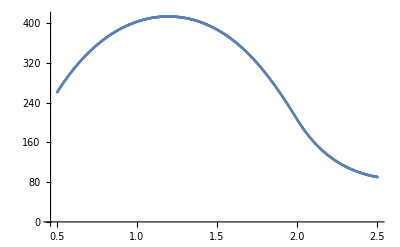

```mathematica
p1=ListPlot[tabT]
```

```mathematica
u1[x_,t_]:=x^3+x*t-4*x+20;
u2[x_,t_]:=x^2+t+16;
s[t_]:=√(4-t)
```

```mathematica
ax=1/2;
bx=5/2;
at=0;
bt=15/4;
```

```mathematica
?Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.

```mathematica
Clear[x]
```

```mathematica
u[x_,t_]:=Piecewise[{{u1[x,t],x≥ax&&x≤2},{u2[x,t],x>2&&x<bx}}];
```

```mathematica
u[0.5,0.5]
```

18.375

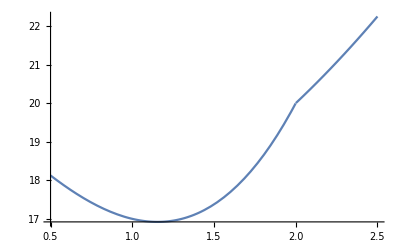

```mathematica
pd0=Plot[u[x,0],{x,0.5,2.5}]
```

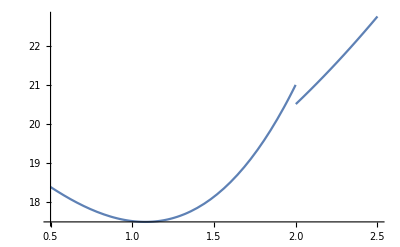

```mathematica
pd1=Plot[u[x,0.5],{x,0.5,2.5}]
```

```mathematica
u1[x_,t_]:=Exp[t-x];
```

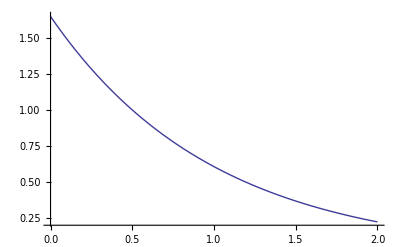

```mathematica
pd1=Plot[u1[x,0.5],{x,0,2}]
```

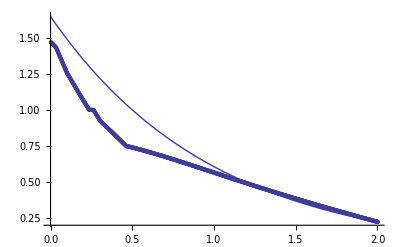

```mathematica
Show[pd1,p1]
```

### alfa = 1/2, t=1

```mathematica
str2=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,81]

```mathematica
strList2=ReadList[str2]
```

{2.6226,2.61786,2.61313,2.60841,2.60369,2.59899,2.59429,2.58961,2.58493,2.58026,2.5756,2.57095,2.5663,2.56167,2.55704,2.55243,2.54782,2.54322,2.53863,2.53405,2.52947,2.52491,2.52035,2.5158,2.51126,2.50673,2.50221,2.49769,2.49319,2.48869,2.4842,2.47972,2.47525,2.47079,2.46633,2.46188,2.45745,2.45302,2.44859,2.44418,2.43978,2.43538,2.43099,2.42661,2.42224,2.41788,2.41352,2.40917,2.40484,2.4005,2.39618,2.39187,2.38756,2.38326,2.37897,2.37469,2.37042,2.36615,2.36189,2.35764,2.3534,2.34917,2.34494,2.34072,2.33651,2.33231,2.32811,2.32393,2.31975,2.31558,2.31141,2.30726,2.30311,2.29897,2.29484,2.29071,2.28659,2.28249,2.27838,2.27429,2.2702,2.26612,2.26205,2.25799,2.25393,2.24988,2.24584,2.24181,2.23778,2.23377,2.22975,2.22575,2.22176,2.21777,2.21379,2.20981,2.20584,2.20189,2.19793,2.19399,2.19005,2.18612,2.1822,2.17828,2.17438,2.17047,2.16658,2.16269,2.15882,2.15494,2.15108,2.14722,2.14337,2.13953,2.13569,2.13186,2.12804,2.12422,2.12041,2.11661,2.11282,2.10903,2.10525,2.10148,2.09771,2.09395,2.0902,2.08645,2.08272,2.07898,2.07526,2.07154,2.06783,2.06413,2.06043,2.05674,2.05306,2.04938,2.04571,2.04205,2.03839,2.03474,2.0311,2.02747,2.02384,2.02022,2.0166,2.013,2.0094,2.0058,2.00221,1.99863,1.99506,1.99149,1.98793,1.98438,1.98083,1.97729,1.97376,1.97023,1.96671,1.96319,1.95969,1.95618,1.95269,1.9492,1.94572,1.94225,1.93878,1.93531,1.93186,1.92841,1.92497,1.92153,1.9181,1.91468,1.91126,1.90785,1.90444,1.90105,1.89765,1.89427,1.89089,1.88752,1.88415,1.88079,1.87743,1.87409,1.87074,1.86741,1.86408,1.86076,1.85744,1.85413,1.85082,1.84752,1.84423,1.84094,1.83766,1.83439,1.83112,1.82786,1.8246,1.82135,1.81811,1.81487,1.81164,1.80841,1.80519,1.80197,1.79877,1.79556,1.79237,1.78918,1.78599,1.78281,1.77964,1.77648,1.77332,1.77016,1.76701,1.76387,1.76074,1.7576,1.75448,1.75136,1.74825,1.74514,1.74204,1.73895,1.73586,1.73277,1.7297,1.72662,1.72356,1.7205,1.71744,1.71439,1.71135,1.70831,1.70528,1.70225,1.69923,1.69622,1.69321,1.69021,1.68721,1.68422,1.68123,1.67825,1.67527,1.6723,1.66934,1.66638,1.66343,1.66048,1.65754,1.6546,1.65167,1.64874,1.64582,1.64291,1.64,1.6371,1.6342,1.6313,1.62842,1.62553,1.62266,1.61978,1.61692,1.61406,1.6112,1.60835,1.60551,1.60267,1.59983,1.597,1.59418,1.59136,1.58855,1.58574,1.58294,1.58014,1.57735,1.57457,1.57179,1.56901,1.56624,1.56348,1.56072,1.55797,1.55522,1.55248,1.54974,1.54701,1.54428,1.54156,1.53884,1.53613,1.53342,1.53072,1.52803,1.52534,1.52265,1.51997,1.5173,1.51463,1.51196,1.5093,1.50665,1.504,1.50135,1.49871,1.49608,1.49345,1.49082,1.48821,1.48559,1.48298,1.48038,1.47778,1.47519,1.4726,1.47001,1.46743,1.46486,1.46229,1.45972,1.45716,1.45461,1.45206,1.44952,1.44698,1.44444,1.44191,1.43939,1.43687,1.43436,1.43185,1.42935,1.42685,1.42436,1.42187,1.41939,1.41691,1.41444,1.41197,1.40951,1.40706,1.40461,1.40217,1.39973,1.3973,1.39487,1.39245,1.39003,1.38763,1.38522,1.38282,1.38043,1.37804,1.37566,1.37328,1.37091,1.36855,1.36619,1.36384,1.36149,1.35915,1.35682,1.35449,1.35216,1.34984,1.34753,1.34522,1.34292,1.34063,1.33834,1.33606,1.33378,1.33151,1.32924,1.32698,1.32473,1.32248,1.31828,1.31176,1.30525,1.29875,1.29226,1.28579,1.27932,1.27287,1.26642,1.25999,1.25357,1.24716,1.24077,1.23438,1.228,1.22164,1.21528,1.20894,1.2026,1.19628,1.18997,1.18366,1.17737,1.17109,1.16482,1.15856,1.15231,1.14607,1.13984,1.13362,1.12741,1.12121,1.11502,1.10884,1.10266,1.0965,1.09035,1.08517,1.08071,1.07626,1.07182,1.06738,1.06295,1.05852,1.05411,1.0497,1.04529,1.04089,1.0365,1.03211,1.02773,1.02336,1.01899,1.01463,1.01028,1.00593,1.00159,1,1,1,1,1,1,1,1,0.996742,0.992288,0.987841,0.983399,0.978963,0.974533,0.97011,0.965692,0.96128,0.956873,0.952473,0.948078,0.943689,0.939306,0.934928,0.930556,0.92619,0.921829,0.917473,0.913124,0.908779,0.90444,0.900107,0.895779,0.891456,0.887139,0.882827,0.87852,0.874218,0.869922,0.866741,0.864214,0.861689,0.859167,0.856646,0.854127,0.85161,0.849095,0.846583,0.844072,0.841563,0.839057,0.836552,0.834049,0.831548,0.829049,0.826553,0.824058,0.821565,0.819074,0.816584,0.814097,0.811612,0.809128,0.806647,0.804167,0.801689,0.799214,0.79674,0.794267,0.791797,0.789328,0.786862,0.784397,0.781934,0.779473,0.777013,0.774556,0.7721,0.769645,0.767193,0.764743,0.762294,0.759847,0.757401,0.754957,0.752515,0.750075,0.747637,0.7452,0.742765,0.740331,0.737899,0.735469,0.73304,0.730613,0.728188,0.726892,0.726233,0.725573,0.724911,0.724247,0.723582,0.722916,0.722248,0.721579,0.720908,0.720235,0.719561,0.718886,0.71821,0.717531,0.716852,0.716171,0.715489,0.714805,0.71412,0.713434,0.712746,0.712057,0.711367,0.710675,0.709982,0.709288,0.708592,0.707896,0.707198,0.706498,0.705798,0.705096,0.704393,0.703689,0.702984,0.702277,0.70157,0.700861,0.700151,0.69944,0.698727,0.698014,0.6973,0.696584,0.695867,0.695149,0.694431,0.693711,0.69299,0.692268,0.691545,0.69082,0.690095,0.689369,0.688642,0.687914,0.687185,0.686455,0.685723,0.684991,0.684258,0.683525,0.68279,0.682054,0.681317,0.68058,0.679841,0.679102,0.678361,0.67762,0.676878,0.676135,0.675391,0.674647,0.673901,0.673155,0.672408,0.67166,0.670912,0.670162,0.669412,0.668661,0.667909,0.667156,0.666403,0.665649,0.664894,0.664139,0.663382,0.662625,0.661868,0.661109,0.66035,0.65959,0.65883,0.658069,0.657307,0.656544,0.655781,0.655017,0.654253,0.653488,0.652722,0.651956,0.651189,0.650421,0.649653,0.648884,0.648115,0.647345,0.646575,0.645804,0.645032,0.64426,0.643487,0.642714,0.64194,0.641166,0.640391,0.639615,0.63884,0.638063,0.637286,0.636509,0.635731,0.634953,0.634174,0.633395,0.632615,0.631835,0.631054,0.630273,0.629491,0.628709,0.627927,0.627144,0.626361,0.625577,0.624793,0.624009,0.623224,0.622439,0.621653,0.620867,0.620081,0.619294,0.618507,0.617719,0.616931,0.616143,0.615355,0.614566,0.613776,0.612987,0.612197,0.611407,0.610616,0.609826,0.609034,0.608243,0.607451,0.606659,0.605867,0.605074,0.604282,0.603488,0.602695,0.601901,0.601107,0.600313,0.599519,0.598724,0.597929,0.597134,0.596339,0.595543,0.594747,0.593951,0.593155,0.592358,0.591562,0.590765,0.589968,0.58917,0.588373,0.587575,0.586777,0.585979,0.585181,0.584383,0.583584,0.582786,0.581987,0.581188,0.580388,0.579589,0.57879,0.57799,0.57719,0.57639,0.57559,0.57479,0.57399,0.573189,0.572389,0.571588,0.570787,0.569986,0.569185,0.568384,0.567583,0.566782,0.56598,0.565179,0.564377,0.563576,0.562774,0.561972,0.56117,0.560368,0.559566,0.558764,0.557962,0.55716,0.556358,0.555555,0.554753,0.553951,0.553148,0.552346,0.551543,0.55074,0.549938,0.549135,0.548332,0.54753,0.546727,0.545924,0.545121,0.544319,0.543516,0.542713,0.54191,0.541107,0.540304,0.539502,0.538699,0.537896,0.537093,0.53629,0.535487,0.534684,0.533882,0.533079,0.532276,0.531473,0.530671,0.529868,0.529065,0.528262,0.52746,0.526657,0.525855,0.525052,0.524249,0.523447,0.522644,0.521842,0.52104,0.520237,0.519435,0.518633,0.517831,0.517029,0.516226,0.515424,0.514622,0.513821,0.513019,0.512217,0.511415,0.510614,0.509812,0.50901,0.508209,0.507408,0.506606,0.505805,0.505004,0.504203,0.503402,0.502601,0.5018,0.500999,0.500198,0.499398,0.498597,0.497797,0.496996,0.496196,0.495396,0.494596,0.493796,0.492996,0.492196,0.491396,0.490596,0.489797,0.488997,0.488198,0.487399,0.4866,0.4858,0.485001,0.484203,0.483404,0.482605,0.481806,0.481008,0.48021,0.479411,0.478613,0.477815,0.477017,0.476219,0.475422,0.474624,0.473826,0.473029,0.472232,0.471434,0.470637,0.46984,0.469043,0.468247,0.46745,0.466654,0.465857,0.465061,0.464265,0.463468,0.462672,0.461877,0.461081,0.460285,0.45949,0.458694,0.457899,0.457104,0.456309,0.455514,0.454719,0.453924,0.45313,0.452335,0.451541,0.450746,0.449952,0.449158,0.448364,0.447571,0.446777,0.445983,0.44519,0.444396,0.443603,0.44281,0.442017,0.441224,0.440431,0.439639,0.438846,0.438054,0.437261,0.436469,0.435677,0.434885,0.434093,0.433301,0.43251,0.431718,0.430927,0.430135,0.429344,0.428553,0.427762,0.426971,0.42618,0.425389,0.424598,0.423808,0.423018,0.422227,0.421437,0.420647,0.419857,0.419067,0.418277,0.417487,0.416698,0.415908,0.415119,0.414329,0.41354,0.412751,0.411962,0.411173,0.410384,0.409595,0.408806,0.408017,0.407229,0.40644,0.405652,0.404864,0.404075,0.403287,0.402499,0.401711,0.400923,0.400135,0.399348,0.39856,0.397772,0.396985,0.396197,0.39541,0.394622,0.393835,0.393048,0.39226,0.391473,0.390686,0.389899,0.389112,0.388325,0.387538,0.386752,0.385965,0.385178,0.384391,0.383605,0.382818,0.382032,0.381245,0.380459,0.379672,0.378886,0.3781,0.377313,0.376527,0.375741,0.374955,0.374168,0.373382,0.372596,0.37181,0.371024,0.370238,0.369452,0.368666,0.367879}

```mathematica
strList2={2.6226019248,2.617861204,2.6131294933,2.6084067679,2.6036930028,2.5989881734,2.5942922548,2.5896052223,2.5849270515,2.5802577175,2.5755971959,2.5709454622,2.5663024918,2.5616682607,2.5570427457,2.5524259242,2.547817773,2.5432182701,2.5386273945,2.5340451254,2.5294714419,2.5249063235,2.5203497492,2.5158016985,2.5112621508,2.5067310854,2.5022084818,2.4976943195,2.493188578,2.4886912369,2.4842022758,2.4797216744,2.4752494124,2.4707856631,2.4663304035,2.4618836104,2.4574452608,2.4530153317,2.4485938002,2.4441806434,2.4397758383,2.4353793622,2.4309911924,2.426611306,2.4222396804,2.4178762929,2.4135211209,2.409174142,2.4048353334,2.4005046735,2.3961821445,2.3918677288,2.3875614094,2.3832631691,2.378972991,2.374690858,2.3704167533,2.3661506598,2.3618925606,2.3576424389,2.3534002778,2.3491660606,2.3449397703,2.3407213904,2.3365109039,2.3323082944,2.328113545,2.3239266392,2.3197475603,2.3155762918,2.3114128171,2.3072571197,2.3031091832,2.298968991,2.2948365267,2.290711774,2.2865947165,2.2824853378,2.2783836216,2.2742895516,2.2702031116,2.2661242854,2.2620530567,2.2579894095,2.2539333274,2.2498847946,2.2458437947,2.2418103119,2.2377843301,2.2337658333,2.2297548055,2.2257512308,2.2217550932,2.2177663769,2.2137850661,2.2098111449,2.2058445974,2.201885408,2.1979335609,2.1939890403,2.1900518307,2.1861219162,2.1821992813,2.1782839104,2.1743757879,2.1704748982,2.1665812259,2.1626947554,2.1588154712,2.1549433579,2.1510784001,2.1472205824,2.1433698894,2.1395263059,2.1356898164,2.1318604057,2.1280380585,2.1242227597,2.120414494,2.1166132462,2.1128190025,2.1090317503,2.105251477,2.1014781699,2.0977118166,2.0939524044,2.090199921,2.0864543536,2.0827156901,2.0789839177,2.0752590243,2.0715409972,2.0678299847,2.0641259712,2.060428941,2.0567388788,2.053055769,2.0493795963,2.0457103451,2.0420480002,2.0383925461,2.0347439676,2.0311022493,2.027467376,2.0238393324,2.0202181033,2.0166036735,2.0129960279,2.0093951513,2.0058010286,2.0022136447,1.9986329846,1.9950590334,1.9914917766,1.9879311997,1.9843772883,1.9808300277,1.9772894037,1.9737554017,1.9702280074,1.9667072065,1.9631929846,1.9596853274,1.9561842206,1.95268965,1.9492016013,1.9457200604,1.942245013,1.938776445,1.9353143422,1.9318586906,1.9284094761,1.9249666846,1.9215303021,1.9181003146,1.914676708,1.9112594685,1.9078485821,1.904444035,1.9010458131,1.8976539027,1.8942682899,1.890888961,1.8875159021,1.8841490994,1.8807885393,1.8774342079,1.8740860917,1.870744177,1.8674084501,1.8640788973,1.8607555052,1.8574382601,1.8541271484,1.8508221568,1.8475232715,1.8442304793,1.8409437665,1.8376631209,1.8343885322,1.8311199902,1.8278574847,1.8246010055,1.8213505424,1.8181060854,1.8148676243,1.811635149,1.8084086494,1.8051881156,1.8019736839,1.7987653412,1.7955630739,1.7923668689,1.7891767128,1.7859925924,1.7828144943,1.7796424053,1.7764763123,1.7733162021,1.7701620615,1.7670138774,1.7638716367,1.7607353263,1.7576049331,1.7544804441,1.7513618463,1.7482491267,1.7451422723,1.7420412702,1.7389461074,1.7358567711,1.7327732484,1.7296955264,1.7266235925,1.7235574341,1.7204970384,1.7174423929,1.7143934851,1.7113503024,1.7083128323,1.7052810622,1.7022549797,1.6992345723,1.6962198276,1.6932107332,1.6902072766,1.6872094455,1.6842172276,1.6812306104,1.6782495817,1.6752741292,1.6723042406,1.6693399036,1.6663811061,1.6634278359,1.6604800806,1.6575378282,1.6546010666,1.6516697835,1.6487439669,1.6458236047,1.6429086848,1.6399991952,1.6370951239,1.6341964588,1.631303188,1.6284153036,1.6255327988,1.6226556665,1.6197838999,1.6169174918,1.6140564355,1.611200724,1.6083503505,1.6055053079,1.602665733,1.5998316154,1.5970029447,1.5941797108,1.5913619034,1.5885495121,1.5857425269,1.5829409374,1.5801447335,1.5773539051,1.5745684419,1.5717883338,1.5690135707,1.5662441425,1.5634800391,1.5607212504,1.5579677663,1.5552195768,1.5524766718,1.5497390414,1.5470066756,1.5442795642,1.5415576974,1.5388410652,1.5361296576,1.5334234648,1.5307224761,1.528026681,1.5253360688,1.5226506288,1.5199703504,1.517295223,1.514625236,1.5119603787,1.5093006405,1.506646011,1.5039964796,1.5013520356,1.4987126686,1.496078368,1.4934491233,1.490824924,1.4882057597,1.4855916199,1.482982494,1.4803783716,1.4777792423,1.4751850957,1.4725959213,1.4700117088,1.4674324476,1.4648581274,1.4622887379,1.4597242858,1.4571647924,1.454610279,1.452060767,1.4495162777,1.4469768323,1.4444424519,1.4419131579,1.4393889714,1.4368700533,1.4343564214,1.4318480931,1.429345086,1.4268474178,1.4243551059,1.4218681679,1.4193866214,1.4169104837,1.4144397725,1.4119745053,1.4095146995,1.4070603726,1.404611542,1.4021682253,1.3997304399,1.3972982033,1.3948715328,1.392450446,1.3900349603,1.3876250931,1.3852208618,1.3828222839,1.3804293769,1.3780421581,1.375660645,1.373284855,1.3709147994,1.3685504835,1.3661919126,1.3638390922,1.3614920277,1.3591507246,1.3568151883,1.3544854244,1.3521614383,1.3498432357,1.3475308222,1.3452242032,1.3429233845,1.3406283717,1.3383391705,1.3360557866,1.3337782258,1.3315064938,1.3292405964,1.3269805395,1.3247263289,1.3224779704,1.3182823868,1.3117599834,1.3052491637,1.298749871,1.2922620488,1.2857856408,1.2793205907,1.2728668422,1.2664243393,1.2599929703,1.2535726792,1.24716341,1.2407651067,1.2343777135,1.2280011748,1.2216354347,1.2152804379,1.2089361288,1.2026024521,1.1962793526,1.189966775,1.1836646642,1.1773729653,1.1710916233,1.1648205834,1.1585597909,1.1523091911,1.1460687295,1.1398383514,1.1336180027,1.1274076289,1.1212071757,1.1150165891,1.108835815,1.1026647993,1.0965034882,1.0903518279,1.08516793,1.0807107657,1.0762602532,1.0718163618,1.0673790607,1.0629483193,1.058524107,1.0541063931,1.049695147,1.0452903383,1.0408919364,1.0364999109,1.0321142313,1.0277348673,1.0233617884,1.0189949644,1.0146343649,1.0102799597,1.0059317186,1.0015896113,1,1,1,1,1,1,1,1,0.9967420477,0.9922883281,0.9878406444,0.9833989654,0.9789632604,0.9745334981,0.9701096478,0.9656916785,0.9612795593,0.9568732593,0.9524727477,0.9480779938,0.9436889666,0.9393056356,0.9349279698,0.9305559387,0.9261895116,0.9218286577,0.9174733465,0.9131235474,0.9087792298,0.9044403631,0.9001069168,0.8957788603,0.8914561632,0.8871387951,0.8828267254,0.8785199238,0.8742183598,0.869922003,0.8667413277,0.8642143337,0.8616894006,0.8591665209,0.8566456872,0.8541268918,0.8516101273,0.849095386,0.8465826604,0.8440719428,0.8415632256,0.8390565011,0.8365517617,0.8340489997,0.8315482072,0.8290493767,0.8265525002,0.8240575701,0.8215645785,0.8190735175,0.8165843794,0.8140971562,0.8116118401,0.8091284231,0.8066468973,0.8041672548,0.8016894875,0.7992135875,0.7967395467,0.7942673572,0.7917970107,0.7893284993,0.7868618148,0.784396949,0.781933894,0.7794726414,0.777013183,0.7745555108,0.7720996163,0.7696454914,0.7671931277,0.764742517,0.762293651,0.7598465212,0.7574011194,0.7549574371,0.7525154658,0.7500751973,0.747636623,0.7451997344,0.742764523,0.7403309804,0.7378990979,0.7354688669,0.733040279,0.7306133255,0.7281879977,0.7268920069,0.7262331805,0.7255728022,0.7249108838,0.7242474372,0.7235824739,0.7229160057,0.722248044,0.7215786004,0.7209076863,0.7202353131,0.7195614921,0.7188862346,0.7182095518,0.7175314548,0.7168519548,0.7161710628,0.7154887897,0.7148051465,0.7141201441,0.7134337933,0.7127461047,0.7120570892,0.7113667573,0.7106751197,0.7099821869,0.7092879693,0.7085924774,0.7078957216,0.7071977121,0.7064984593,0.7057979733,0.7050962643,0.7043933423,0.7036892175,0.7029838998,0.7022773991,0.7015697254,0.7008608885,0.7001508982,0.6994397641,0.698727496,0.6980141035,0.6972995962,0.6965839835,0.695867275,0.6951494802,0.6944306082,0.6937106686,0.6929896705,0.6922676232,0.6915445359,0.6908204176,0.6900952774,0.6893691244,0.6886419675,0.6879138157,0.6871846778,0.6864545627,0.6857234791,0.6849914358,0.6842584415,0.6835245047,0.6827896341,0.6820538383,0.6813171256,0.6805795046,0.6798409837,0.6791015712,0.6783612753,0.6776201045,0.6768780669,0.6761351706,0.6753914238,0.6746468345,0.6739014108,0.6731551608,0.6724080922,0.671660213,0.6709115311,0.6701620543,0.6694117903,0.6686607469,0.6679089317,0.6671563523,0.6664030164,0.6656489315,0.6648941051,0.6641385446,0.6633822575,0.6626252511,0.6618675328,0.6611091099,0.6603499895,0.6595901789,0.6588296853,0.6580685157,0.6573066773,0.6565441771,0.6557810221,0.6550172192,0.6542527753,0.6534876973,0.6527219921,0.6519556664,0.651188727,0.6504211806,0.6496530338,0.6488842933,0.6481149657,0.6473450575,0.6465745753,0.6458035254,0.6450319144,0.6442597486,0.6434870343,0.642713778,0.6419399858,0.6411656641,0.6403908189,0.6396154565,0.6388395829,0.6380632044,0.6372863268,0.6365089563,0.6357310988,0.6349527602,0.6341739464,0.6333946633,0.6326149168,0.6318347125,0.6310540563,0.6302729538,0.6294914108,0.6287094329,0.6279270256,0.6271441946,0.6263609454,0.6255772834,0.6247932142,0.6240087432,0.6232238757,0.6224386172,0.6216529729,0.6208669481,0.6200805481,0.6192937781,0.6185066432,0.6177191487,0.6169312996,0.616143101,0.615354558,0.6145656756,0.6137764587,0.6129869123,0.6121970413,0.6114068505,0.6106163449,0.6098255293,0.6090344083,0.6082429868,0.6074512695,0.606659261,0.605866966,0.6050743891,0.6042815349,0.603488408,0.6026950128,0.6019013538,0.6011074355,0.6003132624,0.5995188388,0.598724169,0.5979292574,0.5971341084,0.596338726,0.5955431147,0.5947472786,0.5939512218,0.5931549485,0.5923584629,0.5915617689,0.5907648707,0.5899677723,0.5891704776,0.5883729906,0.5875753153,0.5867774556,0.5859794152,0.5851811981,0.5843828081,0.5835842489,0.5827855243,0.581986638,0.5811875937,0.5803883951,0.5795890458,0.5787895495,0.5779899096,0.5771901298,0.5763902135,0.5755901644,0.5747899857,0.5739896809,0.5731892536,0.572388707,0.5715880444,0.5707872693,0.5699863849,0.5691853945,0.5683843013,0.5675831085,0.5667818193,0.5659804369,0.5651789644,0.5643774049,0.5635757615,0.5627740373,0.5619722351,0.5611703582,0.5603684093,0.5595663915,0.5587643077,0.5579621607,0.5571599535,0.5563576889,0.5555553696,0.5547529985,0.5539505783,0.5531481117,0.5523456015,0.5515430503,0.5507404609,0.5499378357,0.5491351775,0.5483324888,0.5475297722,0.5467270301,0.5459242651,0.5451214797,0.5443186763,0.5435158574,0.5427130253,0.5419101824,0.5411073311,0.5403044738,0.5395016126,0.5386987499,0.537895888,0.5370930291,0.5362901753,0.535487329,0.5346844921,0.5338816669,0.5330788555,0.5322760599,0.5314732823,0.5306705246,0.5298677889,0.5290650772,0.5282623914,0.5274597334,0.5266571053,0.5258545089,0.525051946,0.5242494186,0.5234469284,0.5226444773,0.521842067,0.5210396993,0.5202373759,0.5194350986,0.518632869,0.5178306889,0.5170285598,0.5162264833,0.5154244612,0.5146224948,0.5138205859,0.513018736,0.5122169465,0.5114152189,0.5106135547,0.5098119554,0.5090104224,0.5082089571,0.5074075608,0.5066062349,0.5058049808,0.5050037997,0.504202693,0.5034016619,0.5026007077,0.5017998316,0.5009990348,0.5001983186,0.4993976839,0.4985971321,0.4977966642,0.4969962813,0.4961959845,0.4953957749,0.4945956535,0.4937956213,0.4929956792,0.4921958284,0.4913960697,0.4905964041,0.4897968325,0.4889973557,0.4881979747,0.4873986903,0.4865995033,0.4858004146,0.4850014249,0.4842025349,0.4834037455,0.4826050574,0.4818064713,0.4810079878,0.4802096077,0.4794113316,0.4786131601,0.4778150938,0.4770171333,0.4762192792,0.475421532,0.4746238923,0.4738263606,0.4730289373,0.472231623,0.471434418,0.4706373228,0.4698403379,0.4690434636,0.4682467002,0.4674500483,0.4666535079,0.4658570796,0.4650607636,0.4642645601,0.4634684694,0.4626724918,0.4618766275,0.4610808766,0.4602852394,0.4594897161,0.4586943066,0.4578990113,0.4571038301,0.4563087633,0.4555138107,0.4547189726,0.4539242489,0.4531296396,0.4523351447,0.4515407642,0.4507464981,0.4499523463,0.4491583087,0.4483643852,0.4475705756,0.44677688,0.445983298,0.4451898295,0.4443964744,0.4436032324,0.4428101033,0.4420170868,0.4412241827,0.4404313906,0.4396387104,0.4388461416,0.438053684,0.4372613371,0.4364691007,0.4356769742,0.4348849574,0.4340930497,0.4333012507,0.43250956,0.4317179771,0.4309265014,0.4301351325,0.4293438698,0.4285527127,0.4277616608,0.4269707134,0.4261798699,0.4253891296,0.424598492,0.4238079563,0.4230175219,0.4222271881,0.4214369543,0.4206468195,0.4198567832,0.4190668445,0.4182770026,0.4174872568,0.4166976063,0.4159080501,0.4151185875,0.4143292176,0.4135399394,0.4127507521,0.4119616548,0.4111726465,0.4103837262,0.4095948931,0.408806146,0.408017484,0.4072289061,0.4064404111,0.4056519981,0.404863666,0.4040754137,0.40328724,0.4024991438,0.401711124,0.4009231794,0.4001353089,0.3993475112,0.3985597851,0.3977721293,0.3969845427,0.396197024,0.3954095718,0.3946221849,0.393834862,0.3930476017,0.3922604026,0.3914732635,0.3906861828,0.3898991592,0.3891121914,0.3883252777,0.3875384168,0.3867516073,0.3859648475,0.3851781361,0.3843914715,0.3836048521,0.3828182763,0.3820317427,0.3812452496,0.3804587955,0.3796723786,0.3788859973,0.37809965,0.3773133351,0.3765270507,0.3757407952,0.3749545669,0.374168364,0.3733821848,0.3725960275,0.3718098902,0.3710237712,0.3702376687,0.3694515808,0.3686655055,0.3678794412};
```

```mathematica
tabT2=Table[{i*0.002,strList2[[i]]},{i,1,1001}];
```

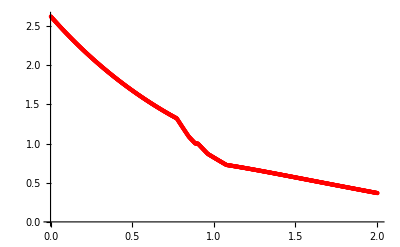

```mathematica
p2=ListPlot[tabT2,PlotStyle->Red]
```

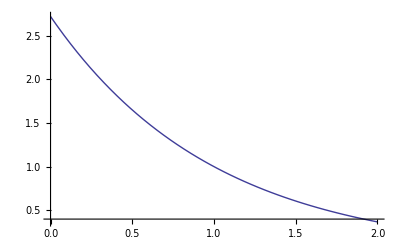

```mathematica
pd2=Plot[u1[x,1],{x,0,2}]
```

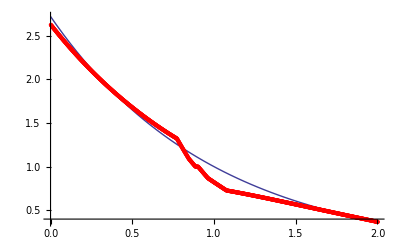

```mathematica
Show[pd2,p2]
```

### alfa = 1/2, t=1.5

```mathematica
str3=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,82]

```mathematica
strList3=ReadList[str3]
```

{4.42244,4.41414,4.40587,4.3976,4.38936,4.38113,4.37292,4.36472,4.35654,4.34837,4.34022,4.33209,4.32397,4.31587,4.30778,4.29971,4.29166,4.28362,4.2756,4.26759,4.2596,4.25162,4.24366,4.23572,4.22779,4.21987,4.21197,4.20409,4.19622,4.18837,4.18053,4.17271,4.1649,4.15711,4.14933,4.14157,4.13383,4.12609,4.11838,4.11068,4.10299,4.09532,4.08767,4.08003,4.0724,4.06479,4.05719,4.04961,4.04205,4.03449,4.02696,4.01944,4.01193,4.00444,3.99696,3.9895,3.98205,3.97461,3.96719,3.95979,3.9524,3.94502,3.93766,3.93031,3.92298,3.91566,3.90835,3.90106,3.89379,3.88653,3.87928,3.87204,3.86482,3.85762,3.85043,3.84325,3.83609,3.82894,3.8218,3.81468,3.80757,3.80048,3.7934,3.78633,3.77928,3.77224,3.76521,3.7582,3.7512,3.74422,3.73725,3.73029,3.72335,3.71642,3.7095,3.7026,3.69571,3.68883,3.68197,3.67512,3.66828,3.66146,3.65465,3.64785,3.64107,3.6343,3.62754,3.6208,3.61407,3.60735,3.60065,3.59395,3.58728,3.58061,3.57396,3.56732,3.56069,3.55408,3.54747,3.54089,3.53431,3.52775,3.5212,3.51466,3.50813,3.50162,3.49512,3.48864,3.48216,3.4757,3.46925,3.46281,3.45639,3.44998,3.44358,3.43719,3.43082,3.42446,3.41811,3.41177,3.40545,3.39914,3.39284,3.38655,3.38028,3.37402,3.36777,3.36153,3.3553,3.34909,3.34289,3.3367,3.33052,3.32436,3.31821,3.31207,3.30594,3.29982,3.29372,3.28762,3.28154,3.27547,3.26942,3.26337,3.25734,3.25132,3.24531,3.23931,3.23333,3.22735,3.22139,3.21544,3.2095,3.20357,3.19765,3.19175,3.18586,3.17998,3.17411,3.16825,3.1624,3.15656,3.15074,3.14493,3.13913,3.13333,3.12756,3.12179,3.11603,3.11029,3.10455,3.09883,3.09312,3.08742,3.08173,3.07605,3.07038,3.06473,3.05908,3.05345,3.04782,3.04221,3.03661,3.03102,3.02544,3.01987,3.01431,3.00877,3.00323,2.99771,2.99219,2.98669,2.9812,2.97571,2.97024,2.96478,2.95933,2.9539,2.94847,2.94305,2.93764,2.93225,2.92686,2.92149,2.91613,2.91077,2.90543,2.9001,2.89478,2.88947,2.88416,2.87887,2.87359,2.86832,2.86307,2.85782,2.85258,2.84735,2.84213,2.83693,2.83173,2.82654,2.82136,2.8162,2.81104,2.80589,2.80076,2.79563,2.79052,2.78541,2.78031,2.77523,2.77015,2.76509,2.76003,2.75498,2.74995,2.74492,2.7399,2.7349,2.7299,2.72491,2.71994,2.71497,2.71001,2.70506,2.70012,2.6952,2.69028,2.68537,2.68047,2.67558,2.6707,2.66583,2.66096,2.65611,2.65127,2.64644,2.64162,2.6368,2.632,2.6272,2.62242,2.61765,2.61288,2.60812,2.60338,2.59864,2.59391,2.58919,2.58449,2.57979,2.5751,2.57041,2.56574,2.56108,2.55643,2.55178,2.54715,2.54252,2.53791,2.5333,2.5287,2.52411,2.51953,2.51496,2.5104,2.50585,2.5013,2.49677,2.49224,2.48773,2.48322,2.47872,2.47423,2.46975,2.46528,2.46082,2.45636,2.45192,2.44748,2.44305,2.43863,2.43422,2.42982,2.42543,2.42104,2.41667,2.4123,2.40794,2.40359,2.39925,2.39492,2.39059,2.38628,2.38197,2.37767,2.37338,2.3691,2.36483,2.36056,2.35631,2.35206,2.34782,2.34359,2.33937,2.33516,2.33095,2.32676,2.32257,2.31839,2.31422,2.31006,2.30591,2.30176,2.29762,2.29349,2.28937,2.28526,2.28116,2.27706,2.27297,2.26889,2.26482,2.26076,2.2567,2.25266,2.24862,2.24459,2.24056,2.23655,2.23254,2.22854,2.22455,2.22057,2.2166,2.21263,2.20867,2.20472,2.20078,2.19684,2.19291,2.18899,2.18508,2.18118,2.17728,2.1734,2.16951,2.16564,2.16178,2.15792,2.15407,2.15023,2.1464,2.14257,2.13875,2.13494,2.13114,2.12734,2.12355,2.11977,2.116,2.11224,2.10848,2.10473,2.10099,2.09726,2.09353,2.08981,2.0861,2.0824,2.0787,2.07501,2.07133,2.06766,2.06399,2.06033,2.05668,2.05304,2.0494,2.04578,2.04215,2.03854,2.03493,2.03133,2.02774,2.02416,2.02058,2.01701,2.01345,2.00989,2.00634,2.0028,1.99927,1.99574,1.99222,1.98871,1.9852,1.9817,1.97821,1.97473,1.97125,1.96778,1.96432,1.96086,1.95741,1.95397,1.95053,1.94711,1.94369,1.94027,1.93686,1.93346,1.93007,1.92668,1.92331,1.91993,1.91657,1.91321,1.90986,1.90652,1.90318,1.89985,1.89653,1.89321,1.8899,1.8866,1.8833,1.88001,1.87673,1.87345,1.87019,1.86692,1.86367,1.86042,1.85718,1.85394,1.85072,1.8475,1.84428,1.84107,1.83787,1.83468,1.83149,1.82831,1.82513,1.82196,1.8188,1.81565,1.8125,1.80936,1.80622,1.80309,1.79997,1.79685,1.79374,1.79064,1.78754,1.78445,1.78137,1.77829,1.77522,1.77215,1.7691,1.76604,1.763,1.75996,1.75693,1.7539,1.75088,1.74787,1.74486,1.74186,1.73886,1.73587,1.73289,1.72992,1.72695,1.72399,1.72103,1.71808,1.71514,1.7122,1.70927,1.70634,1.70342,1.70051,1.6976,1.6947,1.69181,1.68892,1.68604,1.68316,1.6803,1.67743,1.67458,1.67172,1.66888,1.66604,1.66321,1.66038,1.65756,1.65475,1.65194,1.64913,1.64634,1.64355,1.64076,1.63798,1.63521,1.63245,1.62968,1.62693,1.62418,1.62144,1.6187,1.61597,1.61324,1.61052,1.60781,1.6051,1.6024,1.5997,1.59701,1.59433,1.59165,1.58898,1.58631,1.58365,1.58099,1.57835,1.5757,1.57307,1.57043,1.56781,1.56519,1.56258,1.55997,1.55736,1.55477,1.55218,1.54959,1.54701,1.54444,1.54187,1.53931,1.53676,1.53421,1.53166,1.52912,1.52659,1.52406,1.52154,1.51903,1.51652,1.51401,1.51151,1.50902,1.50653,1.50405,1.50157,1.4991,1.49664,1.49418,1.49172,1.48927,1.48683,1.48439,1.48196,1.47954,1.47712,1.4747,1.47229,1.46989,1.46749,1.46509,1.46271,1.46032,1.45795,1.45558,1.45321,1.45085,1.4485,1.44615,1.44381,1.44147,1.43914,1.43681,1.43449,1.43218,1.42987,1.42757,1.42528,1.42299,1.42071,1.41843,1.41616,1.41389,1.41163,1.40938,1.40713,1.40489,1.40266,1.40043,1.39821,1.39599,1.39378,1.39158,1.38938,1.38719,1.38501,1.38283,1.38066,1.37849,1.37633,1.37418,1.37204,1.3699,1.36776,1.36564,1.36351,1.3614,1.35929,1.35719,1.3551,1.35301,1.35093,1.34885,1.34678,1.34472,1.34266,1.34061,1.33857,1.33653,1.33281,1.32669,1.32059,1.3145,1.30843,1.30237,1.29632,1.29029,1.28426,1.27826,1.27226,1.26628,1.26031,1.25435,1.24841,1.24247,1.23656,1.23065,1.22475,1.21887,1.213,1.20715,1.2013,1.19547,1.18965,1.18384,1.17805,1.17226,1.16649,1.16073,1.15498,1.14925,1.14352,1.13781,1.13211,1.12642,1.12075,1.11508,1.10942,1.10378,1.09831,1.09428,1.09026,1.08625,1.08224,1.07824,1.07425,1.07027,1.0663,1.06233,1.05837,1.05442,1.05048,1.04654,1.04261,1.03869,1.03478,1.03087,1.02698,1.02309,1.0192,1.01533,1.01146,1.0076,1.00375,1,1,1,1,1,1,1,1,0.997116,0.993183,0.989259,0.985341,0.981431,0.977528,0.973633,0.969745,0.965863,0.96199,0.958123,0.954263,0.95041,0.946565,0.942726,0.938895,0.93507,0.931253,0.927442,0.923639,0.919842,0.916052,0.912269,0.908492,0.904723,0.90096,0.897204,0.893454,0.889712,0.885976,0.882246,0.878523,0.874807,0.871097,0.867688,0.865528,0.863371,0.861217,0.859065,0.856917,0.854771,0.852628,0.850489,0.848352,0.846217,0.844086,0.841957,0.839831,0.837708,0.835588,0.833471,0.831356,0.829244,0.827135,0.825029,0.822925,0.820824,0.818726,0.816631,0.814538,0.812448,0.810361,0.808276,0.806195,0.804116,0.802039,0.799965,0.797894,0.795826,0.79376,0.791697,0.789636,0.787579,0.785523,0.783471,0.781421,0.779374,0.777329,0.775287,0.773247,0.77121,0.769176,0.767144,0.765115,0.763088,0.761064,0.759042,0.757023,0.755007,0.752992,0.750981,0.748972,0.746965,0.744961,0.74296,0.740961,0.738964,0.73697,0.734978,0.732989,0.731002,0.729018,0.727036,0.725057,0.72308,0.721105,0.719133,0.717163,0.715195,0.71323,0.711267,0.709307,0.707349,0.705922,0.705296,0.704668,0.704039,0.703408,0.702776,0.702142,0.701507,0.700871,0.700233,0.699594,0.698954,0.698312,0.697669,0.697024,0.696379,0.695731,0.695083,0.694433,0.693782,0.693129,0.692475,0.69182,0.691164,0.690506,0.689847,0.689187,0.688525,0.687862,0.687198,0.686533,0.685866,0.685198,0.684529,0.683859,0.683187,0.682514,0.68184,0.681165,0.680488,0.679811,0.679132,0.678452,0.67777,0.677088,0.676404,0.675719,0.675033,0.674346,0.673658,0.672968,0.672278,0.671586,0.670893,0.670199,0.669503,0.668807,0.668109,0.667411,0.666711,0.66601,0.665308,0.664605,0.663901,0.663195,0.662489,0.661781,0.661072,0.660363,0.659652,0.65894,0.658227,0.657513,0.656798,0.656081,0.655364,0.654645,0.653926,0.653205,0.652484,0.651761,0.651037,0.650313,0.649587,0.64886,0.648132,0.647403,0.646673,0.645942,0.64521,0.644477,0.643743,0.643007,0.642271,0.641534,0.640796,0.640056,0.639316,0.638575,0.637832,0.637089,0.636345,0.635599,0.634853,0.634105,0.633357,0.632607,0.631857,0.631105,0.630353,0.6296,0.628845,0.62809,0.627333,0.626576,0.625817,0.625058,0.624297,0.623536,0.622773,0.62201,0.621245,0.62048,0.619713,0.618946,0.618177,0.617408,0.616637,0.615866,0.615093,0.61432,0.613546,0.61277,0.611994,0.611216,0.610438,0.609658,0.608878,0.608097,0.607314,0.606531}

```mathematica
strList3={4.4224373413,4.4141432421,4.4058653934,4.3976037567,4.3893582935,4.3811289655,4.3729157343,4.3647185617,4.3565374097,4.34837224,4.3402230147,4.3320896959,4.3239722457,4.3158706265,4.3077848024,4.2997147374,4.2916603955,4.2836217414,4.2755987412,4.2675913607,4.2595995661,4.2516233236,4.2436625994,4.2357173597,4.2277875709,4.2198731994,4.2119742118,4.2040905746,4.1962222544,4.1883692179,4.1805314318,4.1727088631,4.1649014786,4.1571094389,4.1493327082,4.1415712505,4.1338250303,4.1260940117,4.1183781593,4.1106774375,4.1029918109,4.095321244,4.0876657015,4.0800251482,4.072399549,4.0647888686,4.057193072,4.0496121244,4.0420459907,4.0344946366,4.0269580313,4.0194361442,4.0119289453,4.0044364046,3.9969584922,3.9894951783,3.9820464331,3.9746122269,3.9671925301,3.9597873131,3.9523965462,3.9450202001,3.9376582452,3.9303106523,3.922977392,3.915658435,3.9083537522,3.9010633144,3.8937870924,3.8865250573,3.8792771801,3.8720434318,3.8648237836,3.8576182067,3.8504266723,3.8432491517,3.8360856163,3.8289360374,3.8218003865,3.8146786352,3.807570755,3.8004767175,3.7933964944,3.7863300575,3.7792773785,3.7722384293,3.7652131817,3.7582016077,3.7512036794,3.7442193687,3.7372486479,3.7302914889,3.7233478641,3.7164177458,3.7095011062,3.7025979178,3.6957081529,3.688831784,3.6819687837,3.6751191246,3.6682827792,3.6614597204,3.6546499207,3.6478533531,3.6410699904,3.6342998055,3.6275427712,3.6207988607,3.6140680469,3.6073503031,3.6006456022,3.5939539177,3.5872752226,3.5806094903,3.5739566942,3.5673168077,3.5606898042,3.5540756573,3.5474743405,3.5408858274,3.5343100929,3.5277471126,3.5211968625,3.5146593184,3.5081344563,3.5016222522,3.495122682,3.488635722,3.4821613481,3.4756995367,3.4692502639,3.4628135059,3.4563893996,3.4499779181,3.4435790346,3.4371927223,3.4308189547,3.424457705,3.4181089467,3.4117726533,3.4054487982,3.3991373551,3.3928382976,3.3865515994,3.3802772342,3.3740151758,3.3677653979,3.3615278746,3.3553025797,3.3490894872,3.3428885711,3.3366998056,3.3305231651,3.3243586245,3.3182061588,3.3120657432,3.3059373527,3.2998209624,3.2937165475,3.2876240834,3.2815435452,3.2754749084,3.2694181483,3.2633732403,3.25734016,3.2513188828,3.2453093844,3.2393116404,3.2333256265,3.2273513183,3.2213886917,3.2154377224,3.2094983864,3.2035706595,3.1976545177,3.1917499371,3.1858568935,3.1799753632,3.1741053223,3.168246747,3.1623996135,3.1565638981,3.1507395771,3.1449266269,3.139125024,3.1333347447,3.1275557655,3.1217880632,3.1160316142,3.1102863951,3.1045523828,3.0988295539,3.0931178851,3.0874173534,3.0817279356,3.0760496086,3.0703823494,3.0647261349,3.059080943,3.0534467531,3.0478235445,3.0422112966,3.036609989,3.0310196012,3.0254401127,3.0198715032,3.0143137523,3.0087668397,3.0032307451,2.9977055949,2.9921913656,2.9866880336,2.9811955756,2.9757139682,2.9702431879,2.9647832115,2.9593340157,2.9538955773,2.9484678731,2.94305088,2.9376445749,2.9322489348,2.9268639367,2.9214895576,2.9161257747,2.9107725651,2.9054299059,2.9000977745,2.8947761481,2.8894650039,2.8841643195,2.8788740721,2.8735942393,2.8683247993,2.8630657305,2.8578170112,2.8525786199,2.8473505351,2.8421327353,2.836925199,2.8317279048,2.8265408314,2.8213639575,2.8161972618,2.8110407231,2.8058943201,2.8007580318,2.7956318369,2.7905157146,2.7854096437,2.7803136032,2.7752275723,2.7701515299,2.7650854553,2.7600293277,2.7549831262,2.7499468301,2.7449204187,2.7399038714,2.7348971676,2.7299002866,2.724913208,2.7199359112,2.7149683758,2.7100105814,2.7050625076,2.7001241361,2.6951954489,2.6902764283,2.6853670564,2.6804673154,2.6755771875,2.6706966551,2.6658257004,2.6609643058,2.6561125972,2.6512705535,2.6464381538,2.641615377,2.6368022024,2.6319986091,2.6272045762,2.6224200829,2.6176451086,2.6128796325,2.6081236341,2.6033770926,2.5986399876,2.5939122985,2.5891940047,2.584485086,2.5797855218,2.5750952919,2.5704143758,2.5657427533,2.5610804042,2.5564273083,2.5517834453,2.5471487952,2.542523338,2.5379070534,2.5332999222,2.5287019251,2.5241130431,2.519533257,2.5149625478,2.5104008965,2.505848284,2.5013046916,2.4967701002,2.492244491,2.4877278451,2.4832201439,2.4787213685,2.4742315003,2.4697505205,2.4652784105,2.4608151518,2.4563607257,2.4519151137,2.4474782973,2.4430502582,2.4386309778,2.4342204378,2.4298186198,2.4254255056,2.4210410768,2.4166653153,2.4122982041,2.4079397277,2.4035898704,2.3992486167,2.394915951,2.3905918579,2.3862763218,2.3819693273,2.377670859,2.3733810414,2.3690998556,2.3648272827,2.3605633041,2.3563079009,2.3520610544,2.347822746,2.3435929571,2.3393716689,2.3351588631,2.330954521,2.3267586242,2.3225711541,2.3183920925,2.314221421,2.3100591211,2.3059051747,2.3017595634,2.297622269,2.2934932734,2.2893725584,2.2852601058,2.2811558976,2.2770599158,2.2729721423,2.2688925592,2.2648211486,2.2607578929,2.256702775,2.252655778,2.2486168847,2.2445860782,2.2405633415,2.2365486576,2.2325420098,2.2285433812,2.2245527548,2.2205701141,2.2165954421,2.2126287221,2.2086699376,2.2047190718,2.2007761081,2.1968410299,2.1929138207,2.1889944639,2.1850829431,2.1811792419,2.1772833437,2.1733952322,2.1695148924,2.1656423104,2.1617774729,2.157920366,2.1540709764,2.1502292906,2.1463952949,2.142568976,2.1387504617,2.1349397351,2.1311367791,2.127341577,2.1235541119,2.1197743669,2.1160023252,2.1122379701,2.1084812849,2.1047322528,2.1009908573,2.0972570816,2.0935309093,2.0898123236,2.0861013083,2.0823978466,2.0787019223,2.0750135189,2.07133262,2.0676592092,2.0639932702,2.0603347869,2.0566837428,2.0530401218,2.0494039077,2.0457750844,2.0421536358,2.0385395457,2.0349327981,2.0313333774,2.0277412683,2.0241564556,2.0205789239,2.0170086582,2.0134456432,2.0098898638,2.0063413049,2.0027999513,1.9992657882,1.9957388004,1.992218973,1.9887062911,1.9852007396,1.9817023037,1.9782109686,1.9747267193,1.9712495412,1.9677794194,1.9643163393,1.9608602868,1.9574112502,1.9539692179,1.9505341781,1.9471061193,1.9436850297,1.9402708978,1.9368637119,1.9334636017,1.9300705521,1.9266845479,1.9233055741,1.9199336157,1.9165686577,1.9132106851,1.909859683,1.9065156365,1.9031785308,1.899848351,1.8965250823,1.8932087099,1.8898992192,1.8865965953,1.8833008237,1.8800118897,1.8767297786,1.8734544759,1.8701859671,1.8669242375,1.8636692728,1.8604210584,1.8571795799,1.8539448229,1.8507167731,1.8474954161,1.8442807376,1.8410727233,1.837871359,1.8346766307,1.8314885249,1.8283070278,1.8251321259,1.8219638057,1.8188020535,1.8156468558,1.8124981992,1.8093560702,1.8062204554,1.8030913414,1.7999687147,1.796852562,1.7937428701,1.7906396256,1.7875428152,1.7844524258,1.7813684441,1.7782908568,1.7752196543,1.7721548267,1.7690963644,1.766044258,1.7629984978,1.7599590743,1.7569259779,1.7538993419,1.7508791532,1.7478653987,1.7448580655,1.7418571406,1.738862611,1.7358744637,1.7328926859,1.7299172647,1.7269481873,1.7239854409,1.7210290126,1.7180788897,1.7151350595,1.7121975092,1.7092662263,1.7063411979,1.7034224116,1.7005098548,1.6976035148,1.6947033791,1.6918094352,1.6889216706,1.6860400729,1.6831646296,1.6802953283,1.6774321567,1.6745751023,1.6717241529,1.6688792961,1.6660405197,1.6632078115,1.6603811595,1.6575605517,1.6547459761,1.6519374207,1.6491348737,1.646338323,1.6435477568,1.6407631632,1.6379845304,1.6352118466,1.6324451,1.6296842789,1.6269293714,1.6241803658,1.6214372506,1.6187000139,1.6159686443,1.6132431325,1.6105234721,1.607809657,1.6051016806,1.6023995368,1.5997032191,1.5970127214,1.5943281831,1.5916495945,1.5889769459,1.5863102273,1.5836494291,1.5809945416,1.578345555,1.5757024596,1.5730652459,1.570433904,1.5678084245,1.5651887977,1.5625750141,1.5599670639,1.5573649379,1.5547686263,1.5521781197,1.5495934086,1.5470144835,1.544441335,1.5418739537,1.5393123301,1.5367564548,1.5342063185,1.5316619117,1.5291232252,1.5265902496,1.5240629756,1.521541394,1.5190254953,1.5165152704,1.51401071,1.5115118043,1.5090185435,1.5065309174,1.5040489162,1.5015725297,1.4991017481,1.4966365615,1.4941769598,1.4917229332,1.4892744718,1.4868315658,1.4843942052,1.4819623802,1.4795360809,1.4771152977,1.4747000205,1.4722902398,1.4698859456,1.4674871283,1.4650938038,1.4627059944,1.4603237221,1.4579470092,1.4555758777,1.4532103495,1.4508504468,1.4484963389,1.4461480444,1.4438055817,1.4414689691,1.4391382252,1.4368133683,1.4344944167,1.4321813889,1.4298743031,1.4275731777,1.4252780309,1.4229888811,1.4207057465,1.4184286455,1.4161575961,1.4138926168,1.4116337257,1.409380941,1.4071342809,1.4048937637,1.4026594075,1.4004312306,1.398209251,1.395993487,1.3937839567,1.3915806784,1.38938367,1.3871929499,1.3850085362,1.3828304469,1.3806587004,1.3784933146,1.3763343043,1.3741816754,1.3720354341,1.3698955863,1.3677621383,1.3656350962,1.363514466,1.3614002541,1.3592924666,1.3571911098,1.3550961899,1.3530077132,1.3509256861,1.3488501149,1.346781006,1.3447183658,1.3426622008,1.3406125174,1.3385693221,1.3365326215,1.3328060124,1.3266916174,1.3205906647,1.3145031005,1.3084288706,1.3023679212,1.2963201987,1.2902856494,1.2842641467,1.2782556373,1.2722600676,1.2662773844,1.2603075346,1.2543504652,1.2484061232,1.242474456,1.2365554107,1.230648935,1.2247549763,1.2188734824,1.213004401,1.2071476802,1.201303268,1.1954711125,1.189651162,1.183843365,1.1780476698,1.1722640252,1.1664923798,1.1607326825,1.1549848823,1.1492489282,1.1435247694,1.1378123552,1.132111635,1.1264225582,1.1207450745,1.1150791335,1.1094246852,1.1037816794,1.0983114532,1.0942818499,1.0902602231,1.086246545,1.0822407876,1.078242923,1.0742529234,1.070270761,1.0662964082,1.0623298374,1.0583710208,1.0544199309,1.0504765404,1.0465408217,1.0426127473,1.0386922901,1.0347794227,1.0308741179,1.0269763484,1.0230860872,1.0192033071,1.0153279812,1.0114600823,1.0075995837,1.0037464583,1,1,1,1,1,1,1,1,0.9971155939,0.9931834985,0.989258767,0.9853413719,0.9814312859,0.9775284818,0.9736329323,0.9697446101,0.9658634881,0.9619895393,0.9581227365,0.9542630528,0.9504104611,0.9465649346,0.9427264463,0.9388949694,0.9350704771,0.9312529427,0.9274423393,0.9236386404,0.9198418194,0.9160518495,0.9122687044,0.9084923574,0.9047227822,0.9009599522,0.8972038411,0.8934544225,0.8897116702,0.8859755579,0.8822460593,0.8785231483,0.8748067987,0.8710969844,0.8676875607,0.8655276692,0.8633706533,0.8612165064,0.8590652223,0.8569167946,0.8547712168,0.8526284827,0.8504885857,0.8483515194,0.8462172774,0.8440858533,0.8419572405,0.8398314326,0.8377084231,0.8355882055,0.8334707733,0.8313561198,0.8292442387,0.8271351233,0.825028767,0.8229251632,0.8208243055,0.8187261871,0.8166308013,0.8145381417,0.8124482015,0.8103609741,0.8082764528,0.8061946308,0.8041155015,0.8020390582,0.7999652941,0.7978942025,0.7958257766,0.7937600097,0.791696895,0.7896364256,0.7875785947,0.7855233956,0.7834708213,0.7814208651,0.77937352,0.7773287792,0.7752866357,0.7732470828,0.7712101133,0.7691757205,0.7671438973,0.7651146368,0.763087932,0.761063776,0.7590421616,0.7570230819,0.7550065298,0.7529924984,0.7509809804,0.748971969,0.7469654568,0.744961437,0.7429599022,0.7409608455,0.7389642596,0.7369701373,0.7349784716,0.7329892552,0.7310024809,0.7290181414,0.7270362296,0.7250567382,0.7230796599,0.7211049875,0.7191327135,0.7171628309,0.7151953321,0.7132302099,0.7112674568,0.7093070657,0.707349029,0.7059220291,0.7052956486,0.7046678307,0.7040385826,0.7034079114,0.7027758241,0.7021423278,0.7015074292,0.7008711354,0.7002334529,0.6995943887,0.6989539493,0.6983121413,0.6976689713,0.6970244458,0.6963785711,0.6957313536,0.6950827996,0.6944329154,0.693781707,0.6931291806,0.6924753423,0.6918201981,0.6911637538,0.6905060153,0.6898469884,0.6891866789,0.6885250925,0.6878622347,0.6871981112,0.6865327274,0.6858660888,0.6851982007,0.6845290686,0.6838586976,0.683187093,0.6825142599,0.6818402034,0.6811649285,0.6804884402,0.6798107434,0.679131843,0.6784517438,0.6777704504,0.6770879676,0.6764043001,0.6757194522,0.6750334286,0.6743462338,0.673657872,0.6729683476,0.672277665,0.6715858283,0.6708928416,0.6701987091,0.6695034348,0.6688070228,0.6681094768,0.6674108009,0.6667109988,0.6660100743,0.6653080311,0.6646048728,0.6639006031,0.6631952254,0.6624887432,0.66178116,0.6610724792,0.6603627039,0.6596518376,0.6589398834,0.6582268443,0.6575127237,0.6567975243,0.6560812493,0.6553639015,0.6546454838,0.6539259991,0.65320545,0.6524838393,0.6517611696,0.6510374435,0.6503126636,0.6495868322,0.6488599519,0.648132025,0.6474030539,0.6466730407,0.6459419877,0.645209897,0.6444767708,0.6437426111,0.6430074198,0.6422711989,0.6415339503,0.6407956758,0.6400563772,0.6393160562,0.6385747144,0.6378323535,0.6370889749,0.6363445804,0.6355991711,0.6348527487,0.6341053143,0.6333568693,0.632607415,0.6318569524,0.6311054828,0.6303530071,0.6295995264,0.6288450418,0.628089554,0.6273330639,0.6265755725,0.6258170803,0.6250575881,0.6242970965,0.6235356062,0.6227731177,0.6220096314,0.6212451478,0.6204796673,0.6197131902,0.6189457168,0.6181772472,0.6174077818,0.6166373205,0.6158658634,0.6150934106,0.614319962,0.6135455175,0.6127700769,0.6119936401,0.6112162069,0.6104377768,0.6096583495,0.6088779246,0.6080965018,0.6073140803,0.6065306597};
```

```mathematica
tabT3=Table[{i*0.002,strList3[[i]]},{i,1,1001}];
```

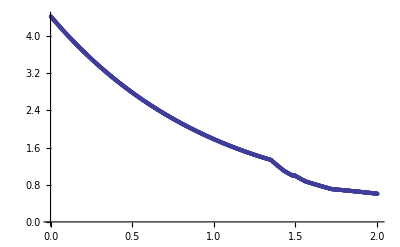

```mathematica
p3=ListPlot[tabT3]
```

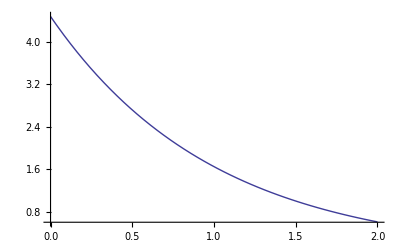

```mathematica
pd3=Plot[u1[x,1.5],{x,0,2}]
```

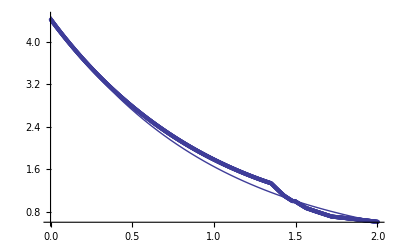

```mathematica
Show[pd3,p3]
```

### alfa = 1/2, t=2

```mathematica
str4=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,84]

```mathematica
strList4=ReadList[str4]
```

{7.35473,7.34085,7.32699,7.31316,7.29936,7.28559,7.27185,7.25813,7.24444,7.23078,7.21715,7.20354,7.18997,7.17641,7.16289,7.14939,7.13592,7.12248,7.10907,7.09568,7.08232,7.06898,7.05567,7.04239,7.02914,7.01591,7.00271,6.98954,6.97639,6.96327,6.95017,6.9371,6.92406,6.91105,6.89806,6.88509,6.87216,6.85925,6.84636,6.8335,6.82067,6.80787,6.79509,6.78233,6.7696,6.7569,6.74422,6.73157,6.71895,6.70635,6.69377,6.68122,6.6687,6.6562,6.64373,6.63128,6.61886,6.60646,6.59409,6.58174,6.56942,6.55712,6.54485,6.5326,6.52038,6.50818,6.49601,6.48386,6.47174,6.45964,6.44756,6.43551,6.42349,6.41149,6.39951,6.38756,6.37563,6.36373,6.35185,6.33999,6.32816,6.31635,6.30457,6.29281,6.28107,6.26936,6.25767,6.24601,6.23437,6.22275,6.21116,6.19959,6.18804,6.17652,6.16502,6.15354,6.14209,6.13066,6.11926,6.10787,6.09651,6.08518,6.07386,6.06257,6.05131,6.04006,6.02884,6.01764,6.00646,5.99531,5.98418,5.97307,5.96199,5.95093,5.93989,5.92887,5.91787,5.9069,5.89595,5.88502,5.87412,5.86323,5.85237,5.84154,5.83072,5.81992,5.80915,5.7984,5.78767,5.77697,5.76628,5.75562,5.74498,5.73436,5.72376,5.71319,5.70263,5.6921,5.68159,5.6711,5.66063,5.65019,5.63977,5.62936,5.61898,5.60862,5.59829,5.58797,5.57767,5.5674,5.55715,5.54692,5.53671,5.52652,5.51635,5.5062,5.49607,5.48597,5.47589,5.46582,5.45578,5.44576,5.43576,5.42577,5.41581,5.40588,5.39596,5.38606,5.37618,5.36632,5.35649,5.34667,5.33687,5.3271,5.31734,5.30761,5.29789,5.2882,5.27852,5.26887,5.25923,5.24962,5.24002,5.23045,5.22089,5.21136,5.20184,5.19235,5.18287,5.17341,5.16398,5.15456,5.14516,5.13578,5.12643,5.11709,5.10777,5.09847,5.08919,5.07993,5.07068,5.06146,5.05226,5.04307,5.03391,5.02476,5.01563,5.00653,4.99744,4.98837,4.97932,4.97029,4.96127,4.95228,4.9433,4.93435,4.92541,4.91649,4.90759,4.89871,4.88985,4.88101,4.87218,4.86338,4.85459,4.84582,4.83707,4.82834,4.81963,4.81093,4.80226,4.7936,4.78496,4.77634,4.76773,4.75915,4.75058,4.74203,4.7335,4.72499,4.7165,4.70802,4.69956,4.69112,4.6827,4.67429,4.66591,4.65754,4.64919,4.64085,4.63254,4.62424,4.61596,4.60769,4.59945,4.59122,4.58301,4.57482,4.56664,4.55848,4.55034,4.54222,4.53411,4.52603,4.51795,4.5099,4.50186,4.49384,4.48584,4.47785,4.46988,4.46193,4.454,4.44608,4.43818,4.4303,4.42243,4.41458,4.40675,4.39893,4.39113,4.38335,4.37559,4.36784,4.36011,4.35239,4.34469,4.33701,4.32935,4.3217,4.31407,4.30645,4.29886,4.29127,4.28371,4.27616,4.26863,4.26111,4.25361,4.24613,4.23866,4.23121,4.22378,4.21636,4.20896,4.20157,4.1942,4.18684,4.17951,4.17219,4.16488,4.15759,4.15032,4.14306,4.13582,4.12859,4.12138,4.11418,4.107,4.09984,4.09269,4.08556,4.07845,4.07135,4.06426,4.05719,4.05014,4.0431,4.03608,4.02907,4.02208,4.0151,4.00814,4.00119,3.99426,3.98735,3.98045,3.97356,3.96669,3.95984,3.953,3.94618,3.93937,3.93258,3.9258,3.91904,3.91229,3.90556,3.89884,3.89214,3.88545,3.87878,3.87212,3.86548,3.85886,3.85224,3.84565,3.83906,3.8325,3.82594,3.81941,3.81288,3.80637,3.79988,3.7934,3.78694,3.78049,3.77405,3.76763,3.76123,3.75483,3.74846,3.74209,3.73575,3.72941,3.72309,3.71679,3.7105,3.70422,3.69796,3.69171,3.68548,3.67926,3.67305,3.66686,3.66068,3.65452,3.64837,3.64224,3.63612,3.63001,3.62392,3.61784,3.61177,3.60572,3.59969,3.59366,3.58765,3.58166,3.57568,3.56971,3.56376,3.55782,3.5519,3.54598,3.54009,3.5342,3.52833,3.52248,3.51663,3.51081,3.50499,3.49919,3.4934,3.48763,3.48187,3.47612,3.47039,3.46467,3.45896,3.45327,3.44759,3.44192,3.43627,3.43063,3.425,3.41939,3.41379,3.4082,3.40263,3.39707,3.39152,3.38599,3.38047,3.37496,3.36947,3.36399,3.35852,3.35307,3.34763,3.3422,3.33678,3.33138,3.32599,3.32061,3.31525,3.3099,3.30456,3.29924,3.29392,3.28862,3.28334,3.27806,3.2728,3.26756,3.26232,3.2571,3.25189,3.24669,3.24151,3.23634,3.23118,3.22603,3.2209,3.21578,3.21067,3.20558,3.2005,3.19543,3.19037,3.18533,3.18029,3.17527,3.17027,3.16527,3.16029,3.15532,3.15036,3.14542,3.14049,3.13557,3.13066,3.12576,3.12088,3.11601,3.11115,3.1063,3.10147,3.09665,3.09184,3.08704,3.08226,3.07748,3.07272,3.06797,3.06323,3.05851,3.0538,3.0491,3.04441,3.03973,3.03506,3.03041,3.02577,3.02114,3.01652,3.01192,3.00732,3.00274,2.99817,2.99362,2.98907,2.98454,2.98001,2.9755,2.97101,2.96652,2.96205,2.95758,2.95313,2.94869,2.94427,2.93985,2.93545,2.93105,2.92667,2.92231,2.91795,2.9136,2.90927,2.90495,2.90064,2.89634,2.89205,2.88777,2.88351,2.87926,2.87501,2.87078,2.86657,2.86236,2.85816,2.85398,2.84981,2.84564,2.84149,2.83735,2.83323,2.82911,2.82501,2.82091,2.81683,2.81276,2.8087,2.80465,2.80061,2.79659,2.79257,2.78857,2.78457,2.78059,2.77662,2.77266,2.76871,2.76478,2.76085,2.75693,2.75303,2.74914,2.74526,2.74139,2.73753,2.73368,2.72984,2.72602,2.7222,2.7184,2.71461,2.71082,2.70705,2.70329,2.69954,2.69581,2.69208,2.68836,2.68466,2.68097,2.67728,2.67361,2.66995,2.6663,2.66266,2.65903,2.65541,2.6518,2.64821,2.64462,2.64104,2.63748,2.63393,2.63038,2.62685,2.62333,2.61982,2.61632,2.61283,2.60935,2.60588,2.60242,2.59897,2.59554,2.59211,2.58869,2.58529,2.58189,2.57851,2.57514,2.57177,2.56842,2.56508,2.56175,2.55842,2.55511,2.55181,2.54852,2.54525,2.54198,2.53872,2.53547,2.53223,2.52901,2.52579,2.52259,2.51939,2.51621,2.51303,2.50987,2.50671,2.50357,2.50044,2.49732,2.4942,2.4911,2.48801,2.48493,2.48186,2.4788,2.47575,2.47271,2.46968,2.46666,2.46365,2.46065,2.45766,2.45469,2.45172,2.44876,2.44581,2.44287,2.43995,2.43703,2.43412,2.43122,2.42834,2.42546,2.42259,2.41974,2.41689,2.41405,2.41123,2.40841,2.4056,2.40281,2.40002,2.39725,2.39448,2.39172,2.38898,2.38624,2.38351,2.3808,2.37809,2.37539,2.37271,2.37003,2.36736,2.36471,2.36206,2.35943,2.3568,2.35418,2.35158,2.34898,2.3464,2.34382,2.34125,2.3387,2.33615,2.33362,2.33109,2.32857,2.32607,2.32357,2.32108,2.31861,2.31614,2.31368,2.31124,2.3088,2.30637,2.30396,2.30155,2.29915,2.29676,2.29439,2.29202,2.28966,2.28731,2.28497,2.28264,2.28032,2.27801,2.27571,2.27342,2.27114,2.26887,2.26661,2.26436,2.26212,2.25989,2.25767,2.25545,2.25325,2.25106,2.24888,2.2467,2.24454,2.24238,2.24024,2.23811,2.23598,2.23386,2.23176,2.22966,2.22758,2.2255,2.22343,2.22137,2.21932,2.21729,2.21526,2.21324,2.21123,2.20923,2.20724,2.20526,2.20329,2.20133,2.19938,2.19744,2.19551,2.19359,2.19167,2.18977,2.18788,2.186,2.18412,2.18226,2.1804,2.17856,2.17673,2.1749,2.17309,2.17128,2.16948,2.1677,2.16592,2.16415,2.16239,2.16065,2.15891,2.15718,2.15546,2.15375,2.15205,2.15036,2.14868,2.14701,2.14534,2.14369,2.14205,2.14042,2.13879,2.13718,2.13557,2.13398,2.13239,2.13082,2.12925,2.12769,2.12615,2.12461,2.12308,2.12156,2.12005,2.11855,2.11706,2.11558,2.11411,2.11265,2.11119,2.10975,2.10832,2.10689,2.10548,2.10407,2.10268,2.10129,2.09992,2.09855,2.09719,2.09584,2.0945,2.09317,2.09185,2.09054,2.08924,2.08795,2.08667,2.0854,2.08414,2.08289,2.08164,2.08041,2.07919,2.07797,2.07677,2.07558,2.07439,2.07322,2.07205,2.07089,2.06975,2.06861,2.06748,2.06637,2.06526,2.06416,2.06307,2.06199,2.06092,2.05986,2.05881,2.05777,2.05674,2.05572,2.05471,2.05371,2.05271,2.05173,2.05076,2.0498,2.04884,2.0479,2.04696,2.04604,2.04512,2.04422,2.04332,2.04243,2.04156,2.04069,2.03983,2.03898,2.03814,2.03731,2.0365,2.03569,2.03489,2.03409,2.03331,2.03254,2.03178,2.03103,2.03029,2.02955,2.02883,2.02812,2.02741,2.02672,2.02604,2.02536,2.0247,2.02404,2.02339,2.02276,2.02213,2.02151,2.02091,2.02031,2.01972,2.01914,2.01857,2.01801,2.01747,2.01693,2.0164,2.01588,2.01536,2.01486,2.01437,2.01389,2.01342,2.01296,2.0125,2.01206,2.01163,2.0112,2.01079,2.01039,2.00999,2.00961,2.00923,2.00887,2.00851,2.00817,2.00783,2.0075,2.00719,2.00688,2.00658,2.0063,2.00602,2.00575,2.00549,2.00525,2.00501,2.00478,2.00457,2.00436,2.00416,2.00397,2.0038,2.00363,2.00347,2.00333,2.00319,2.00306,2.00295,2.00284,2.00274,2.00266,2.00258,2.00252,2.00246,2.00241,2.00238,2.00235,2.00234,2.00233,2.00234,2.00235,2.00238,2.00241,2.00246,2.00251,2.00258,2.00265,2.00274,2.00284,2.00294,2.00306,2.00319,2.00332,2.00347,2.00363,2.0038,2.00398,2.00416,2.00436,2.00457,2.00479,2.00502,2.00526,2.00551,2.00577,2.00604,2.00633,2.00662,2.00692,2.00723,2.00755,2.00789,2.00823,2.00859,2.00895,2.00932,2.00971,2.0101,2.01051,2.01093}

```mathematica
strList4={7.3547283574,7.3408453,7.3269902258,7.3131630752,7.2993637887,7.2855923069,7.2718485706,7.2581325207,7.2444440981,7.2307832439,7.2171498995,7.2035440061,7.1899655052,7.1764143387,7.16289045,7.1493937826,7.1359242802,7.1224818871,7.1090665488,7.0956782111,7.0823168197,7.0689823205,7.0556746596,7.0423937831,7.0291396372,7.0159121683,7.0027113229,6.9895370476,6.976389289,6.9632679939,6.9501731094,6.9371045823,6.9240623599,6.9110465831,6.8980571962,6.8850941439,6.8721573708,6.8592468218,6.8463624417,6.8335041756,6.8206719685,6.8078657659,6.7950855129,6.7823311551,6.7696026381,6.7568999075,6.7442229092,6.7315715891,6.7189458932,6.706345768,6.6937711634,6.6812220292,6.6686983161,6.6561999748,6.6437269562,6.6312792112,6.6188566909,6.6064593465,6.5940871292,6.5817399903,6.5694178813,6.5571207537,6.5448485593,6.5326012497,6.5203787769,6.5081810927,6.4960081492,6.4838598985,6.471736293,6.4596372849,6.4475628267,6.4355128709,6.4234873702,6.4114862773,6.399509545,6.3875571263,6.3756289741,6.3637250417,6.3518452822,6.3399896489,6.3281580953,6.3163505748,6.3045670412,6.2928074479,6.281071749,6.2693598982,6.2576718495,6.246007557,6.234366975,6.2227500575,6.2111567592,6.1995870343,6.1880408374,6.1765181232,6.1650188464,6.1535429619,6.1420904246,6.1306611895,6.1192552117,6.1078724464,6.096512849,6.0851763747,6.0738629792,6.0625726179,6.0513052466,6.040060821,6.0288392969,6.0176406303,6.0064647773,5.9953116939,5.9841813364,5.9730736611,5.9619886244,5.9509261827,5.9398862927,5.928868911,5.9178739944,5.9069014997,5.8959513839,5.885023604,5.8741181182,5.8632348857,5.8523738659,5.8415350182,5.830718302,5.8199236771,5.809151103,5.7984005396,5.7876719466,5.776965284,5.7662805118,5.7556175902,5.7449766398,5.7343576175,5.7237604807,5.7131851865,5.7026316922,5.6920999555,5.6815899336,5.6711015843,5.6606348653,5.6501897344,5.6397661494,5.6293640683,5.6189834491,5.6086242501,5.5982864295,5.5879699455,5.5776747566,5.5674008213,5.5571480982,5.546916546,5.5367061237,5.526516791,5.5163485077,5.5062012337,5.4960749287,5.4859695529,5.4758850663,5.4658214292,5.4557786017,5.4457565442,5.4357552171,5.4257745811,5.4158145965,5.4058752243,5.395956425,5.3860581596,5.376180389,5.3663230742,5.3564861763,5.3466696566,5.3368734762,5.3270975965,5.317341979,5.3076065851,5.2978913766,5.288196315,5.2785213621,5.2688664798,5.2592316299,5.2496167746,5.2400218759,5.2304468959,5.220891797,5.2113565414,5.2018410915,5.19234541,5.1828694593,5.1734132021,5.1639766011,5.1545596192,5.1451622193,5.1357843643,5.1264260173,5.1170871415,5.1077677,5.0984676561,5.089186974,5.0799256194,5.0706835578,5.0614607552,5.0522571774,5.0430727904,5.0339075602,5.024761453,5.0156344348,5.006526472,4.9974375308,4.9883677245,4.9793170159,4.9702853685,4.9612727455,4.9522791102,4.9433044261,4.9343486567,4.9254117658,4.9164937169,4.9075944738,4.8987140004,4.8898522607,4.8810092185,4.8721848382,4.8633790837,4.8545919194,4.8458233096,4.8370732186,4.8283416111,4.8196284514,4.8109337044,4.8022573346,4.793599307,4.7849595863,4.7763381384,4.7677349292,4.7591499245,4.7505830905,4.7420343933,4.7335037991,4.7249912742,4.7164967848,4.7080202975,4.6995617787,4.691121195,4.682698513,4.6742936995,4.6659067213,4.6575375452,4.6491861381,4.6408524672,4.6325364994,4.624238202,4.6159575422,4.6076944872,4.5994490046,4.5912210617,4.5830106261,4.5748176653,4.5666421471,4.5584840392,4.5503433094,4.5422199257,4.5341138559,4.5260250682,4.5179535306,4.5098992113,4.5018620805,4.4938421089,4.485839267,4.4778535257,4.4698848559,4.4619332282,4.4539986139,4.4460809837,4.438180309,4.4302967042,4.4224301371,4.4145805757,4.4067479878,4.3989323415,4.3911336047,4.3833517458,4.3755867328,4.367838534,4.3601071179,4.3523924529,4.3446945075,4.3370132503,4.3293486498,4.321700675,4.3140692944,4.3064544771,4.298856192,4.291274408,4.2837090944,4.2761602201,4.2686277545,4.2611116668,4.2536119265,4.2461285029,4.2386613656,4.2312104847,4.2237758309,4.2163573748,4.2089550869,4.2015689381,4.1941988992,4.186844941,4.1795070345,4.1721851508,4.1648792609,4.157589336,4.1503153472,4.143057266,4.1358150636,4.1285887114,4.1213781811,4.1141834441,4.107004472,4.0998412366,4.0926937096,4.0855618628,4.0784456682,4.0713450977,4.0642601233,4.0571907171,4.0501368514,4.0430984982,4.0360756312,4.029068225,4.0220762546,4.0150996947,4.0081385202,4.0011927061,3.9942622275,3.9873470594,3.9804471769,3.9735626953,3.9666935861,3.9598398213,3.9530013728,3.9461782125,3.9393703125,3.9325776448,3.9258001816,3.9190378952,3.9122907579,3.9055587421,3.8988418201,3.8921399645,3.8854531479,3.8787813429,3.8721245223,3.8654826587,3.858855725,3.8522436942,3.8456465392,3.839064233,3.8324967487,3.8259440596,3.8194061388,3.8128829597,3.8063744955,3.7998807198,3.7934016065,3.7869371301,3.7804872651,3.774051986,3.7676312676,3.7612250845,3.7548334115,3.7484562235,3.7420934954,3.7357452021,3.7294113187,3.7230918202,3.7167866818,3.7104958788,3.7042193864,3.6979571799,3.6917092347,3.6854755264,3.6792560304,3.6730507224,3.6668595779,3.6606825727,3.6545196826,3.6483708844,3.6422361566,3.6361154774,3.6300088254,3.6239161789,3.6178375166,3.611772817,3.6057220588,3.599685362,3.5936627018,3.5876540535,3.5816593924,3.5756786939,3.5697119334,3.5637590866,3.5578201289,3.5518950361,3.5459837838,3.5400863479,3.534202704,3.5283328283,3.5224766965,3.5166342849,3.5108055693,3.504990526,3.4991891313,3.4934013613,3.4876271924,3.481866601,3.4761195636,3.4703860567,3.4646660569,3.4589595408,3.4532664851,3.4475868666,3.4419206621,3.4362678485,3.4306284033,3.4250023044,3.4193895297,3.4137900574,3.4082038654,3.402630932,3.3970712354,3.3915247538,3.3859914655,3.3804713489,3.3749643826,3.3694705449,3.3639898145,3.3585221699,3.3530675899,3.3476260532,3.3421975385,3.3367820248,3.3313794909,3.3259899158,3.3206132792,3.3152495626,3.3098987476,3.3045608159,3.2992357492,3.2939235292,3.2886241377,3.2833375567,3.2780639091,3.2728031734,3.267555328,3.2623203514,3.2570982221,3.2518889188,3.2466924202,3.2415087049,3.2363377519,3.2311795399,3.226034048,3.220901255,3.21578114,3.2106736821,3.2055788605,3.2004966544,3.195427043,3.1903700058,3.185325522,3.1802935712,3.1752741328,3.1702671864,3.1652727117,3.1602906883,3.1553210959,3.1503639145,3.1454191237,3.1404867037,3.1355666342,3.1306588954,3.1257634679,3.1208803327,3.116009471,3.1111508639,3.1063044927,3.1014703385,3.0966483827,3.0918386067,3.0870409919,3.0822555199,3.0774821721,3.0727209301,3.0679717757,3.0632346904,3.0585096562,3.0537966547,3.0490956679,3.0444066777,3.0397296661,3.0350646175,3.0304115163,3.0257703474,3.0211410952,3.0165237447,3.0119182806,3.0073246876,3.0027430935,2.9981734796,2.9936158273,2.9890701179,2.9845363332,2.9800144546,2.9755044638,2.9710063425,2.9665200724,2.9620456354,2.9575830132,2.9531321879,2.9486931413,2.9442658556,2.9398503128,2.935446495,2.9310543845,2.9266739636,2.9223052145,2.9179481195,2.9136026612,2.9092688221,2.9049465845,2.9006359313,2.8963368449,2.8920493081,2.8877733036,2.8835088143,2.8792558231,2.8750143128,2.8707842665,2.8665656677,2.8623585004,2.8581627487,2.8539783965,2.8498054281,2.8456438275,2.8414935791,2.8373546671,2.8332270759,2.8291107898,2.8250057933,2.820912071,2.8168296072,2.8127583867,2.808698394,2.804649614,2.8006120313,2.7965856308,2.7925703986,2.788566322,2.7845733886,2.7805915859,2.7766209014,2.7726613229,2.768712838,2.7647755802,2.7608495338,2.7569346831,2.7530310124,2.7491385061,2.7452571486,2.7413869244,2.737527818,2.7336798141,2.7298428973,2.7260170523,2.7222022639,2.7183985169,2.7146057962,2.7108240867,2.7070533734,2.7032936413,2.6995448755,2.6958070612,2.6920801836,2.6883642279,2.6846591794,2.6809650236,2.6772817457,2.6736093313,2.6699477659,2.6662970351,2.6626571244,2.6590280197,2.6554097066,2.6518021709,2.6482053985,2.6446193757,2.6410440893,2.6374795262,2.6339256732,2.6303825174,2.6268500456,2.623328245,2.6198171026,2.6163166055,2.612826741,2.6093474963,2.6058788588,2.6024208156,2.5989733544,2.5955364624,2.5921101273,2.5886943365,2.5852890777,2.5818943385,2.5785101087,2.5751363786,2.5717731384,2.5684203787,2.5650780899,2.5617462623,2.5584248866,2.5551141009,2.5518138922,2.5485242478,2.5452451548,2.5419766007,2.5387185728,2.5354710585,2.5322340452,2.5290075205,2.5257914719,2.5225858871,2.5193907537,2.5162060595,2.5130317922,2.5098679397,2.5067144899,2.5035714307,2.5004387501,2.4973164362,2.4942044771,2.4911028608,2.4880115757,2.4849306099,2.4818599519,2.4787995899,2.4757495123,2.4727097077,2.4696801645,2.4666608714,2.4636518169,2.4606529897,2.4576643786,2.4546859725,2.4517177611,2.448759734,2.4458118809,2.4428741915,2.4399466557,2.4370292634,2.4341220043,2.4312248685,2.428337846,2.4254609268,2.4225941011,2.4197373589,2.4168906905,2.4140540861,2.4112275361,2.4084110307,2.4056045605,2.4028081158,2.4000216871,2.397245265,2.3944788412,2.3917224089,2.3889759613,2.3862394917,2.3835129935,2.3807964602,2.378089885,2.375393415,2.3727070403,2.3700307512,2.3673645379,2.3647083908,2.3620623004,2.359426257,2.3568002511,2.3541842734,2.3515783145,2.3489823649,2.3463964155,2.3438204569,2.3412544801,2.3386984759,2.3361524352,2.333616349,2.3310902084,2.3285740043,2.326067728,2.3235713706,2.3210849234,2.3186083777,2.3161417248,2.3136849561,2.311238063,2.308801037,2.3063738698,2.3039565529,2.3015490779,2.2991514365,2.2967636206,2.2943856219,2.2920174323,2.2896590445,2.2873104509,2.2849716443,2.2826426175,2.2803233631,2.278013874,2.275714143,2.2734241631,2.2711439273,2.2688734285,2.2666126598,2.2643616143,2.2621202852,2.2598886657,2.257666749,2.2554545285,2.2532519976,2.2510591496,2.248875978,2.2467024764,2.2445386382,2.2423844571,2.2402399267,2.2381050408,2.2359797931,2.2338641795,2.2317581965,2.2296618405,2.2275751082,2.2254979961,2.2234305008,2.2213726191,2.2193245075,2.2172861597,2.2152575693,2.2132387303,2.2112296364,2.2092302814,2.2072406595,2.2052607644,2.2032905904,2.2013301315,2.1993793818,2.1974383355,2.1955069869,2.1935853304,2.1916733602,2.1897710707,2.1878784565,2.185995512,2.1841222319,2.1822586106,2.180404643,2.1785603237,2.1767256475,2.1749006092,2.1730852037,2.1712794259,2.1694832708,2.1676967335,2.165919809,2.1641524924,2.162394779,2.160646664,2.1589081426,2.1571792102,2.1554598624,2.1537500949,2.1520499038,2.1503592851,2.1486782348,2.147006749,2.145344824,2.1436924559,2.1420496409,2.1404163755,2.1387926559,2.1371784786,2.1355738401,2.1339787368,2.1323931653,2.1308171222,2.1292506042,2.1276936081,2.1261461305,2.1246081683,2.1230797183,2.1215607775,2.1200513428,2.1185514113,2.11706098,2.115580046,2.1141086064,2.1126466586,2.1111941998,2.1097512272,2.1083177382,2.1068937304,2.105479201,2.1040741477,2.102678568,2.1012924612,2.0999158278,2.0985486682,2.0971909828,2.0958427723,2.0945040371,2.0931747779,2.0918549952,2.0905448631,2.0892443796,2.0879535428,2.0866723508,2.085400802,2.0841388947,2.0828866271,2.0816439977,2.080411005,2.0791876474,2.0779739234,2.0767698318,2.0755753711,2.0743905401,2.0732153375,2.0720497622,2.070893813,2.0697474889,2.0686107887,2.0674837116,2.0663662567,2.065258423,2.0641602097,2.0630716161,2.0619926415,2.0609232852,2.0598635466,2.0588134251,2.0577729202,2.0567420316,2.0557207587,2.0547091012,2.0537070589,2.0527146315,2.0517318188,2.0507586206,2.049795037,2.048841068,2.0478967138,2.0469619746,2.0460368506,2.0451213422,2.0442154497,2.0433191736,2.0424325143,2.0415554723,2.0406880482,2.0398302425,2.0389820561,2.0381434896,2.0373145438,2.0364952194,2.0356855175,2.0348854388,2.0340949845,2.0333141554,2.0325429528,2.0317813777,2.0310294314,2.030287115,2.0295544299,2.0288313773,2.0281179588,2.0274141757,2.0267200296,2.0260355219,2.0253606544,2.0246954286,2.0240398462,2.023393909,2.0227576189,2.0221309776,2.0215139871,2.0209066493,2.0203089663,2.0197209402,2.019142573,2.0185738669,2.0180148241,2.017465447,2.0169257378,2.0163956989,2.0158753328,2.0153646419,2.0148636288,2.0143722961,2.0138906463,2.0134186823,2.0129564067,2.0125038223,2.012060932,2.0116277386,2.0112042452,2.0107904547,2.0103863702,2.0099919948,2.0096073317,2.0092323864,2.0088671654,2.0085116747,2.0081659209,2.0078299103,2.0075036494,2.0071871445,2.0068804023,2.0065834293,2.006296232,2.0060190271,2.0057518194,2.005494614,2.0052474158,2.0050102301,2.0047830619,2.0045659165,2.0043587991,2.004161715,2.0039746696,2.0037976683,2.0036307166,2.00347382,2.0033269841,2.0031902144,2.0030635166,2.0029468965,2.0028403598,2.0027439124,2.0026575601,2.0025813089,2.0025151647,2.0024591335,2.0024132215,2.0023774347,2.0023517794,2.0023362617,2.002330888,2.0023356645,2.0023505977,2.002375694,2.0024109598,2.0024564018,2.0025120264,2.0025778403,2.0026538502,2.0027400629,2.002836485,2.0029431235,2.0030599853,2.0031870771,2.003324406,2.0034719784,2.003629801,2.0037978807,2.0039762241,2.0041648381,2.0043637295,2.0045729054,2.0047923726,2.0050221383,2.0052622095,2.0055125934,2.0057732971,2.006044328,2.0063256932,2.0066174002,2.0069194563,2.007231869,2.0075546458,2.0078877943,2.008231322,2.0085852367,2.008949546,2.0093242578,2.0097093797,2.0101049198,2.0105108858,2.0109272858};
```

```mathematica
tabT4=Table[{i*0.002,strList4[[i]]},{i,1,1001}];
```

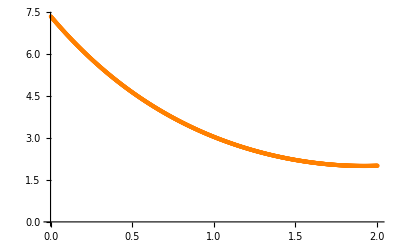

```mathematica
p4=ListPlot[tabT4,PlotStyle->Orange]
```

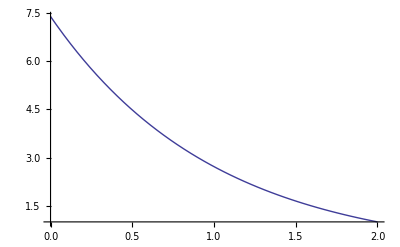

```mathematica
pd4=Plot[u1[x,2],{x,0,2}]
```

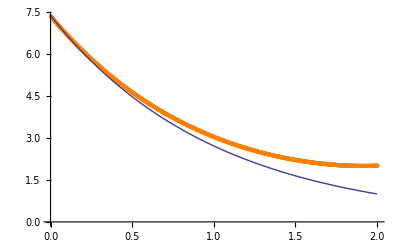

```mathematica
Show[p4,pd4]
```

### alfa = 8/10, t=1/2

```mathematica
str5=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,87]

```mathematica
strList5=ReadList[str5]
```

{1.55311,1.54996,1.54681,1.54366,1.54053,1.5374,1.53427,1.53116,1.52805,1.52494,1.52185,1.51876,1.51567,1.5126,1.50953,1.50647,1.50342,1.50037,1.49734,1.49431,1.49129,1.48827,1.48527,1.48227,1.47928,1.4763,1.47333,1.47037,1.46742,1.46447,1.46154,1.45861,1.45569,1.45279,1.44989,1.447,1.44412,1.44124,1.43838,1.43553,1.43268,1.42984,1.42702,1.4242,1.42139,1.41859,1.4158,1.41302,1.41025,1.40749,1.40474,1.40199,1.39926,1.39653,1.39382,1.39111,1.38841,1.38573,1.38305,1.38038,1.37772,1.37507,1.37243,1.3698,1.36718,1.36457,1.36197,1.35937,1.35679,1.35422,1.35165,1.34657,1.34004,1.33353,1.32703,1.32055,1.31408,1.30762,1.30117,1.29536,1.29055,1.28574,1.28095,1.27617,1.2714,1.26664,1.26188,1.25714,1.2524,1.24768,1.24296,1.23826,1.23356,1.22887,1.22419,1.21952,1.21485,1.2102,1.20555,1.20091,1.19628,1.19166,1.18705,1.18245,1.17785,1.17326,1.16868,1.16411,1.15954,1.15499,1.15044,1.1459,1.14136,1.13684,1.13232,1.1278,1.1233,1.1188,1.11431,1.10983,1.10535,1.10088,1.09642,1.09196,1.08751,1.08307,1.07864,1.07421,1.06978,1.06537,1.06096,1.05655,1.05215,1.04776,1.04337,1.03899,1.03462,1.03025,1.02589,1.02153,1.01718,1.01283,1.00849,1.00416,1,1,1,1,1,1,1,1,1,1,0.997893,0.995294,0.992697,0.9901,0.987505,0.984911,0.982318,0.979726,0.977135,0.974546,0.971957,0.969369,0.966782,0.964197,0.961612,0.959028,0.956445,0.953863,0.951282,0.948702,0.946122,0.943544,0.940966,0.938389,0.935813,0.933238,0.930663,0.92809,0.925517,0.922944,0.920373,0.917802,0.915232,0.912662,0.910093,0.907525,0.904957,0.90239,0.899824,0.897257,0.894692,0.892127,0.889562,0.886998,0.884435,0.881872,0.879309,0.876747,0.874185,0.871623,0.869062,0.866501,0.863941,0.86138,0.85882,0.85626,0.853701,0.851141,0.848582,0.846023,0.843464,0.840906,0.838347,0.835789,0.83323,0.832048,0.831389,0.830726,0.830059,0.829389,0.828715,0.828038,0.827357,0.826673,0.825986,0.825295,0.8246,0.823903,0.823202,0.822498,0.821791,0.82108,0.820367,0.81965,0.81893,0.818207,0.817481,0.816752,0.81602,0.815285,0.814547,0.813807,0.813063,0.812317,0.811567,0.810815,0.81006,0.809303,0.808543,0.80778,0.807014,0.806246,0.805475,0.804701,0.803925,0.803147,0.802366,0.801582,0.800796,0.800008,0.799217,0.798424,0.797629,0.796831,0.796031,0.795228,0.794424,0.793617,0.792808,0.791996,0.791183,0.790367,0.789549,0.78873,0.787908,0.787084,0.786258,0.78543,0.7846,0.783768,0.782934,0.782099,0.781261,0.780421,0.77958,0.778737,0.777892,0.777045,0.776196,0.775346,0.774494,0.77364,0.772785,0.771928,0.771069,0.770209,0.769347,0.768483,0.767618,0.766751,0.765883,0.765013,0.764142,0.76327,0.762395,0.76152,0.760643,0.759765,0.758885,0.758004,0.757121,0.756237,0.755352,0.754466,0.753578,0.752689,0.751799,0.750908,0.750015,0.749122,0.748227,0.747331,0.746433,0.745535,0.744636,0.743735,0.742833,0.741931,0.741027,0.740122,0.739217,0.73831,0.737402,0.736494,0.735584,0.734674,0.733762,0.73285,0.731937,0.731023,0.730108,0.729192,0.728275,0.727358,0.72644,0.725521,0.724601,0.72368,0.722759,0.721837,0.720914,0.719991,0.719067,0.718142,0.717217,0.716291,0.715364,0.714437,0.713509,0.71258,0.711651,0.710721,0.709791,0.70886,0.707929,0.706997,0.706065,0.705132,0.704199,0.703265,0.702331,0.701396,0.700461,0.699526,0.69859,0.697654,0.696717,0.69578,0.694843,0.693905,0.692967,0.692028,0.69109,0.69015,0.689211,0.688271,0.687332,0.686391,0.685451,0.68451,0.683569,0.682628,0.681687,0.680745,0.679804,0.678862,0.67792,0.676977,0.676035,0.675092,0.67415,0.673207,0.672264,0.671321,0.670378,0.669435,0.668491,0.667548,0.666605,0.665661,0.664718,0.663774,0.662831,0.661887,0.660944,0.66,0.659057,0.658113,0.65717,0.656226,0.655283,0.65434,0.653397,0.652453,0.65151,0.650567,0.649624,0.648682,0.647739,0.646796,0.645854,0.644912,0.643969,0.643027,0.642086,0.641144,0.640202,0.639261,0.63832,0.637379,0.636438,0.635498,0.634558,0.633618,0.632678,0.631738,0.630799,0.62986,0.628921,0.627982,0.627044,0.626106,0.625168,0.624231,0.623294,0.622357,0.62142,0.620484,0.619548,0.618613,0.617677,0.616743,0.615808,0.614874,0.61394,0.613007,0.612074,0.611141,0.610209,0.609277,0.608345,0.607414,0.606484,0.605553,0.604623,0.603694,0.602765,0.601836,0.600908,0.599981,0.599053,0.598127,0.5972,0.596274,0.595349,0.594424,0.5935,0.592576,0.591652,0.590729,0.589807,0.588885,0.587964,0.587043,0.586122,0.585202,0.584283,0.583364,0.582446,0.581528,0.580611,0.579694,0.578778,0.577863,0.576948,0.576033,0.57512,0.574206,0.573294,0.572382,0.57147,0.570559,0.569649,0.568739,0.56783,0.566922,0.566014,0.565107,0.5642,0.563294,0.562389,0.561484,0.56058,0.559676,0.558773,0.557871,0.55697,0.556069,0.555169,0.554269,0.55337,0.552472,0.551574,0.550677,0.549781,0.548886,0.547991,0.547097,0.546203,0.54531,0.544418,0.543527,0.542636,0.541746,0.540857,0.539968,0.53908,0.538193,0.537307,0.536421,0.535536,0.534652,0.533768,0.532885,0.532003,0.531122,0.530241,0.529361,0.528482,0.527604,0.526726,0.525849,0.524973,0.524098,0.523223,0.522349,0.521476,0.520604,0.519732,0.518861,0.517991,0.517122,0.516254,0.515386,0.514519,0.513653,0.512788,0.511923,0.511059,0.510196,0.509334,0.508473,0.507612,0.506752,0.505893,0.505035,0.504177,0.503321,0.502465,0.50161,0.500756,0.499903,0.49905,0.498198,0.497347,0.496497,0.495648,0.494799,0.493952,0.493105,0.492259,0.491414,0.490569,0.489726,0.488883,0.488041,0.4872,0.48636,0.485521,0.484682,0.483845,0.483008,0.482172,0.481337,0.480503,0.479669,0.478837,0.478005,0.477174,0.476344,0.475515,0.474686,0.473859,0.473032,0.472206,0.471381,0.470557,0.469734,0.468912,0.46809,0.46727,0.46645,0.465631,0.464813,0.463996,0.463179,0.462364,0.461549,0.460736,0.459923,0.459111,0.4583,0.45749,0.45668,0.455872,0.455064,0.454257,0.453451,0.452646,0.451842,0.451039,0.450237,0.449435,0.448635,0.447835,0.447036,0.446238,0.445441,0.444645,0.443849,0.443055,0.442261,0.441469,0.440677,0.439886,0.439096,0.438307,0.437518,0.436731,0.435944,0.435159,0.434374,0.43359,0.432807,0.432025,0.431244,0.430464,0.429684,0.428906,0.428128,0.427351,0.426575,0.4258,0.425026,0.424253,0.42348,0.422709,0.421938,0.421169,0.4204,0.419632,0.418865,0.418099,0.417334,0.416569,0.415806,0.415043,0.414281,0.413521,0.412761,0.412002,0.411243,0.410486,0.40973,0.408974,0.40822,0.407466,0.406713,0.405961,0.40521,0.40446,0.40371,0.402962,0.402214,0.401468,0.400722,0.399977,0.399233,0.39849,0.397748,0.397006,0.396266,0.395526,0.394787,0.39405,0.393313,0.392577,0.391841,0.391107,0.390374,0.389641,0.388909,0.388178,0.387449,0.386719,0.385991,0.385264,0.384538,0.383812,0.383087,0.382363,0.38164,0.380918,0.380197,0.379477,0.378757,0.378039,0.377321,0.376604,0.375888,0.375173,0.374459,0.373746,0.373033,0.372321,0.371611,0.370901,0.370192,0.369484,0.368776,0.36807,0.367364,0.366659,0.365955,0.365252,0.36455,0.363849,0.363149,0.362449,0.36175,0.361052,0.360355,0.359659,0.358964,0.358269,0.357576,0.356883,0.356191,0.3555,0.35481,0.35412,0.353432,0.352744,0.352057,0.351371,0.350686,0.350002,0.349318,0.348636,0.347954,0.347273,0.346593,0.345913,0.345235,0.344557,0.343881,0.343205,0.342529,0.341855,0.341182,0.340509,0.339837,0.339166,0.338496,0.337827,0.337158,0.336491,0.335824,0.335158,0.334492,0.333828,0.333165,0.332502,0.33184,0.331179,0.330518,0.329859,0.3292,0.328542,0.327885,0.327229,0.326573,0.325919,0.325265,0.324612,0.32396,0.323308,0.322658,0.322008,0.321359,0.32071,0.320063,0.319416,0.31877,0.318125,0.317481,0.316838,0.316195,0.315553,0.314912,0.314272,0.313632,0.312993,0.312355,0.311718,0.311082,0.310446,0.309811,0.309177,0.308544,0.307911,0.307279,0.306648,0.306018,0.305389,0.30476,0.304132,0.303505,0.302879,0.302253,0.301628,0.301004,0.300381,0.299758,0.299136,0.298515,0.297895,0.297275,0.296656,0.296038,0.295421,0.294804,0.294188,0.293573,0.292959,0.292345,0.291732,0.29112,0.290509,0.289898,0.289288,0.288679,0.288071,0.287463,0.286856,0.28625,0.285644,0.285039,0.284435,0.283832,0.283229,0.282627,0.282026,0.281426,0.280826,0.280227,0.279628,0.279031,0.278434,0.277838,0.277242,0.276647,0.276053,0.27546,0.274867,0.274275,0.273684,0.273093,0.272503,0.271914,0.271325,0.270738,0.27015,0.269564,0.268978,0.268393,0.267809,0.267225,0.266642,0.26606,0.265478,0.264897,0.264317,0.263737,0.263158,0.26258,0.262002,0.261425,0.260849,0.260273,0.259698,0.259124,0.25855,0.257977,0.257404,0.256833,0.256262,0.255691,0.255122,0.254552,0.253984,0.253416,0.252849,0.252282,0.251716,0.251151,0.250587,0.250023,0.249459,0.248896,0.248334,0.247773,0.247212,0.246652,0.246092,0.245533,0.244975,0.244417,0.24386,0.243304,0.242748,0.242192,0.241638,0.241084,0.24053,0.239977,0.239425,0.238874,0.238323,0.237772,0.237222,0.236673,0.236124,0.235576,0.235029,0.234482,0.233936,0.23339,0.232845,0.2323,0.231756,0.231213,0.23067,0.230128,0.229586,0.229045,0.228505,0.227965,0.227425,0.226886,0.226348,0.22581,0.225273,0.224737,0.224201,0.223665,0.22313}

```mathematica
strList5={1.5531117571,1.549956035,1.5468068286,1.5436641131,1.5405278637,1.5373980555,1.5342746686,1.5311578032,1.528047559,1.5249440359,1.5218473334,1.518757551,1.515674788,1.5125991435,1.5095310262,1.5064705265,1.5034177352,1.5003727427,1.4973356395,1.4943065158,1.491285462,1.4882725683,1.4852679249,1.4822716219,1.4792837494,1.4763043975,1.4733336563,1.4703716157,1.4674183659,1.4644739967,1.4615385892,1.4586121576,1.4556947161,1.4527862792,1.4498868613,1.446996477,1.444115141,1.4412428683,1.4383796738,1.4355255727,1.4326805801,1.4298447115,1.4270179823,1.4242004082,1.4213920049,1.4185927884,1.4158027745,1.4130219821,1.4102504303,1.4074881384,1.404735126,1.4019914126,1.399257018,1.3965319621,1.3938162648,1.3911099464,1.3884130272,1.3857255275,1.3830474681,1.3803788696,1.3777197529,1.3750701392,1.3724300496,1.3697995054,1.3671785282,1.3645671397,1.3619653617,1.3593732163,1.3567907255,1.3542179118,1.3516547978,1.3465654769,1.3400418835,1.3335315219,1.3270342665,1.3205499917,1.3140785724,1.3076198837,1.3011738012,1.2953559108,1.2905450348,1.2857439552,1.2809525968,1.276170879,1.2713987267,1.2666360652,1.2618828198,1.2571389159,1.2524042792,1.2476788355,1.2429625109,1.2382552315,1.2335569235,1.2288675134,1.2241869279,1.2195150936,1.2148519375,1.2101973867,1.2055513683,1.2009138097,1.1962846383,1.1916637818,1.1870511679,1.1824467246,1.1778503799,1.1732620619,1.1686816989,1.1641092194,1.159544552,1.1549876252,1.1504383679,1.1458967091,1.1413625777,1.136835903,1.1323166142,1.1278046407,1.1232999121,1.1188023579,1.1143119079,1.109828492,1.1053520401,1.1008824822,1.0964197485,1.0919637692,1.0875144748,1.0830717957,1.0786356624,1.0742060056,1.069782756,1.0653658444,1.0609552018,1.0565507592,1.0521524477,1.0477601984,1.0433739426,1.0389936117,1.034619137,1.0302504501,1.0258874826,1.021530166,1.0171784322,1.0128322128,1.0084914398,1.0041560451,1,1,1,1,1,1,1,1,1,1,0.9978928277,0.9952942396,0.9926968017,0.9901004989,0.9875053164,0.984911239,0.9823182517,0.9797263393,0.9771354864,0.9745456777,0.9719568977,0.9693691309,0.9667823618,0.9641965746,0.9616117536,0.959027883,0.9564449467,0.9538629288,0.9512818133,0.948701584,0.9461222245,0.9435437186,0.9409660499,0.9383892019,0.9358131581,0.9332379017,0.930663416,0.9280896842,0.9255166895,0.9229444148,0.920372843,0.9178019571,0.9152317398,0.9126621737,0.9100932415,0.9075249257,0.9049572087,0.9023900729,0.8998235005,0.8972574737,0.8946919746,0.8921269853,0.8895624875,0.8869984632,0.8844348942,0.881871762,0.8793090482,0.8767467344,0.8741848019,0.8716232321,0.8690620062,0.8665011052,0.8639405103,0.8613802025,0.8588201625,0.8562603712,0.8537008093,0.8511414573,0.8485822958,0.8460233053,0.8434644659,0.840905758,0.8383471617,0.835788657,0.833230224,0.8320482721,0.8313888278,0.8307257626,0.8300591086,0.8293888979,0.8287151623,0.8280379333,0.8273572424,0.8266731208,0.8259855996,0.8252947095,0.8246004812,0.8239029451,0.8232021316,0.8224980708,0.8217907924,0.8210803263,0.820366702,0.8196499488,0.8189300959,0.8182071723,0.8174812068,0.816752228,0.8160202644,0.8152853442,0.8145474956,0.8138067466,0.8130631247,0.8123166577,0.811567373,0.8108152977,0.810060459,0.8093028838,0.8085425987,0.8077796305,0.8070140054,0.8062457498,0.8054748896,0.8047014508,0.8039254592,0.8031469404,0.8023659198,0.8015824225,0.8007964739,0.8000080988,0.799217322,0.7984241682,0.7976286618,0.7968308272,0.7960306886,0.79522827,0.7944235952,0.7936166881,0.7928075721,0.7919962707,0.7911828073,0.7903672048,0.7895494864,0.7887296748,0.7879077928,0.7870838629,0.7862579075,0.7854299489,0.7846000092,0.7837681104,0.7829342744,0.7820985228,0.7812608772,0.780421359,0.7795799897,0.7787367902,0.7778917816,0.7770449849,0.7761964207,0.7753461098,0.7744940725,0.7736403293,0.7727849003,0.7719278058,0.7710690655,0.7702086995,0.7693467273,0.7684831687,0.767618043,0.7667513695,0.7658831676,0.7650134562,0.7641422543,0.7632695809,0.7623954545,0.7615198938,0.7606429172,0.7597645432,0.75888479,0.7580036756,0.757121218,0.7562374353,0.755352345,0.7544659649,0.7535783125,0.7526894052,0.7517992604,0.7509078951,0.7500153266,0.7491215717,0.7482266473,0.7473305702,0.746433357,0.7455350242,0.7446355882,0.7437350654,0.7428334719,0.7419308239,0.7410271373,0.740122428,0.7392167117,0.7383100043,0.7374023211,0.7364936777,0.7355840895,0.7346735716,0.7337621394,0.7328498077,0.7319365916,0.7310225059,0.7301075654,0.7291917847,0.7282751784,0.7273577609,0.7264395467,0.7255205499,0.7246007848,0.7236802654,0.7227590058,0.7218370197,0.720914321,0.7199909234,0.7190668404,0.7181420857,0.7172166726,0.7162906144,0.7153639244,0.7144366158,0.7135087016,0.7125801947,0.7116511081,0.7107214546,0.7097912468,0.7088604973,0.7079292188,0.7069974236,0.7060651242,0.7051323327,0.7041990614,0.7032653224,0.7023311277,0.7013964893,0.7004614189,0.6995259285,0.6985900296,0.6976537339,0.696717053,0.6957799982,0.6948425809,0.6939048125,0.6929667041,0.6920282669,0.6910895119,0.6901504501,0.6892110925,0.6882714498,0.6873315327,0.6863913521,0.6854509183,0.6845102421,0.6835693338,0.6826282038,0.6816868623,0.6807453197,0.6798035861,0.6788616715,0.677919586,0.6769773395,0.6760349418,0.6750924028,0.6741497322,0.6732069397,0.6722640347,0.671321027,0.6703779258,0.6694347405,0.6684914806,0.6675481552,0.6666047735,0.6656613445,0.6647178775,0.6637743813,0.6628308648,0.6618873369,0.6609438064,0.660000282,0.6590567723,0.658113286,0.6571698315,0.6562264173,0.6552830518,0.6543397435,0.6533965004,0.6524533309,0.6515102431,0.6505672451,0.6496243449,0.6486815506,0.6477388699,0.6467963108,0.6458538811,0.6449115884,0.6439694406,0.6430274451,0.6420856096,0.6411439415,0.6402024483,0.6392611375,0.6383200162,0.6373790919,0.6364383716,0.6354978627,0.6345575722,0.6336175071,0.6326776745,0.6317380813,0.6307987344,0.6298596406,0.6289208068,0.6279822396,0.6270439458,0.626105932,0.6251682047,0.6242307705,0.6232936359,0.6223568072,0.6214202909,0.6204840933,0.6195482206,0.6186126791,0.617677475,0.6167426143,0.6158081032,0.6148739476,0.6139401536,0.6130067271,0.612073674,0.611141,0.610208711,0.6092768128,0.608345311,0.6074142112,0.6064835191,0.6055532403,0.6046233802,0.6036939442,0.6027649379,0.6018363666,0.6009082357,0.5999805503,0.5990533158,0.5981265373,0.5972002201,0.5962743691,0.5953489895,0.5944240864,0.5934996646,0.5925757292,0.591652285,0.5907293369,0.5898068897,0.5888849482,0.5879635171,0.5870426012,0.5861222049,0.5852023331,0.5842829902,0.5833641807,0.5824459093,0.5815281802,0.580610998,0.579694367,0.5787782916,0.577862776,0.5769478245,0.5760334413,0.5751196307,0.5742063967,0.5732937435,0.5723816751,0.5714701956,0.570559309,0.5696490193,0.5687393303,0.567830246,0.5669217701,0.5660139067,0.5651066593,0.5642000318,0.5632940279,0.5623886513,0.5614839056,0.5605797944,0.5596763213,0.5587734899,0.5578713035,0.5569697659,0.5560688803,0.5551686501,0.5542690789,0.5533701698,0.5524719263,0.5515743515,0.5506774488,0.5497812213,0.5488856723,0.5479908049,0.5470966221,0.5462031272,0.5453103232,0.544418213,0.5435267998,0.5426360863,0.5417460757,0.5408567708,0.5399681745,0.5390802896,0.5381931189,0.5373066653,0.5364209314,0.5355359201,0.534651634,0.5337680758,0.5328852482,0.5320031537,0.531121795,0.5302411745,0.529361295,0.5284821587,0.5276037683,0.5267261262,0.5258492348,0.5249730965,0.5240977136,0.5232230886,0.5223492237,0.5214761212,0.5206037834,0.5197322126,0.5188614108,0.5179913804,0.5171221235,0.5162536422,0.5153859387,0.514519015,0.5136528731,0.5127875152,0.5119229432,0.5110591591,0.510196165,0.5093339626,0.508472554,0.507611941,0.5067521255,0.5058931094,0.5050348944,0.5041774824,0.5033208751,0.5024650743,0.5016100817,0.5007558991,0.499902528,0.4990499703,0.4981982274,0.4973473011,0.4964971929,0.4956479044,0.4947994371,0.4939517926,0.4931049724,0.4922589779,0.4914138107,0.4905694722,0.4897259637,0.4888832868,0.4880414428,0.487200433,0.4863602588,0.4855209215,0.4846824224,0.4838447628,0.483007944,0.4821719672,0.4813368335,0.4805025443,0.4796691007,0.4788365039,0.4780047549,0.477173855,0.4763438052,0.4755146067,0.4746862604,0.4738587675,0.4730321289,0.4722063457,0.4713814189,0.4705573494,0.4697341383,0.4689117863,0.4680902946,0.4672696639,0.4664498952,0.4656309893,0.4648129471,0.4639957694,0.4631794571,0.4623640108,0.4615494315,0.4607357199,0.4599228767,0.4591109026,0.4582997984,0.4574895648,0.4566802025,0.4558717121,0.4550640943,0.4542573496,0.4534514789,0.4526464825,0.4518423612,0.4510391154,0.4502367458,0.4494352529,0.4486346372,0.4478348993,0.4470360395,0.4462380585,0.4454409566,0.4446447343,0.4438493921,0.4430549303,0.4422613494,0.4414686498,0.4406768318,0.4398858958,0.4390958421,0.4383066712,0.4375183832,0.4367309786,0.4359444575,0.4351588203,0.4343740673,0.4335901986,0.4328072146,0.4320251154,0.4312439013,0.4304635725,0.429684129,0.4289055712,0.4281278992,0.4273511131,0.426575213,0.425800199,0.4250260714,0.42425283,0.4234804752,0.4227090068,0.421938425,0.4211687298,0.4203999212,0.4196319993,0.418864964,0.4180988154,0.4173335534,0.416569178,0.4158056892,0.4150430869,0.4142813711,0.4135205416,0.4127605983,0.4120015413,0.4112433703,0.4104860853,0.4097296861,0.4089741726,0.4082195445,0.4074658018,0.4067129443,0.4059609717,0.405209884,0.4044596807,0.4037103619,0.4029619271,0.4022143762,0.401467709,0.400721925,0.3999770242,0.3992330062,0.3984898706,0.3977476172,0.3970062458,0.3962657558,0.3955261471,0.3947874193,0.394049572,0.3933126048,0.3925765175,0.3918413095,0.3911069805,0.3903735301,0.3896409579,0.3889092635,0.3881784464,0.3874485062,0.3867194424,0.3859912546,0.3852639423,0.3845375051,0.3838119424,0.3830872537,0.3823634386,0.3816404966,0.380918427,0.3801972294,0.3794769032,0.378757448,0.378038863,0.3773211479,0.3766043019,0.3758883245,0.3751732151,0.3744589732,0.373745598,0.3730330891,0.3723214457,0.3716106672,0.370900753,0.3701917025,0.3694835149,0.3687761897,0.3680697261,0.3673641235,0.3666593811,0.3659554984,0.3652524745,0.3645503087,0.3638490004,0.3631485489,0.3624489533,0.3617502129,0.361052327,0.3603552949,0.3596591157,0.3589637887,0.3582693132,0.3575756882,0.3568829131,0.3561909871,0.3554999092,0.3548096788,0.354120295,0.3534317569,0.3527440638,0.3520572147,0.3513712088,0.3506860454,0.3500017234,0.3493182421,0.3486356006,0.3479537979,0.3472728333,0.3465927057,0.3459134143,0.3452349583,0.3445573365,0.3438805483,0.3432045925,0.3425294683,0.3418551748,0.3411817109,0.3405090758,0.3398372684,0.3391662879,0.3384961332,0.3378268034,0.3371582974,0.3364906143,0.3358237531,0.3351577128,0.3344924924,0.3338280908,0.333164507,0.3325017401,0.3318397889,0.3311786525,0.3305183298,0.3298588197,0.3292001212,0.3285422333,0.3278851548,0.3272288847,0.3265734219,0.3259187654,0.325264914,0.3246118666,0.3239596222,0.3233081796,0.3226575378,0.3220076956,0.3213586519,0.3207104055,0.3200629554,0.3194163004,0.3187704394,0.3181253711,0.3174810946,0.3168376085,0.3161949118,0.3155530032,0.3149118817,0.3142715459,0.3136319948,0.3129932272,0.3123552418,0.3117180375,0.311081613,0.3104459672,0.3098110988,0.3091770067,0.3085436895,0.3079111462,0.3072793753,0.3066483758,0.3060181463,0.3053886857,0.3047599926,0.3041320658,0.3035049041,0.3028785062,0.3022528708,0.3016279966,0.3010038824,0.3003805269,0.2997579288,0.2991360868,0.2985149997,0.297894666,0.2972750846,0.296656254,0.296038173,0.2954208403,0.2948042546,0.2941884145,0.2935733186,0.2929589657,0.2923453545,0.2917324835,0.2911203514,0.2905089569,0.2898982986,0.2892883752,0.2886791852,0.2880707274,0.2874630003,0.2868560027,0.2862497329,0.2856441898,0.285039372,0.2844352779,0.2838319063,0.2832292557,0.2826273247,0.2820261119,0.2814256159,0.2808258353,0.2802267687,0.2796284146,0.2790307716,0.2784338383,0.2778376132,0.2772420949,0.276647282,0.2760531729,0.2754597663,0.2748670607,0.2742750546,0.2736837466,0.2730931352,0.272503219,0.2719139964,0.2713254659,0.2707376262,0.2701504757,0.2695640128,0.2689782363,0.2683931444,0.2678087357,0.2672250088,0.2666419621,0.2660595941,0.2654779033,0.2648968881,0.2643165471,0.2637368787,0.2631578813,0.2625795536,0.2620018938,0.2614249005,0.2608485721,0.2602729071,0.2596979039,0.259123561,0.2585498768,0.2579768497,0.2574044783,0.2568327608,0.2562616957,0.2556912816,0.2551215167,0.2545523995,0.2539839284,0.2534161018,0.2528489181,0.2522823758,0.2517164731,0.2511512086,0.2505865806,0.2500225875,0.2494592277,0.2488964995,0.2483344014,0.2477729317,0.2472120887,0.2466518709,0.2460922766,0.2455333042,0.244974952,0.2444172184,0.2438601018,0.2433036004,0.2427477126,0.2421924368,0.2416377713,0.2410837144,0.2405302644,0.2399774198,0.2394251787,0.2388735396,0.2383225007,0.2377720604,0.2372222169,0.2366729686,0.2361243137,0.2355762506,0.2350287776,0.2344818929,0.2339355949,0.2333898818,0.2328447518,0.2323002034,0.2317562347,0.231212844,0.2306700297,0.2301277898,0.2295861228,0.2290450269,0.2285045003,0.2279645412,0.227425148,0.2268863188,0.226348052,0.2258103457,0.2252731981,0.2247366076,0.2242005722,0.2236650904,0.2231301601};
```

```mathematica
tabT5=Table[{i*0.002,strList5[[i]]},{i,1,1001}];
```

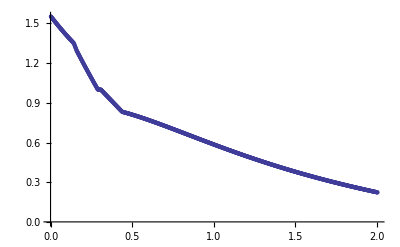

```mathematica
p5=ListPlot[tabT5]
```

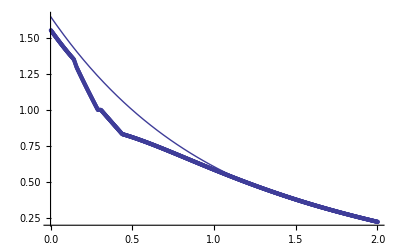

```mathematica
Show[pd1,p5]
```

### alfa = 8/10, t=1

```mathematica
str6=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,89]

```mathematica
strList6=ReadList[str6]
```

{2.68819,2.68292,2.67765,2.6724,2.66715,2.66192,2.6567,2.65148,2.64628,2.64109,2.6359,2.63073,2.62557,2.62041,2.61527,2.61014,2.60502,2.5999,2.5948,2.58971,2.58463,2.57956,2.5745,2.56945,2.56441,2.55938,2.55435,2.54934,2.54434,2.53935,2.53437,2.5294,2.52444,2.51949,2.51454,2.50961,2.50469,2.49978,2.49487,2.48998,2.48509,2.48022,2.47536,2.4705,2.46565,2.46082,2.45599,2.45117,2.44637,2.44157,2.43678,2.432,2.42723,2.42247,2.41772,2.41297,2.40824,2.40352,2.3988,2.39409,2.3894,2.38471,2.38003,2.37536,2.3707,2.36605,2.36141,2.35678,2.35215,2.34754,2.34293,2.33833,2.33375,2.32917,2.3246,2.32003,2.31548,2.31094,2.3064,2.30188,2.29736,2.29285,2.28835,2.28386,2.27938,2.2749,2.27044,2.26598,2.26154,2.2571,2.25267,2.24825,2.24384,2.23944,2.23504,2.23066,2.22628,2.22192,2.21756,2.21321,2.20887,2.20454,2.20021,2.1959,2.19159,2.18729,2.183,2.17872,2.17445,2.17018,2.16593,2.16168,2.15744,2.15321,2.14899,2.14477,2.14057,2.13637,2.13218,2.128,2.12383,2.11966,2.11551,2.11136,2.10722,2.10309,2.09896,2.09485,2.09074,2.08664,2.08255,2.07847,2.07439,2.07033,2.06627,2.06221,2.05817,2.05413,2.05011,2.04609,2.04208,2.03807,2.03407,2.03009,2.0261,2.02213,2.01817,2.01421,2.01026,2.00632,2.00238,1.99845,1.99453,1.99062,1.98672,1.98282,1.97893,1.97505,1.97118,1.96731,1.96346,1.95961,1.95576,1.95193,1.9481,1.94428,1.94047,1.93667,1.93287,1.92908,1.9253,1.92153,1.91776,1.914,1.91025,1.90651,1.90277,1.89905,1.89532,1.89161,1.8879,1.8842,1.88051,1.87683,1.87315,1.86948,1.86582,1.86216,1.85851,1.85487,1.85124,1.84761,1.84399,1.84038,1.83678,1.83318,1.82959,1.826,1.82242,1.81885,1.81529,1.81174,1.80819,1.80464,1.80111,1.79758,1.79406,1.79054,1.78704,1.78354,1.78004,1.77655,1.77307,1.7696,1.76613,1.76267,1.75922,1.75577,1.75233,1.7489,1.74547,1.74205,1.73864,1.73524,1.73184,1.72845,1.72506,1.72169,1.71831,1.71495,1.71159,1.70824,1.7049,1.70156,1.69823,1.69491,1.69159,1.68828,1.68497,1.68168,1.67839,1.6751,1.67182,1.66855,1.66529,1.66203,1.65878,1.65553,1.65229,1.64906,1.64583,1.64261,1.6394,1.63619,1.63299,1.6298,1.62661,1.62343,1.62026,1.61709,1.61392,1.61077,1.60762,1.60447,1.60133,1.5982,1.59508,1.59196,1.58884,1.58574,1.58264,1.57954,1.57645,1.57337,1.57029,1.56722,1.56415,1.5611,1.55804,1.555,1.55196,1.54892,1.5459,1.54288,1.53986,1.53685,1.53385,1.53085,1.52786,1.52488,1.5219,1.51892,1.51596,1.513,1.51004,1.5071,1.50415,1.50122,1.49829,1.49536,1.49244,1.48953,1.48662,1.48372,1.48083,1.47794,1.47505,1.47218,1.4693,1.46644,1.46358,1.46072,1.45787,1.45503,1.45219,1.44936,1.44654,1.44371,1.4409,1.43809,1.43529,1.43249,1.4297,1.42691,1.42413,1.42135,1.41858,1.41582,1.41306,1.4103,1.40756,1.40481,1.40208,1.39935,1.39663,1.39391,1.3912,1.3885,1.3858,1.38311,1.38043,1.37776,1.37509,1.37243,1.36977,1.36712,1.36448,1.36185,1.35922,1.3566,1.35399,1.35139,1.34879,1.3462,1.34362,1.34104,1.33847,1.33591,1.33336,1.33082,1.32828,1.32575,1.32323,1.32071,1.3182,1.3157,1.31321,1.31073,1.30825,1.30579,1.30333,1.30088,1.29843,1.296,1.29357,1.29115,1.28874,1.28634,1.28394,1.28156,1.27653,1.26956,1.26261,1.25567,1.24875,1.24184,1.23494,1.22806,1.22119,1.21433,1.20749,1.20066,1.19515,1.19023,1.18531,1.1804,1.1755,1.17061,1.16573,1.16085,1.15599,1.15113,1.14628,1.14144,1.13661,1.13178,1.12697,1.12216,1.11736,1.11256,1.10778,1.103,1.09823,1.09347,1.08872,1.08397,1.07923,1.0745,1.06977,1.06505,1.06034,1.05564,1.05094,1.04625,1.04157,1.03689,1.03222,1.02755,1.0229,1.01824,1.0136,1.00896,1.00433,1,1,1,1,1,1,1,1,0.998139,0.993381,0.988628,0.983881,0.979139,0.975489,0.97272,0.969953,0.967187,0.964423,0.96166,0.958898,0.956138,0.953379,0.950622,0.947866,0.945111,0.942357,0.939605,0.936854,0.934104,0.931356,0.928608,0.925862,0.923117,0.920373,0.917631,0.914889,0.912148,0.909409,0.90667,0.903933,0.901196,0.898461,0.895726,0.892992,0.890259,0.887528,0.884797,0.882066,0.879337,0.876609,0.873881,0.871154,0.868428,0.865702,0.862977,0.860253,0.85753,0.854807,0.852085,0.849363,0.846642,0.843922,0.841202,0.838482,0.835763,0.833045,0.830994,0.830245,0.829492,0.828736,0.827977,0.827215,0.826449,0.82568,0.824908,0.824133,0.823355,0.822573,0.821789,0.821002,0.820211,0.819418,0.818622,0.817823,0.817021,0.816216,0.815408,0.814598,0.813785,0.812969,0.81215,0.811329,0.810505,0.809678,0.808849,0.808017,0.807183,0.806346,0.805507,0.804665,0.80382,0.802974,0.802125,0.801273,0.80042,0.799563,0.798705,0.797844,0.796981,0.796116,0.795249,0.79438,0.793508,0.792634,0.791758,0.79088,0.79,0.789118,0.788234,0.787348,0.78646,0.78557,0.784678,0.783784,0.782888,0.781991,0.781092,0.78019,0.779287,0.778383,0.777476,0.776568,0.775658,0.774746,0.773833,0.772918,0.772001,0.771083,0.770163,0.769242,0.768319,0.767394,0.766468,0.765541,0.764612,0.763682,0.76275,0.761817,0.760882,0.759946,0.759008,0.75807,0.75713,0.756188,0.755246,0.754302,0.753357,0.75241,0.751462,0.750514,0.749564,0.748612,0.74766,0.746707,0.745752,0.744796,0.74384,0.742882,0.741923,0.740963,0.740002,0.73904,0.738077,0.737113,0.736148,0.735183,0.734216,0.733248,0.73228,0.73131,0.73034,0.729369,0.728397,0.727424,0.726451,0.725476,0.724501,0.723525,0.722548,0.721571,0.720593,0.719614,0.718635,0.717654,0.716674,0.715692,0.71471,0.713727,0.712744,0.71176,0.710775,0.70979,0.708804,0.707818,0.706831,0.705844,0.704856,0.703868,0.702879,0.70189,0.7009,0.69991,0.698919,0.697928,0.696937,0.695945,0.694953,0.69396,0.692967,0.691974,0.69098,0.689986,0.688992,0.687997,0.687002,0.686007,0.685012,0.684016,0.68302,0.682024,0.681027,0.68003,0.679034,0.678036,0.677039,0.676041,0.675044,0.674046,0.673048,0.67205,0.671051,0.670053,0.669054,0.668056,0.667057,0.666058,0.665059,0.66406,0.663061,0.662062,0.661063,0.660064,0.659065,0.658066,0.657066,0.656067,0.655068,0.654069,0.65307,0.65207,0.651071,0.650072,0.649073,0.648074,0.647076,0.646077,0.645078,0.64408,0.643081,0.642083,0.641085,0.640087,0.639089,0.638091,0.637093,0.636096,0.635099,0.634101,0.633105,0.632108,0.631111,0.630115,0.629119,0.628123,0.627127,0.626132,0.625136,0.624141,0.623147,0.622152,0.621158,0.620164,0.61917,0.618177,0.617184,0.616191,0.615198,0.614206,0.613214,0.612223,0.611231,0.61024,0.60925,0.60826,0.60727,0.60628,0.605291,0.604302,0.603314,0.602325,0.601338,0.60035,0.599363,0.598377,0.597391,0.596405,0.59542,0.594435,0.59345,0.592466,0.591483,0.590499,0.589517,0.588534,0.587553,0.586571,0.58559,0.58461,0.58363,0.58265,0.581671,0.580692,0.579714,0.578737,0.57776,0.576783,0.575807,0.574831,0.573856,0.572882,0.571907,0.570934,0.569961,0.568988,0.568016,0.567045,0.566074,0.565104,0.564134,0.563165,0.562196,0.561228,0.56026,0.559293,0.558327,0.557361,0.556396,0.555431,0.554467,0.553503,0.55254,0.551578,0.550616,0.549655,0.548695,0.547735,0.546775,0.545816,0.544858,0.543901,0.542944,0.541987,0.541032,0.540077,0.539122,0.538169,0.537215,0.536263,0.535311,0.53436,0.533409,0.532459,0.53151,0.530561,0.529613,0.528666,0.527719,0.526773,0.525827,0.524883,0.523939,0.522995,0.522052,0.52111,0.520169,0.519228,0.518288,0.517349,0.51641,0.515472,0.514535,0.513598,0.512662,0.511727,0.510792,0.509858,0.508925,0.507992,0.50706,0.506129,0.505199,0.504269,0.50334,0.502412,0.501484,0.500557,0.499631,0.498705,0.49778,0.496856,0.495933,0.49501,0.494088,0.493167,0.492246,0.491326,0.490407,0.489489,0.488571,0.487654,0.486737,0.485822,0.484907,0.483993,0.483079,0.482167,0.481255,0.480343,0.479433,0.478523,0.477614,0.476705,0.475798,0.474891,0.473984,0.473079,0.472174,0.47127,0.470367,0.469464,0.468562,0.467661,0.466761,0.465861,0.464962,0.464064,0.463166,0.462269,0.461373,0.460478,0.459583,0.458689,0.457796,0.456903,0.456012,0.455121,0.45423,0.453341,0.452452,0.451564,0.450676,0.44979,0.448904,0.448018,0.447134,0.44625,0.445367,0.444485,0.443603,0.442722,0.441842,0.440962,0.440084,0.439205,0.438328,0.437451,0.436576,0.4357,0.434826,0.433952,0.433079,0.432207,0.431335,0.430464,0.429594,0.428724,0.427855,0.426987,0.42612,0.425253,0.424387,0.423522,0.422657,0.421793,0.42093,0.420067,0.419205,0.418344,0.417484,0.416624,0.415765,0.414906,0.414049,0.413192,0.412335,0.41148,0.410625,0.40977,0.408917,0.408064,0.407211,0.40636,0.405509,0.404658,0.403809,0.40296,0.402112,0.401264,0.400417,0.399571,0.398725,0.39788,0.397036,0.396192,0.395349,0.394506,0.393665,0.392824,0.391983,0.391143,0.390304,0.389466,0.388628,0.38779,0.386954,0.386118,0.385282,0.384448,0.383613,0.38278,0.381947,0.381115,0.380283,0.379452,0.378621,0.377792,0.376962,0.376134,0.375306,0.374478,0.373651,0.372825,0.371999,0.371174,0.37035,0.369526,0.368702,0.367879}

```mathematica
strList6={2.6881900817,2.6829152556,2.677650726,2.6723964652,2.667152446,2.6619186409,2.6566950229,2.6514815706,2.6462782629,2.6410850784,2.635901996,2.6307289946,2.625566053,2.6204131502,2.6152705747,2.6101382971,2.6050162884,2.5999045192,2.5948029606,2.5897115836,2.584630359,2.5795592579,2.5744982516,2.5694473111,2.5644064077,2.5593755127,2.5543545973,2.549343633,2.5443425912,2.5393514434,2.5343701614,2.5293987204,2.5244370953,2.5194852613,2.5145431935,2.509610867,2.5046882572,2.4997753393,2.4948720886,2.4899784804,2.4850944903,2.4802200935,2.4753552658,2.4704999825,2.4656542193,2.4608179518,2.4559911556,2.4511738082,2.4463658873,2.4415673704,2.4367782355,2.4319984603,2.4272280226,2.4224669003,2.4177150714,2.4129725137,2.4082392052,2.4035151241,2.3988002482,2.3940945558,2.3893980249,2.3847106338,2.3800323606,2.3753631836,2.370703081,2.3660520312,2.3614100125,2.3567770033,2.3521529821,2.3475379272,2.3429318172,2.3383346307,2.3337463489,2.3291669551,2.3245964323,2.3200347637,2.3154819325,2.3109379218,2.3064027149,2.3018762951,2.2973586457,2.2928497498,2.2883495906,2.283858448,2.2793763003,2.2749031255,2.2704389019,2.2659836077,2.2615372212,2.2570997209,2.252671085,2.248251292,2.2438403204,2.2394381486,2.2350447552,2.2306601188,2.226284218,2.2219170314,2.2175585379,2.213208716,2.2088675446,2.2045350025,2.2002110686,2.1958957217,2.1915889408,2.1872907048,2.1830009928,2.1787197839,2.174447057,2.1701827913,2.1659269661,2.1616795603,2.1574405534,2.1532099246,2.1489876532,2.1447737185,2.1405680999,2.1363707769,2.1321817288,2.1280009353,2.1238283757,2.1196640297,2.1155078769,2.1113598969,2.1072200693,2.1030883739,2.0989647905,2.0948492987,2.0907418785,2.0866425096,2.0825511719,2.0784678454,2.07439251,2.0703251457,2.0662657324,2.0622142503,2.0581706794,2.0541349999,2.0501071919,2.0460872356,2.0420751112,2.038070799,2.0340742792,2.0300855321,2.0261045382,2.0221312778,2.018165735,2.0142078952,2.010257744,2.0063152672,2.0023804503,1.9984532789,1.9945337388,1.9906218157,1.9867174953,1.9828210258,1.9789323875,1.9750515606,1.9711785254,1.9673132623,1.9634557516,1.9596059738,1.9557639094,1.9519295387,1.9481028424,1.944283801,1.9404723951,1.9366686053,1.9328724123,1.9290837968,1.9253027395,1.9215292212,1.9177632227,1.9140047249,1.9102537085,1.9065101546,1.9027740441,1.8990453578,1.895324077,1.8916101825,1.8879036554,1.8842044769,1.8805126281,1.8768280902,1.8731508444,1.8694808719,1.8658181539,1.8621626719,1.8585144071,1.8548733408,1.8512394546,1.8476127297,1.8439931478,1.8403806902,1.8367753385,1.8331770742,1.8295858789,1.8260017344,1.822424622,1.8188545237,1.815291421,1.8117352958,1.8081861297,1.8046439046,1.8011086023,1.7975802046,1.7940586935,1.7905440508,1.7870362586,1.7835352987,1.7800411574,1.7765538227,1.7730732825,1.7695995248,1.7661325375,1.7626723086,1.7592188263,1.7557720784,1.7523323034,1.7488994822,1.7454735964,1.7420546283,1.73864256,1.7352373737,1.7318390515,1.7284475758,1.7250629288,1.7216850929,1.7183140503,1.7149497834,1.7115922747,1.7082415065,1.7048974614,1.7015601218,1.6982294702,1.6949054891,1.6915881613,1.6882774691,1.6849733954,1.6816759228,1.6783850338,1.6751007114,1.6718229381,1.6685516969,1.6652869704,1.6620287416,1.6587769932,1.6555317082,1.6522928695,1.64906046,1.6458344627,1.6426148605,1.6394016365,1.6361947738,1.6329942553,1.6298000643,1.6266121837,1.6234305969,1.6202552869,1.6170862369,1.6139234301,1.6107668499,1.6076164794,1.6044723021,1.6013343011,1.5982024598,1.5950767617,1.5919571901,1.5888437284,1.5857363621,1.582635083,1.5795398828,1.5764507535,1.5733676867,1.5702906744,1.5672197082,1.5641547801,1.5610961245,1.5580437262,1.5549975695,1.5519576392,1.5489239195,1.5458963949,1.5428750498,1.5398598688,1.5368508361,1.5338479364,1.5308511539,1.5278604733,1.5248758788,1.5218973549,1.518924886,1.5159584566,1.512998051,1.5100436536,1.5070952489,1.5041528211,1.5012163546,1.4982858338,1.4953612429,1.4924425663,1.4895297882,1.4866228929,1.4837218646,1.4808266876,1.477937346,1.4750538239,1.4721761055,1.469304175,1.4664380163,1.4635776135,1.4607229506,1.4578740116,1.4550307805,1.452193241,1.4493613772,1.4465351727,1.4437146114,1.4408996771,1.4380903533,1.4352866239,1.4324884723,1.4296958821,1.4269088369,1.4241273201,1.4213513152,1.418580856,1.4158160313,1.4130569293,1.4103036382,1.4075562461,1.4048148409,1.4020795102,1.3993503415,1.3966276564,1.3939115348,1.3912020567,1.3884992924,1.3858032807,1.3831140602,1.3804316696,1.3777561473,1.375087532,1.3724258623,1.3697711766,1.3671235136,1.3644829118,1.3618494097,1.3592230459,1.3566038589,1.3539918872,1.3513871695,1.3487897443,1.3461996502,1.3436169258,1.3410416098,1.3384737407,1.3359133574,1.3333604984,1.3308152026,1.3282775086,1.3257474554,1.3232250817,1.3207104266,1.3182035288,1.3157044274,1.3132131615,1.31072977,1.3082542923,1.3057867675,1.3033272347,1.3008757335,1.2984323032,1.2959969833,1.2935698132,1.2911508327,1.2887400813,1.286337599,1.2839434256,1.2815576009,1.2765304661,1.269564014,1.2626117108,1.2556734222,1.2487490142,1.2418383529,1.2349413047,1.2280577364,1.221187515,1.2143304753,1.2074864848,1.200655411,1.1951547352,1.1902277732,1.1853097772,1.1804006709,1.1755003782,1.1706088231,1.1657259297,1.1608516223,1.1559858253,1.151128463,1.1462794602,1.1414387416,1.1366062319,1.1317818563,1.1269655396,1.1221572072,1.1173567842,1.1125641962,1.1077793685,1.1030022268,1.0982326967,1.0934707041,1.0887161749,1.083969035,1.0792292105,1.0744966277,1.0697712127,1.065052892,1.0603415919,1.0556372389,1.0509397598,1.0462490811,1.0415651297,1.0368878323,1.032217116,1.0275529076,1.0228951343,1.0182437232,1.0135986014,1.0089596963,1.0043269352,1,1,1,1,1,1,1,1,0.9981392177,0.9933809005,0.9886281455,0.9838808781,0.9791390231,0.9754887551,0.9727200281,0.9699527774,0.9671869847,0.9644226313,0.9616596987,0.9588981682,0.9561380211,0.9533792384,0.9506218015,0.9478656912,0.9451108885,0.9423573744,0.9396051296,0.9368541349,0.9341043709,0.9313558183,0.9286084576,0.9258622691,0.9231172333,0.9203733305,0.9176305408,0.9148888444,0.9121482214,0.9094086518,0.9066701154,0.903932592,0.9011960615,0.8984605035,0.8957258976,0.8929922232,0.8902594599,0.8875275869,0.8847965837,0.8820664292,0.8793371027,0.8766085831,0.8738808495,0.8711538806,0.8684276553,0.8657021523,0.8629773501,0.8602532274,0.8575297624,0.8548069337,0.8520847195,0.849363098,0.8466420472,0.8439215452,0.84120157,0.8384820993,0.835763111,0.8330445827,0.8309940159,0.8302447586,0.8294921593,0.8287362489,0.827977058,0.8272146171,0.8264489565,0.8256801063,0.8249080964,0.8241329566,0.8233547162,0.8225734048,0.8217890515,0.8210016852,0.8202113349,0.819418029,0.8186217962,0.8178226646,0.8170206623,0.8162158174,0.8154081575,0.8145977101,0.8137845028,0.8129685628,0.8121499171,0.8113285926,0.810504616,0.8096780139,0.8088488127,0.8080170385,0.8071827176,0.8063458757,0.8055065386,0.8046647319,0.8038204809,0.8029738109,0.8021247471,0.8012733142,0.8004195372,0.7995634406,0.7987050489,0.7978443863,0.7969814771,0.7961163451,0.7952490144,0.7943795085,0.7935078509,0.7926340651,0.7917581744,0.7908802017,0.7900001701,0.7891181023,0.788234021,0.7873479487,0.7864599077,0.7855699203,0.7846780085,0.7837841943,0.7828884994,0.7819909455,0.7810915541,0.7801903465,0.7792873441,0.7783825678,0.7774760387,0.7765677775,0.775657805,0.7747461417,0.773832808,0.7729178241,0.7720012103,0.7710829865,0.7701631727,0.7692417886,0.7683188538,0.7673943878,0.76646841,0.7655409396,0.7646119958,0.7636815974,0.7627497635,0.7618165128,0.7608818637,0.7599458349,0.7590084448,0.7580697114,0.7571296531,0.7561882878,0.7552456333,0.7543017075,0.7533565279,0.7524101122,0.7514624777,0.7505136417,0.7495636215,0.748612434,0.7476600962,0.746706625,0.745752037,0.744796349,0.7438395773,0.7428817384,0.7419228485,0.7409629239,0.7400019804,0.7390400342,0.7380771011,0.7371131967,0.7361483367,0.7351825366,0.7342158118,0.7332481776,0.7322796492,0.7313102417,0.7303399701,0.7293688493,0.7283968941,0.727424119,0.7264505388,0.7254761679,0.7245010207,0.7235251114,0.7225484542,0.7215710632,0.7205929524,0.7196141357,0.7186346268,0.7176544395,0.7166735872,0.7156920837,0.7147099421,0.7137271759,0.7127437982,0.7117598222,0.7107752609,0.7097901272,0.7088044339,0.7078181939,0.7068314198,0.7058441241,0.7048563193,0.7038680179,0.702879232,0.701889974,0.7009002559,0.6999100898,0.6989194876,0.6979284612,0.6969370224,0.6959451828,0.6949529541,0.6939603478,0.6929673753,0.6919740479,0.690980377,0.6899863737,0.6889920491,0.6879974142,0.6870024801,0.6860072574,0.6850117571,0.6840159898,0.6830199662,0.6820236966,0.6810271918,0.6800304619,0.6790335173,0.6780363683,0.677039025,0.6760414974,0.6750437955,0.6740459293,0.6730479087,0.6720497433,0.6710514428,0.670053017,0.6690544753,0.6680558271,0.667057082,0.6660582492,0.665059338,0.6640603576,0.663061317,0.6620622253,0.6610630915,0.6600639245,0.6590647331,0.658065526,0.657066312,0.6560670997,0.6550678975,0.6540687141,0.6530695578,0.6520704369,0.6510713598,0.6500723347,0.6490733696,0.6480744727,0.6470756521,0.6460769156,0.6450782711,0.6440797265,0.6430812895,0.6420829679,0.6410847691,0.6400867009,0.6390887707,0.638090986,0.6370933541,0.6360958824,0.635098578,0.6341014483,0.6331045003,0.6321077411,0.6311111778,0.6301148172,0.6291186664,0.628122732,0.6271270209,0.6261315399,0.6251362955,0.6241412943,0.623146543,0.622152048,0.6211578157,0.6201638525,0.6191701648,0.6181767587,0.6171836405,0.6161908163,0.6151982923,0.6142060744,0.6132141687,0.612222581,0.6112313173,0.6102403834,0.6092497851,0.608259528,0.6072696178,0.6062800602,0.6052908607,0.6043020247,0.6033135578,0.6023254654,0.6013377528,0.6003504253,0.5993634881,0.5983769465,0.5973908056,0.5964050705,0.5954197462,0.5944348378,0.5934503502,0.5924662883,0.5914826569,0.5904994609,0.589516705,0.5885343939,0.5875525324,0.5865711248,0.585590176,0.5846096903,0.5836296723,0.5826501264,0.5816710569,0.5806924682,0.5797143645,0.5787367502,0.5777596294,0.5767830063,0.5758068849,0.5748312694,0.5738561638,0.5728815719,0.5719074978,0.5709339454,0.5699609184,0.5689884208,0.5680164561,0.5670450283,0.5660741408,0.5651037974,0.5641340017,0.5631647571,0.5621960673,0.5612279356,0.5602603654,0.5592933602,0.5583269233,0.557361058,0.5563957675,0.5554310551,0.5544669239,0.5535033771,0.5525404178,0.5515780489,0.5506162736,0.5496550949,0.5486945156,0.5477345386,0.5467751669,0.5458164032,0.5448582503,0.543900711,0.542943788,0.541987484,0.5410318016,0.5400767433,0.5391223118,0.5381685096,0.5372153391,0.5362628028,0.5353109032,0.5343596425,0.5334090232,0.5324590475,0.5315097177,0.5305610361,0.5296130048,0.5286656261,0.5277189019,0.5267728345,0.5258274259,0.524882678,0.523938593,0.5229951727,0.5220524191,0.521110334,0.5201689193,0.5192281769,0.5182881084,0.5173487158,0.5164100006,0.5154719645,0.5145346093,0.5135979365,0.5126619478,0.5117266446,0.5107920285,0.509858101,0.5089248636,0.5079923176,0.5070604645,0.5061293056,0.5051988423,0.5042690759,0.5033400075,0.5024116385,0.5014839701,0.5005570035,0.4996307397,0.4987051799,0.4977803252,0.4968561766,0.4959327352,0.495010002,0.4940879778,0.4931666637,0.4922460605,0.4913261692,0.4904069905,0.4894885253,0.4885707743,0.4876537384,0.4867374182,0.4858218144,0.4849069278,0.4839927589,0.4830793083,0.4821665767,0.4812545646,0.4803432725,0.4794327009,0.4785228503,0.4776137211,0.4767053138,0.4757976287,0.4748906662,0.4739844266,0.4730789102,0.4721741173,0.4712700482,0.470366703,0.4694640819,0.4685621853,0.467661013,0.4667605654,0.4658608424,0.4649618441,0.4640635706,0.4631660219,0.4622691979,0.4613730986,0.460477724,0.4595830738,0.4586891481,0.4577959467,0.4569034693,0.4560117158,0.455120686,0.4542303795,0.4533407962,0.4524519358,0.4515637978,0.4506763819,0.4497896878,0.4489037151,0.4480184632,0.4471339319,0.4462501205,0.4453670286,0.4444846557,0.4436030012,0.4427220645,0.441841845,0.4409623421,0.4400835552,0.4392054835,0.4383281263,0.4374514831,0.4365755528,0.435700335,0.4348258286,0.4339520329,0.433078947,0.4322065702,0.4313349014,0.4304639398,0.4295936844,0.4287241343,0.4278552885,0.4269871459,0.4261197055,0.4252529663,0.4243869272,0.4235215871,0.4226569448,0.4217929992,0.4209297492,0.4200671934,0.4192053308,0.41834416,0.4174836799,0.416623889,0.4157647861,0.4149063698,0.4140486389,0.4131915918,0.4123352272,0.4114795437,0.4106245399,0.4097702142,0.4089165651,0.4080635911,0.4072112908,0.4063596625,0.4055087046,0.4046584155,0.4038087937,0.4029598374,0.4021115449,0.4012639147,0.4004169448,0.3995706337,0.3987249795,0.3978799805,0.3970356348,0.3961919406,0.3953488961,0.3945064993,0.3936647485,0.3928236415,0.3919831766,0.3911433518,0.390304165,0.3894656142,0.3886276975,0.3877904127,0.3869537578,0.3861177307,0.3852823293,0.3844475514,0.3836133948,0.3827798575,0.3819469371,0.3811146314,0.3802829383,0.3794518553,0.3786213803,0.3777915109,0.3769622447,0.3761335794,0.3753055127,0.374478042,0.3736511651,0.3728248794,0.3719991824,0.3711740718,0.3703495448,0.3695255992,0.3687022321,0.3678794412};
```

```mathematica
tabT6=Table[{i*0.002,strList6[[i]]},{i,1,1001}];
```

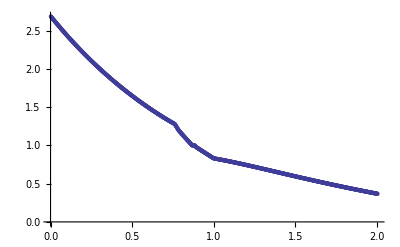

```mathematica
p6=ListPlot[tabT6]
```

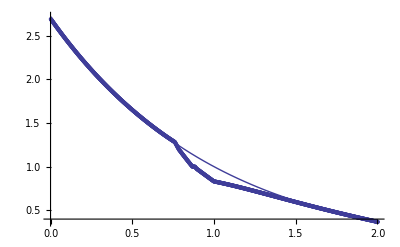

```mathematica
Show[pd2,p6]
```

### alfa = 8/10, t=1.5

```mathematica
str7=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,90]

```mathematica
strList7=ReadList[str7]
```

{4.46946,4.46071,4.45196,4.44324,4.43454,4.42585,4.41717,4.40852,4.39988,4.39126,4.38265,4.37406,4.36549,4.35694,4.3484,4.33988,4.33138,4.32289,4.31442,4.30597,4.29753,4.28911,4.28071,4.27232,4.26395,4.2556,4.24726,4.23894,4.23064,4.22235,4.21408,4.20583,4.19759,4.18936,4.18116,4.17297,4.16479,4.15664,4.1485,4.14037,4.13226,4.12417,4.11609,4.10803,4.09998,4.09195,4.08394,4.07594,4.06795,4.05999,4.05203,4.0441,4.03618,4.02827,4.02038,4.01251,4.00465,3.9968,3.98898,3.98116,3.97337,3.96558,3.95782,3.95006,3.94233,3.93461,3.9269,3.91921,3.91153,3.90387,3.89622,3.88859,3.88097,3.87337,3.86578,3.85821,3.85065,3.84311,3.83558,3.82807,3.82057,3.81308,3.80561,3.79816,3.79072,3.78329,3.77588,3.76849,3.76111,3.75374,3.74639,3.73905,3.73173,3.72442,3.71713,3.70985,3.70258,3.69533,3.68809,3.68087,3.67367,3.66647,3.65929,3.65213,3.64498,3.63784,3.63072,3.62361,3.61652,3.60944,3.60237,3.59532,3.58828,3.58125,3.57424,3.56725,3.56026,3.55329,3.54634,3.5394,3.53247,3.52555,3.51865,3.51177,3.50489,3.49803,3.49119,3.48435,3.47753,3.47073,3.46393,3.45715,3.45039,3.44363,3.43689,3.43017,3.42345,3.41675,3.41006,3.40339,3.39673,3.39008,3.38344,3.37682,3.37021,3.36362,3.35703,3.35046,3.3439,3.33736,3.33083,3.32431,3.3178,3.31131,3.30482,3.29835,3.2919,3.28546,3.27903,3.27261,3.2662,3.25981,3.25343,3.24707,3.24071,3.23437,3.22804,3.22173,3.21543,3.20913,3.20286,3.19659,3.19034,3.1841,3.17787,3.17165,3.16545,3.15926,3.15308,3.14691,3.14075,3.13461,3.12848,3.12236,3.11625,3.11016,3.10408,3.09801,3.09195,3.0859,3.07987,3.07384,3.06783,3.06183,3.05585,3.04987,3.04391,3.03796,3.03201,3.02609,3.02017,3.01426,3.00837,3.00249,2.99662,2.99076,2.98491,2.97907,2.97325,2.96743,2.96163,2.95584,2.95006,2.94429,2.93854,2.93279,2.92706,2.92133,2.91562,2.90992,2.90423,2.89855,2.89289,2.88723,2.88159,2.87596,2.87034,2.86473,2.85913,2.85354,2.84796,2.8424,2.83684,2.8313,2.82577,2.82025,2.81474,2.80924,2.80375,2.79827,2.7928,2.78735,2.7819,2.77647,2.77105,2.76563,2.76023,2.75484,2.74946,2.74409,2.73873,2.73338,2.72804,2.72271,2.7174,2.71209,2.70679,2.70151,2.69623,2.69097,2.68571,2.68047,2.67523,2.67001,2.6648,2.65959,2.6544,2.64922,2.64405,2.63888,2.63373,2.62859,2.62346,2.61833,2.61322,2.60812,2.60303,2.59795,2.59287,2.58781,2.58276,2.57772,2.57269,2.56767,2.56266,2.55766,2.55266,2.54768,2.54271,2.53775,2.5328,2.52786,2.52293,2.51801,2.51309,2.50819,2.5033,2.49842,2.49354,2.48868,2.48383,2.47898,2.47415,2.46933,2.46451,2.4597,2.45491,2.45012,2.44535,2.44058,2.43582,2.43107,2.42633,2.4216,2.41688,2.41217,2.40747,2.40278,2.39809,2.39342,2.38876,2.3841,2.37945,2.37482,2.37019,2.36557,2.36096,2.35636,2.35177,2.34718,2.34261,2.33804,2.33349,2.32894,2.3244,2.31987,2.31536,2.31084,2.30634,2.30185,2.29737,2.29289,2.28843,2.28397,2.27953,2.27509,2.27066,2.26624,2.26183,2.25742,2.25303,2.24864,2.24427,2.2399,2.23554,2.23119,2.22685,2.22252,2.21819,2.21388,2.20957,2.20527,2.20098,2.1967,2.19243,2.18816,2.18391,2.17966,2.17542,2.17119,2.16697,2.16275,2.15855,2.15435,2.15016,2.14598,2.14181,2.13765,2.13349,2.12934,2.1252,2.12107,2.11695,2.11283,2.10873,2.10463,2.10054,2.09646,2.09238,2.08832,2.08426,2.08021,2.07617,2.07213,2.06811,2.06409,2.06008,2.05608,2.05209,2.04811,2.04413,2.04016,2.0362,2.03225,2.0283,2.02437,2.02044,2.01652,2.0126,2.0087,2.0048,2.00091,1.99703,1.99316,1.98929,1.98543,1.98158,1.97774,1.97391,1.97008,1.96626,1.96245,1.95864,1.95484,1.95106,1.94727,1.9435,1.93973,1.93597,1.93222,1.92848,1.92474,1.92101,1.91729,1.91357,1.90987,1.90617,1.90248,1.89879,1.89511,1.89144,1.88778,1.88412,1.88047,1.87683,1.8732,1.86957,1.86596,1.86234,1.85874,1.85514,1.85156,1.84797,1.8444,1.84083,1.83727,1.83372,1.83017,1.82664,1.8231,1.81958,1.81606,1.81255,1.80905,1.80556,1.80207,1.79859,1.79511,1.79164,1.78818,1.78473,1.78129,1.77785,1.77441,1.77099,1.76757,1.76416,1.76075,1.75735,1.75396,1.75058,1.7472,1.74383,1.74047,1.73711,1.73376,1.73042,1.72708,1.72375,1.72042,1.71711,1.7138,1.71049,1.7072,1.7039,1.70062,1.69734,1.69407,1.69081,1.68755,1.6843,1.68106,1.67782,1.67459,1.67137,1.66815,1.66494,1.66174,1.65854,1.65535,1.65217,1.64899,1.64582,1.64266,1.6395,1.63635,1.63321,1.63007,1.62694,1.62381,1.62069,1.61758,1.61447,1.61137,1.60828,1.60519,1.60211,1.59904,1.59597,1.59291,1.58985,1.5868,1.58376,1.58072,1.57769,1.57467,1.57165,1.56864,1.56563,1.56263,1.55964,1.55665,1.55367,1.55069,1.54772,1.54476,1.5418,1.53885,1.5359,1.53296,1.53003,1.52711,1.52419,1.52127,1.51836,1.51546,1.51257,1.50968,1.50679,1.50391,1.50104,1.49818,1.49532,1.49247,1.48962,1.48678,1.48394,1.48111,1.47829,1.47547,1.47266,1.46986,1.46706,1.46426,1.46147,1.45869,1.45592,1.45315,1.45038,1.44762,1.44487,1.44212,1.43938,1.43665,1.43392,1.43119,1.42847,1.42576,1.42305,1.42035,1.41766,1.41497,1.41228,1.4096,1.40693,1.40426,1.4016,1.39894,1.39629,1.39365,1.39101,1.38838,1.38576,1.38314,1.38053,1.37793,1.37534,1.37275,1.37017,1.36759,1.36502,1.36246,1.35991,1.35736,1.35483,1.35229,1.34977,1.34725,1.34474,1.34224,1.33975,1.33726,1.33478,1.33231,1.32985,1.32739,1.32495,1.32251,1.32007,1.31765,1.31523,1.31283,1.31043,1.30803,1.30565,1.30327,1.3009,1.29855,1.29619,1.29385,1.29152,1.28919,1.28687,1.28456,1.28226,1.27746,1.27062,1.26378,1.25697,1.25016,1.24338,1.2366,1.22984,1.2231,1.21636,1.20964,1.20294,1.19624,1.19138,1.18659,1.1818,1.17702,1.17226,1.1675,1.16275,1.158,1.15327,1.14855,1.14383,1.13913,1.13443,1.12974,1.12506,1.12038,1.11572,1.11106,1.10641,1.10177,1.09714,1.09251,1.0879,1.08329,1.07869,1.07409,1.06951,1.06493,1.06035,1.05579,1.05123,1.04668,1.04214,1.0376,1.03307,1.02855,1.02403,1.01953,1.01502,1.01053,1.00604,1.00156,1,1,1,1,1,1,1,0.998421,0.993816,0.989217,0.984624,0.980037,0.976544,0.973882,0.971221,0.968562,0.965905,0.963249,0.960596,0.957943,0.955293,0.952644,0.949997,0.947352,0.944708,0.942065,0.939424,0.936785,0.934147,0.931511,0.928876,0.926243,0.923611,0.920981,0.918352,0.915724,0.913098,0.910473,0.90785,0.905227,0.902606,0.899987,0.897368,0.894751,0.892135,0.889521,0.886907,0.884295,0.881683,0.879073,0.876464,0.873856,0.871249,0.868644,0.866039,0.863435,0.860832,0.85823,0.855629,0.85303,0.85043,0.847832,0.845235,0.842638,0.840043,0.837448,0.834854,0.832261,0.829668,0.827879,0.827136,0.82639,0.82564,0.824887,0.824132,0.823372,0.82261,0.821845,0.821076,0.820305,0.81953,0.818752,0.817972,0.817188,0.816401,0.815612,0.814819,0.814024,0.813226,0.812425,0.811621,0.810815,0.810005,0.809193,0.808378,0.807561,0.806741,0.805918,0.805093,0.804265,0.803434,0.802601,0.801766,0.800928,0.800087,0.799244,0.798399,0.797551,0.796701,0.795848,0.794994,0.794136,0.793277,0.792415,0.791551,0.790684,0.789816,0.788945,0.788072,0.787197,0.78632,0.78544,0.784559,0.783675,0.78279,0.781902,0.781012,0.780121,0.779227,0.778331,0.777433,0.776534,0.775632,0.774729,0.773824,0.772916,0.772007,0.771096,0.770184,0.769269,0.768353,0.767435,0.766515,0.765593,0.76467,0.763745,0.762818,0.76189,0.76096,0.760028,0.759095,0.75816,0.757224,0.756286,0.755346,0.754405,0.753462,0.752518,0.751572,0.750624,0.749676,0.748725,0.747774,0.74682,0.745866,0.74491,0.743952,0.742993,0.742033,0.741072,0.740109,0.739144,0.738179,0.737212,0.736244,0.735274,0.734303,0.733331,0.732358,0.731383,0.730407,0.72943,0.728452,0.727472,0.726491,0.725509,0.724526,0.723542,0.722557,0.72157,0.720582,0.719594,0.718604,0.717613,0.71662,0.715627,0.714633,0.713638,0.712641,0.711644,0.710645,0.709645,0.708645,0.707643,0.706641,0.705637,0.704632,0.703627,0.70262,0.701613,0.700604,0.699595,0.698584,0.697573,0.69656,0.695547,0.694533,0.693518,0.692502,0.691485,0.690467,0.689449,0.688429,0.687409,0.686388,0.685365,0.684342,0.683319,0.682294,0.681268,0.680242,0.679215,0.678187,0.677158,0.676128,0.675098,0.674067,0.673035,0.672002,0.670968,0.669934,0.668899,0.667863,0.666826,0.665788,0.66475,0.663711,0.662671,0.66163,0.660589,0.659547,0.658504,0.657461,0.656416,0.655371,0.654326,0.653279,0.652232,0.651184,0.650135,0.649086,0.648036,0.646985,0.645933,0.644881,0.643828,0.642774,0.64172,0.640665,0.639609,0.638552,0.637495,0.636437,0.635379,0.634319,0.633259,0.632198,0.631137,0.630075,0.629012,0.627948,0.626884,0.625819,0.624754,0.623687,0.62262,0.621553,0.620484,0.619415,0.618345,0.617275,0.616203,0.615132,0.614059,0.612986,0.611912,0.610837,0.609761,0.608685,0.607608,0.606531}

```mathematica
strList7={4.4694630123,4.4607053476,4.4519648185,4.4432413843,4.4345350045,4.4258456387,4.4171732468,4.4085177941,4.3998792464,4.3912575692,4.3826527281,4.374064689,4.3654934177,4.3569388801,4.3484013516,4.3398807899,4.331377153,4.3228903986,4.3144204848,4.3059673697,4.2975310113,4.2891113681,4.2807083982,4.27232206,4.263952312,4.2555991128,4.2472624209,4.2389421952,4.2306383943,4.2223509772,4.2140799031,4.2058251348,4.197586635,4.1893643666,4.1811582924,4.1729683755,4.1647945788,4.1566368655,4.1484951986,4.1403695416,4.1322598577,4.1241661103,4.1160882628,4.1080262787,4.0999801218,4.0919497555,4.0839351438,4.0759362515,4.0679530441,4.0599854869,4.0520335453,4.044097185,4.0361763714,4.0282710702,4.0203812471,4.0125068679,4.0046478985,3.9968043046,3.9889760524,3.9811631077,3.9733654367,3.9655830056,3.9578157805,3.9500637277,3.9423268135,3.9346050044,3.9268982668,3.9192065672,3.9115298722,3.9038681484,3.8962213626,3.8885894815,3.8809724746,3.873370313,3.865782968,3.8582104109,3.8506526128,3.8431095451,3.8355811794,3.828067487,3.8205684395,3.8130840085,3.8056141657,3.7981591795,3.7907190166,3.7832936436,3.7758830273,3.7684871346,3.7611059323,3.7537393875,3.7463874673,3.7390501386,3.7317273686,3.7244191247,3.717125374,3.709846084,3.7025812221,3.6953307557,3.6880946525,3.6808728799,3.6736654057,3.6664721977,3.6592932236,3.6521284513,3.6449778487,3.6378413837,3.6307190246,3.6236107393,3.616516496,3.609436263,3.6023700085,3.5953177009,3.5882793086,3.5812548001,3.574244144,3.5672473088,3.5602642631,3.5532949757,3.5463394154,3.539397551,3.5324693513,3.5255547854,3.5186538223,3.511766431,3.5048925806,3.4980322403,3.4911853794,3.4843519672,3.477531973,3.4707253662,3.4639321164,3.4571521931,3.4503855658,3.4436322041,3.4368920779,3.4301651568,3.4234514107,3.4167508095,3.410063323,3.4033889212,3.3967275743,3.3900792522,3.3834439252,3.3768215634,3.3702121371,3.3636156167,3.3570319757,3.3504611892,3.3439032323,3.3373580802,3.3308257081,3.3243060912,3.3177992048,3.3113050243,3.304823525,3.298354945,3.2918992545,3.285456424,3.2790264238,3.2726092244,3.2662047963,3.2598131102,3.2534341367,3.2470678464,3.2407142102,3.2343731988,3.2280447832,3.2217289343,3.215425623,3.2091348205,3.2028564977,3.196590626,3.1903371764,3.1840961202,3.1778674289,3.1716510737,3.1654470261,3.1592552575,3.1530757396,3.146908444,3.1407533422,3.134610406,3.1284796071,3.1223609175,3.1162543088,3.1101597532,3.1040772224,3.0980066887,3.091948124,3.0859015004,3.0798667903,3.0738439658,3.0678329992,3.0618338628,3.0558465292,3.0498709706,3.0439071596,3.0379550688,3.0320146708,3.0260859382,3.0201688438,3.0142633602,3.0083694604,3.0024871171,2.9966163033,2.9907569919,2.984909156,2.9790727686,2.9732478028,2.9674342318,2.9616320323,2.9558411823,2.9500616598,2.9442934432,2.9385365105,2.93279084,2.9270564099,2.9213331985,2.9156214345,2.909921089,2.9042321348,2.8985545451,2.8928882931,2.8872333522,2.8815896959,2.8759572974,2.8703361305,2.8647261685,2.8591273851,2.853539754,2.8479632488,2.8423978434,2.8368435115,2.831300227,2.8257679637,2.8202466958,2.8147363971,2.8092370417,2.8037486038,2.7982710575,2.7928043769,2.7873485365,2.7819035105,2.7764692731,2.771045799,2.7656330624,2.760231038,2.7548397002,2.7494590237,2.7440889831,2.7387295531,2.7333807085,2.728042424,2.7227146745,2.717397435,2.7120906802,2.7067943853,2.7015085252,2.696233075,2.6909680099,2.685713305,2.6804689356,2.6752348768,2.670011104,2.6647975926,2.659594318,2.6544012556,2.6492183809,2.6440456695,2.638883098,2.6337306472,2.6285882975,2.6234560296,2.6183338242,2.6132216618,2.6081195233,2.6030273895,2.5979454839,2.59287378,2.5878122517,2.5827608739,2.5777196223,2.5726884725,2.5676674004,2.5626563817,2.5576553924,2.5526644082,2.5476834052,2.5427123593,2.5377512467,2.5328000433,2.5278587253,2.5229272689,2.5180056504,2.5130938459,2.5081918319,2.5032995846,2.4984170805,2.4935442961,2.4886812079,2.4838277923,2.4789840261,2.4741498858,2.4693253481,2.4645103898,2.4597049875,2.4549091182,2.4501227587,2.4453458859,2.4405784768,2.4358205082,2.4310719574,2.4263328012,2.421603017,2.4168825818,2.4121714728,2.4074696673,2.4027771426,2.398093876,2.3934198449,2.3887550267,2.3840993988,2.3794529389,2.3748156243,2.3701874328,2.3655683419,2.3609583318,2.356357385,2.3517654846,2.3471826131,2.3426087536,2.3380438888,2.3334880016,2.3289410751,2.3244033262,2.3198747307,2.3153552643,2.3108449034,2.3063436256,2.3018514089,2.2973682309,2.2928940696,2.2884289029,2.2839727088,2.2795254652,2.2750871503,2.2706577421,2.2662372187,2.2618255584,2.2574227393,2.2530287397,2.248643538,2.2442671124,2.2398994414,2.2355405034,2.2311902768,2.2268487402,2.2225158721,2.2181916512,2.213876056,2.2095690653,2.2052706577,2.2009808121,2.1966995071,2.1924267218,2.1881624348,2.1839066253,2.179659272,2.1754203541,2.1711898505,2.1669677404,2.1627540028,2.1585486169,2.1543515619,2.1501628171,2.1459823617,2.141810175,2.1376462364,2.1334905252,2.1293430209,2.125203703,2.1210725539,2.1169495584,2.1128347011,2.108727967,2.1046293408,2.1005388073,2.0964563514,2.0923819581,2.0883158412,2.0842579783,2.0802083472,2.0761669256,2.0721336927,2.0681086279,2.0640917111,2.0600829219,2.05608224,2.0520896452,2.0481051174,2.0441286364,2.0401601821,2.0361997344,2.0322472735,2.0283027791,2.0243662315,2.0204376107,2.0165168969,2.0126040702,2.0086991108,2.004801999,2.0009127151,1.9970312394,1.9931575523,1.9892916342,1.9854334654,1.9815830266,1.9777402981,1.9739052606,1.9700778946,1.9662581808,1.9624460998,1.9586416323,1.954844759,1.9510554608,1.9472737183,1.9434995125,1.9397328243,1.9359736344,1.932221924,1.9284776739,1.9247408652,1.9210114789,1.9172894961,1.913574898,1.9098676706,1.9061678008,1.902475275,1.8987900801,1.8951122028,1.8914416297,1.8877783478,1.8841225748,1.8804742904,1.8768334739,1.8732001052,1.8695741638,1.8659556302,1.8623444859,1.8587407121,1.8551442902,1.8515552017,1.8479734281,1.8443989508,1.8408317514,1.8372718114,1.8337191125,1.8301736362,1.8266353644,1.8231042787,1.8195803608,1.8160635925,1.8125539557,1.8090514322,1.8055560038,1.8020676526,1.7985863605,1.7951121094,1.7916448814,1.7881846585,1.7847314228,1.7812851565,1.7778458417,1.7744134607,1.7709879955,1.7675694285,1.764157742,1.7607529183,1.7573549397,1.7539637886,1.7505794475,1.7472018988,1.7438311249,1.7404671085,1.7371098319,1.7337592779,1.730415429,1.7270782681,1.7237477841,1.7204239657,1.7171068018,1.7137962813,1.710492393,1.7071951258,1.7039044688,1.7006206397,1.6973436203,1.6940733921,1.690809937,1.6875532367,1.6843032734,1.6810600302,1.67782349,1.674593636,1.6713704512,1.6681539188,1.664944022,1.661740744,1.658544068,1.6553539772,1.6521704551,1.6489934848,1.6458230497,1.6426591333,1.639501719,1.6363507901,1.6332063302,1.6300683228,1.6269367515,1.6238115996,1.620692851,1.6175804891,1.6144744977,1.6113748604,1.6082815609,1.605194583,1.6021139104,1.5990395268,1.5959714163,1.5929095624,1.5898539492,1.5868045606,1.5837613804,1.5807243926,1.5776935812,1.5746689302,1.5716504236,1.5686380455,1.56563178,1.5626316111,1.5596375276,1.556649522,1.5536675871,1.5506917156,1.5477219001,1.5447581333,1.541800408,1.5388489495,1.5359037434,1.5329647749,1.5300320296,1.5271054928,1.52418515,1.5212709864,1.5183629874,1.5154611382,1.5125654239,1.50967583,1.5067923416,1.503914944,1.5010436224,1.498178362,1.4953191481,1.4924659659,1.4896188005,1.4867776371,1.483942461,1.4811132572,1.4782900109,1.4754727073,1.4726613313,1.4698558682,1.4670563028,1.4642626204,1.4614748058,1.4586928441,1.4559167202,1.453146419,1.4503819254,1.4476232243,1.4448703005,1.4421231388,1.439381724,1.4366460407,1.4339160737,1.4311918076,1.4284732271,1.4257603166,1.4230530606,1.4203514437,1.4176554503,1.4149650648,1.4122802714,1.4096011503,1.4069277918,1.404260286,1.4015987229,1.3989431924,1.3962937841,1.3936505875,1.3910139235,1.388383874,1.3857605209,1.383143946,1.3805342306,1.3779314543,1.3753356569,1.3727468784,1.3701651586,1.3675905373,1.3650230545,1.3624627501,1.3599096638,1.3573638356,1.3548253054,1.3522941129,1.3497702981,1.3472539008,1.3447449611,1.3422435187,1.3397496137,1.337263286,1.3347845756,1.3323135225,1.3298501668,1.3273945486,1.3249467079,1.3225066849,1.3200745199,1.3176502531,1.3152339247,1.3128255752,1.3104252448,1.3080329741,1.3056488036,1.3032727738,1.3009049254,1.298545299,1.2961939355,1.2938508757,1.2915161604,1.2891898307,1.2868719277,1.2845624924,1.2822615662,1.2774610943,1.2706153145,1.2637841118,1.2569673548,1.2501649127,1.2433766545,1.2366024501,1.2298421691,1.2230956435,1.2163627436,1.2096433399,1.2029373032,1.1962445046,1.1913827425,1.1865870722,1.1818006303,1.1770233433,1.1722551378,1.1674959404,1.162745678,1.1580042777,1.1532716666,1.1485477719,1.143832521,1.1391258414,1.1344276607,1.1297379066,1.1250565071,1.1203833901,1.1157184837,1.1110617161,1.1064130156,1.1017723107,1.0971395299,1.0925146019,1.0878974554,1.0832880192,1.0786862223,1.0740919938,1.0695052629,1.0649259587,1.0603540106,1.0557893481,1.0512319007,1.0466815979,1.0421383696,1.0376021455,1.0330728554,1.0285504294,1.0240347974,1.0195258896,1.0150236362,1.0105279674,1.0060388136,1.0015561051,1,1,1,1,1,1,1,0.9984208962,0.9938159631,0.9892170133,0.984623975,0.9800367767,0.9765439593,0.9738815224,0.971220854,0.9685619368,0.9659047535,0.9632492869,0.9605955193,0.9579434334,0.9552930116,0.9526442362,0.9499970896,0.947351554,0.9447076115,0.9420652442,0.9394244343,0.9367851636,0.934147414,0.9315111673,0.9288764054,0.9262431098,0.9236112622,0.9209808441,0.918351837,0.9157242223,0.9130979813,0.9104730952,0.9078495453,0.9052273126,0.9026063782,0.899986723,0.8973683279,0.8947511738,0.8921352413,0.8895205111,0.8869069638,0.88429458,0.8816833399,0.8790732241,0.8764642128,0.8738562862,0.8712494243,0.8686436074,0.8660388152,0.8634350278,0.8608322249,0.8582303864,0.8556294917,0.8530295205,0.8504304523,0.8478322666,0.8452349425,0.8426384595,0.8400427966,0.837447933,0.8348538476,0.8322605193,0.8296679271,0.8278788058,0.8271358924,0.8263896815,0.825640201,0.8248874787,0.824131542,0.8233724182,0.8226101344,0.8218447175,0.8210761942,0.8203045911,0.8195299344,0.8187522504,0.817971565,0.8171879039,0.8164012929,0.8156117572,0.8148193221,0.8140240127,0.8132258537,0.81242487,0.811621086,0.8108145261,0.8100052143,0.8091931746,0.8083784309,0.8075610068,0.8067409256,0.8059182107,0.8050928852,0.8042649719,0.8034344937,0.8026014731,0.8017659326,0.8009278943,0.8000873803,0.7992444126,0.7983990128,0.7975512026,0.7967010034,0.7958484363,0.7949935225,0.7941362829,0.7932767383,0.7924149091,0.791550816,0.790684479,0.7898159183,0.788945154,0.7880722057,0.787197093,0.7863198356,0.7854404526,0.7845589633,0.7836753866,0.7827897414,0.7819020465,0.7810123202,0.7801205812,0.7792268475,0.7783311373,0.7774334685,0.7765338589,0.7756323262,0.7747288878,0.7738235611,0.7729163632,0.7720073113,0.7710964223,0.7701837128,0.7692691995,0.7683528989,0.7674348273,0.7665150009,0.7655934358,0.7646701477,0.7637451525,0.7628184658,0.7618901031,0.7609600796,0.7600284107,0.7590951113,0.7581601964,0.7572236807,0.7562855789,0.7553459055,0.7544046749,0.7534619013,0.7525175988,0.7515717814,0.7506244628,0.7496756569,0.7487253771,0.747773637,0.7468204497,0.7458658286,0.7449097865,0.7439523364,0.7429934912,0.7420332633,0.7410716655,0.74010871,0.7391444091,0.738178775,0.7372118196,0.7362435548,0.7352739925,0.7343031441,0.7333310213,0.7323576354,0.7313829976,0.7304071192,0.729430011,0.7284516839,0.7274721488,0.7264914163,0.7255094968,0.7245264008,0.7235421385,0.7225567201,0.7215701557,0.720582455,0.719593628,0.7186036842,0.7176126333,0.7166204847,0.7156272476,0.7146329313,0.7136375449,0.7126410973,0.7116435973,0.7106450538,0.7096454752,0.7086448701,0.7076432469,0.7066406139,0.7056369791,0.7046323507,0.7036267365,0.7026201444,0.701612582,0.700604057,0.6995945767,0.6985841487,0.69757278,0.6965604779,0.6955472493,0.6945331012,0.6935180403,0.6925020734,0.691485207,0.6904674476,0.6894488016,0.6884292751,0.6874088744,0.6863876054,0.6853654741,0.6843424864,0.6833186478,0.6822939639,0.6812684404,0.6802420825,0.6792148955,0.6781868847,0.6771580549,0.6761284113,0.6750979586,0.6740667016,0.6730346449,0.672001793,0.6709681504,0.6699337214,0.6688985101,0.6678625208,0.6668257573,0.6657882236,0.6647499235,0.6637108607,0.6626710387,0.6616304611,0.6605891312,0.6595470522,0.6585042274,0.6574606598,0.6564163524,0.6553713081,0.6543255296,0.6532790195,0.6522317804,0.6511838149,0.6501351251,0.6490857134,0.6480355819,0.6469847327,0.6459331677,0.6448808888,0.6438278976,0.6427741959,0.6417197852,0.6406646669,0.6396088423,0.6385523127,0.6374950793,0.636437143,0.6353785049,0.6343191657,0.6332591261,0.6321983869,0.6311369486,0.6300748116,0.6290119762,0.6279484427,0.6268842112,0.6258192818,0.6247536544,0.6236873288,0.6226203048,0.6215525821,0.6204841601,0.6194150384,0.6183452163,0.617274693,0.6162034676,0.6151315393,0.614058907,0.6129855695,0.6119115257,0.610836774,0.6097613132,0.6086851417,0.6076082577,0.6065306597};
```

```mathematica
tabT7=Table[{i*0.002,strList7[[i]]},{i,1,1001}];
```

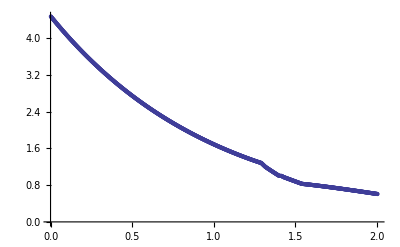

```mathematica
p7=ListPlot[tabT7]
```

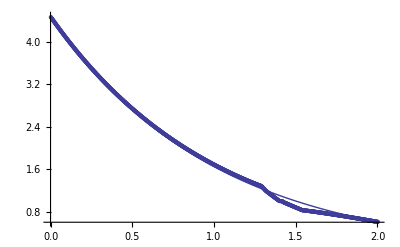

```mathematica
Show[pd3,p7]
```

### alfa = 8/10, t=2

```mathematica
str8=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,91]

```mathematica
strList8=ReadList[str8]
```

{7.38372,7.3693,7.35492,7.34056,7.32624,7.31194,7.29766,7.28342,7.26921,7.25502,7.24086,7.22673,7.21263,7.19855,7.1845,7.17049,7.15649,7.14253,7.1286,7.11469,7.10081,7.08696,7.07313,7.05934,7.04557,7.03183,7.01811,7.00442,6.99076,6.97713,6.96353,6.94995,6.9364,6.92287,6.90938,6.8959,6.88246,6.86904,6.85565,6.84229,6.82895,6.81564,6.80236,6.7891,6.77587,6.76266,6.74948,6.73633,6.72321,6.71011,6.69703,6.68398,6.67096,6.65796,6.64499,6.63205,6.61913,6.60623,6.59337,6.58052,6.56771,6.55491,6.54215,6.52941,6.51669,6.504,6.49133,6.47869,6.46608,6.45349,6.44092,6.42838,6.41587,6.40338,6.39091,6.37847,6.36605,6.35366,6.3413,6.32895,6.31663,6.30434,6.29207,6.27983,6.26761,6.25541,6.24324,6.23109,6.21897,6.20687,6.1948,6.18275,6.17072,6.15872,6.14675,6.13479,6.12287,6.11096,6.09908,6.08722,6.07539,6.06358,6.05179,6.04003,6.02829,6.01658,6.00488,5.99322,5.98157,5.96995,5.95835,5.94678,5.93522,5.92369,5.91219,5.90071,5.88925,5.87781,5.8664,5.85501,5.84364,5.83229,5.82097,5.80967,5.79839,5.78714,5.77591,5.7647,5.75351,5.74234,5.7312,5.72008,5.70898,5.69791,5.68685,5.67582,5.66481,5.65383,5.64286,5.63192,5.621,5.6101,5.59922,5.58836,5.57753,5.56671,5.55592,5.54515,5.53441,5.52368,5.51297,5.50229,5.49163,5.48099,5.47037,5.45977,5.44919,5.43864,5.4281,5.41759,5.4071,5.39663,5.38618,5.37575,5.36534,5.35496,5.34459,5.33425,5.32393,5.31362,5.30334,5.29308,5.28284,5.27263,5.26243,5.25225,5.24209,5.23196,5.22184,5.21175,5.20167,5.19162,5.18158,5.17157,5.16157,5.1516,5.14165,5.13171,5.1218,5.11191,5.10204,5.09218,5.08235,5.07254,5.06274,5.05297,5.04321,5.03348,5.02377,5.01407,5.0044,4.99474,4.9851,4.97549,4.96589,4.95631,4.94675,4.93721,4.92769,4.91819,4.90871,4.89925,4.8898,4.88038,4.87097,4.86159,4.85222,4.84287,4.83354,4.82423,4.81494,4.80567,4.79641,4.78718,4.77796,4.76877,4.75959,4.75043,4.74129,4.73217,4.72306,4.71398,4.70491,4.69587,4.68684,4.67783,4.66884,4.65986,4.65091,4.64197,4.63305,4.62415,4.61527,4.60641,4.59756,4.58874,4.57993,4.57113,4.56236,4.55361,4.54487,4.53615,4.52745,4.51876,4.5101,4.50145,4.49282,4.4842,4.47561,4.46703,4.45847,4.44993,4.4414,4.43289,4.4244,4.41593,4.40747,4.39903,4.39061,4.38221,4.37382,4.36545,4.3571,4.34876,4.34044,4.33214,4.32386,4.31559,4.30734,4.29911,4.29089,4.28269,4.27451,4.26634,4.2582,4.25006,4.24195,4.23385,4.22577,4.21771,4.20966,4.20163,4.19362,4.18562,4.17764,4.16968,4.16173,4.1538,4.14588,4.13798,4.1301,4.12224,4.11439,4.10656,4.09874,4.09094,4.08316,4.07539,4.06764,4.0599,4.05218,4.04448,4.03679,4.02912,4.02147,4.01383,4.0062,3.99859,3.991,3.98343,3.97587,3.96832,3.96079,3.95328,3.94578,3.9383,3.93083,3.92338,3.91594,3.90852,3.90112,3.89373,3.88636,3.879,3.87165,3.86433,3.85701,3.84972,3.84244,3.83517,3.82792,3.82069,3.81347,3.80626,3.79907,3.7919,3.78474,3.7776,3.77047,3.76335,3.75626,3.74917,3.7421,3.73505,3.72801,3.72099,3.71398,3.70699,3.70001,3.69304,3.68609,3.67916,3.67224,3.66533,3.65844,3.65157,3.6447,3.63786,3.63102,3.62421,3.6174,3.61061,3.60384,3.59708,3.59033,3.5836,3.57688,3.57018,3.56349,3.55682,3.55016,3.54351,3.53688,3.53026,3.52365,3.51706,3.51049,3.50393,3.49738,3.49084,3.48432,3.47782,3.47133,3.46485,3.45839,3.45194,3.4455,3.43908,3.43267,3.42628,3.4199,3.41353,3.40718,3.40084,3.39452,3.38821,3.38191,3.37563,3.36936,3.3631,3.35686,3.35063,3.34441,3.33821,3.33202,3.32585,3.31969,3.31354,3.3074,3.30128,3.29517,3.28908,3.283,3.27693,3.27087,3.26483,3.2588,3.25279,3.24679,3.2408,3.23482,3.22886,3.22291,3.21697,3.21104,3.20513,3.19923,3.19335,3.18748,3.18162,3.17577,3.16994,3.16412,3.15831,3.15251,3.14673,3.14096,3.1352,3.12946,3.12373,3.11801,3.11231,3.10662,3.10094,3.09527,3.08962,3.08397,3.07835,3.07273,3.06713,3.06154,3.05596,3.05039,3.04484,3.0393,3.03377,3.02825,3.02275,3.01726,3.01178,3.00631,3.00086,2.99542,2.98999,2.98457,2.97917,2.97377,2.96839,2.96303,2.95767,2.95233,2.94699,2.94167,2.93637,2.93107,2.92579,2.92051,2.91525,2.91001,2.90477,2.89954,2.89433,2.88913,2.88394,2.87877,2.8736,2.86845,2.86331,2.85818,2.85306,2.84796,2.84286,2.83778,2.83271,2.82766,2.82261,2.81758,2.81256,2.80755,2.80255,2.79756,2.79259,2.78762,2.78267,2.77773,2.7728,2.76788,2.76298,2.75808,2.7532,2.74833,2.74347,2.73862,2.73379,2.72896,2.72415,2.71935,2.71456,2.70978,2.70501,2.70025,2.6955,2.69077,2.68605,2.68133,2.67663,2.67194,2.66727,2.6626,2.65794,2.6533,2.64866,2.64404,2.63943,2.63483,2.63024,2.62566,2.62109,2.61653,2.61199,2.60745,2.60293,2.59842,2.59392,2.58943,2.58495,2.58048,2.57603,2.57158,2.56715,2.56272,2.55831,2.55391,2.54952,2.54514,2.54077,2.53641,2.53207,2.52773,2.5234,2.51909,2.51479,2.51049,2.50621,2.50194,2.49768,2.49343,2.48919,2.48496,2.48074,2.47653,2.47234,2.46815,2.46397,2.45981,2.45565,2.45151,2.44737,2.44325,2.43914,2.43504,2.43094,2.42686,2.42279,2.41873,2.41468,2.41064,2.40661,2.40259,2.39858,2.39458,2.3906,2.38662,2.38265,2.3787,2.37475,2.37081,2.36689,2.36297,2.35907,2.35518,2.35129,2.34742,2.34356,2.33971,2.33586,2.33203,2.32821,2.3244,2.3206,2.31681,2.31303,2.30926,2.3055,2.30175,2.29801,2.29428,2.29056,2.28685,2.28315,2.27946,2.27578,2.27211,2.26845,2.2648,2.26116,2.25753,2.25392,2.25031,2.24671,2.24312,2.23954,2.23597,2.23241,2.22886,2.22532,2.22179,2.21827,2.21476,2.21126,2.20777,2.20429,2.20082,2.19736,2.19391,2.19047,2.18704,2.18362,2.18021,2.17681,2.17341,2.17003,2.16666,2.1633,2.15995,2.15661,2.15328,2.14996,2.14665,2.14334,2.14005,2.13677,2.1335,2.13024,2.12698,2.12374,2.12051,2.11728,2.11407,2.11086,2.10767,2.10449,2.10131,2.09815,2.09499,2.09184,2.08871,2.08558,2.08246,2.07936,2.07626,2.07317,2.07009,2.06702,2.06396,2.06091,2.05787,2.05484,2.05182,2.04881,2.0458,2.04281,2.03983,2.03685,2.03389,2.03093,2.02799,2.02505,2.02213,2.01921,2.0163,2.0134,2.01052,2.00764,2.00477,2.00191,1.99906,1.99622,1.99339,1.99057,1.98776,1.98496,1.98217,1.97938,1.97661,1.97385,1.97109,1.96835,1.96561,1.96289,1.96017,1.95747,1.95477,1.95208,1.9494,1.94674,1.94408,1.94143,1.93879,1.93616,1.93354,1.93092,1.92832,1.92573,1.92314,1.92057,1.918,1.91545,1.9129,1.91037,1.90784,1.90532,1.90281,1.90031,1.89782,1.89534,1.89287,1.89041,1.88795,1.88551,1.88307,1.88065,1.87823,1.87583,1.87343,1.87104,1.86866,1.86629,1.86393,1.86158,1.85924,1.85691,1.85459,1.85228,1.84997,1.84768,1.8454,1.84312,1.84086,1.8386,1.83635,1.83412,1.83189,1.82967,1.82746,1.82527,1.82308,1.8209,1.81873,1.81657,1.81441,1.81227,1.81014,1.80801,1.8059,1.8038,1.8017,1.79961,1.79754,1.79547,1.79341,1.79137,1.78933,1.7873,1.78528,1.78327,1.78126,1.77927,1.77729,1.77532,1.77335,1.7714,1.76945,1.76752,1.76559,1.76367,1.76176,1.75987,1.75798,1.7561,1.75423,1.75236,1.75051,1.74867,1.74684,1.74501,1.7432,1.74139,1.7396,1.73781,1.73603,1.73427,1.73251,1.73076,1.72902,1.72729,1.72557,1.72386,1.72216,1.72047,1.71879,1.71712,1.71546,1.71381,1.71216,1.71053,1.70891,1.7073,1.70569,1.7041,1.70251,1.70094,1.69937,1.69782,1.69627,1.69474,1.69321,1.6917,1.69019,1.68869,1.6872,1.68573,1.68426,1.6828,1.68135,1.67991,1.67848,1.67706,1.67565,1.67425,1.67286,1.67148,1.67011,1.66875,1.6674,1.66606,1.66473,1.6634,1.66209,1.66079,1.65949,1.65821,1.65694,1.65567,1.65442,1.65317,1.65194,1.65071,1.6495,1.64829,1.6471,1.64591,1.64474,1.64357,1.64241,1.64127,1.64013,1.639,1.63788,1.63678,1.63568,1.63459,1.63351,1.63244,1.63138,1.63033,1.6293,1.62827,1.62725,1.62624,1.62524,1.62426,1.62328,1.62231,1.62136,1.62041,1.61948,1.61855,1.61764,1.61674,1.61585,1.61497,1.6141,1.61324,1.6124,1.61156,1.61074,1.60993,1.60913,1.60834,1.60756,1.60679,1.60604,1.6053,1.60456,1.60385,1.60314,1.60244,1.60176,1.60109,1.60043,1.59978,1.59914,1.59852,1.59791,1.59731,1.59672,1.59614,1.59558,1.59503,1.59449,1.59397,1.59345,1.59295,1.59246,1.59199,1.59153,1.59108,1.59064,1.59021,1.5898,1.5894,1.58902,1.58864,1.58828,1.58794,1.5876,1.58728,1.58698,1.58668,1.5864,1.58613,1.58588,1.58564,1.58541,1.5852,1.585,1.58481,1.58464,1.58448,1.58434,1.5842,1.58409,1.58398,1.58389,1.58382,1.58376,1.58371,1.58367,1.58366,1.58365,1.58366,1.58368,1.58372,1.58377,1.58384,1.58392,1.58402,1.58413,1.58426,1.5844}

```mathematica
strList8={7.383718023,7.3693046683,7.3549198217,7.3405634214,7.3262354057,7.3119357133,7.2976642829,7.2834210591,7.2692059864,7.2550190096,7.2408600736,7.2267291232,7.2126261036,7.1985509599,7.1845039468,7.1704850015,7.1564940612,7.1425310633,7.1285959452,7.1146886446,7.1008090992,7.0869572469,7.0731330256,7.0593363734,7.0455672286,7.0318255295,7.0181112145,7.0044242223,6.9907644916,6.9771319611,6.9635265703,6.949948262,6.936396979,6.9228726644,6.9093752612,6.8959047127,6.8824609623,6.8690439535,6.8556536297,6.8422899346,6.8289528122,6.8156422062,6.8023580607,6.7891003198,6.7758689278,6.762663829,6.7494849679,6.73633229,6.7232057413,6.7101052677,6.6970308153,6.6839823302,6.6709597589,6.6579630476,6.6449921429,6.6320469915,6.6191275399,6.6062337351,6.593365524,6.5805228535,6.5677056709,6.5549139233,6.5421475582,6.5294065229,6.516690765,6.5040002321,6.491334872,6.4786946326,6.4660794618,6.4534893077,6.4409241184,6.4283838422,6.4158684301,6.4033778348,6.3909120092,6.378470906,6.3660544783,6.3536626791,6.3412954617,6.3289527792,6.316634585,6.3043408327,6.2920714759,6.279826765,6.2676066486,6.2554110755,6.2432399947,6.2310933549,6.2189711055,6.2068731955,6.1947995742,6.1827501911,6.1707249956,6.1587239374,6.1467469661,6.1347940316,6.1228650838,6.1109600727,6.0990789484,6.0872216612,6.0753881614,6.0635783993,6.0517923256,6.0400298908,6.0282910457,6.0165757411,6.0048839279,5.9932155572,5.9815705801,5.9699489477,5.9583506115,5.9467755229,5.9352236334,5.9236948945,5.9121892581,5.9007066759,5.8892470999,5.8778104821,5.8663967745,5.8550059294,5.8436378992,5.8322926361,5.8209700928,5.8096702217,5.7983929757,5.7871383074,5.7759061697,5.7646965157,5.7535092984,5.742344471,5.7312019867,5.7200817989,5.7089838611,5.6979081267,5.6868545495,5.6758230831,5.6648136815,5.6538262984,5.6428608879,5.6319174042,5.6209958013,5.6100960337,5.5992180557,5.5883618217,5.5775272864,5.5667144043,5.5559231335,5.5451534334,5.5344052634,5.5236785833,5.5129733526,5.5022895312,5.4916270788,5.4809859554,5.4703661211,5.4597677985,5.4491909426,5.4386355085,5.4281014515,5.417588727,5.4070972902,5.3966270968,5.3861781022,5.3757502623,5.3653435327,5.3549578695,5.3445932284,5.3342495656,5.3239268372,5.3136249996,5.3033440089,5.2930838216,5.2828443944,5.2726256836,5.2624276461,5.2522502387,5.2420934182,5.2319571415,5.2218413658,5.2117460482,5.2016711459,5.1916166162,5.1815824166,5.1715685046,5.1615748377,5.1516013736,5.1416480702,5.1317148851,5.1218017765,5.1119087023,5.1020356206,5.0921824896,5.0823492676,5.0725359131,5.0627423844,5.0529686401,5.0432146389,5.0334803394,5.0237657005,5.014070681,5.00439524,4.9947393365,4.9851029296,4.9754859785,4.9658884427,4.9563102814,4.9467514542,4.9372119206,4.9276916403,4.918190573,4.9087086819,4.8992459317,4.8898022871,4.8803777128,4.8709721738,4.8615856349,4.8522180611,4.8428694176,4.8335399198,4.8242295256,4.8149381948,4.8056658874,4.7964125639,4.7871781844,4.7779627097,4.7687661,4.7595883162,4.7504293189,4.7412890689,4.732167527,4.7230646544,4.713980412,4.7049147609,4.6958676623,4.6868390777,4.6778289683,4.6688372956,4.6598640212,4.6509091067,4.6419725138,4.6330542044,4.6241541402,4.6152722833,4.6064085958,4.5975630396,4.5887355771,4.5799261705,4.5711347822,4.5623613746,4.5536059103,4.5448683519,4.536148662,4.5274468035,4.5187627392,4.5100964319,4.5014478448,4.4928169409,4.4842036833,4.4756080354,4.4670299604,4.4584694217,4.4499263828,4.4414008074,4.4328926589,4.4244019011,4.4159284978,4.407472413,4.3990336104,4.3906120542,4.3822077096,4.3738205456,4.3654505313,4.3570976357,4.3487618282,4.340443078,4.3321413543,4.3238566267,4.3155891073,4.3073387584,4.2991055426,4.2908894235,4.2826903658,4.2745083341,4.266343293,4.2581952074,4.2500640421,4.2419497621,4.2338523323,4.2257717178,4.2177078839,4.2096607958,4.2016304188,4.1936167182,4.1856196597,4.1776392087,4.1696753309,4.1617279919,4.1537971577,4.145882794,4.1379848668,4.130103342,4.1222381859,4.1143893645,4.1065568441,4.0987405911,4.0909405717,4.0831567525,4.0753891001,4.0676375809,4.0599021619,4.0521828096,4.0444794909,4.0367921728,4.0291208222,4.0214654062,4.013825892,4.0062022467,3.9985944376,3.9910024321,3.9834261976,3.9758657016,3.9683209117,3.9607917955,3.9532783207,3.9457804551,3.9382981666,3.9308314255,3.9233802045,3.9159444768,3.9085242152,3.9011193928,3.8937299828,3.8863559583,3.8789972927,3.8716541932,3.864326626,3.8570145573,3.8497179539,3.8424367841,3.8351710162,3.8279206189,3.8206855606,3.8134658101,3.8062613359,3.799072107,3.7918980922,3.7847392604,3.7775955806,3.7704670219,3.7633535535,3.7562551446,3.7491717644,3.7421033824,3.7350499679,3.7280114906,3.7209879199,3.7139792256,3.7069853773,3.7000063449,3.6930420982,3.6860926072,3.6791578418,3.6722377722,3.6653323685,3.658441601,3.6515654398,3.6447038554,3.6378568182,3.6310242987,3.6242062675,3.6174026952,3.6106135525,3.6038388102,3.5970784391,3.5903324101,3.5836006943,3.5768832626,3.5701800862,3.5634911363,3.5568163841,3.550155801,3.5435093611,3.5368770408,3.5302588166,3.5236546649,3.5170645624,3.5104884855,3.503926411,3.4973783156,3.4908444051,3.4843246489,3.4778190167,3.4713274782,3.4648500047,3.4583865679,3.4519371398,3.4455016924,3.4390801978,3.4326726279,3.4262789552,3.4198991517,3.4135331899,3.4071810422,3.400842681,3.3945180789,3.3882072085,3.3819100424,3.3756265535,3.3693567145,3.3631004983,3.3568578778,3.3506288262,3.3444133164,3.3382113216,3.3320228151,3.3258477701,3.31968616,3.3135379582,3.3074031382,3.3012816735,3.2951735379,3.2890787049,3.2829971483,3.2769288419,3.2708737597,3.2648318755,3.2588031635,3.2527875976,3.246785152,3.240795801,3.2348195188,3.2288562798,3.2229060584,3.2169688289,3.2110445661,3.2051332491,3.1992348574,3.1933493707,3.1874767688,3.1816170314,3.1757701385,3.1699360698,3.1641150365,3.1583070112,3.1525119668,3.146729876,3.1409607118,3.1352044483,3.1294610605,3.1237305235,3.1180128126,3.112307903,3.1066157699,3.1009363887,3.095269735,3.0896157842,3.0839745119,3.0783458937,3.0727299053,3.0671265226,3.0615357213,3.0559574774,3.0503917669,3.0448385657,3.03929785,3.033769596,3.0282537799,3.0227503779,3.0172593665,3.0117807221,3.0063144211,3.0008604402,2.9954187559,2.989989345,2.9845721842,2.9791672502,2.9737745201,2.9683939706,2.9630255789,2.957669322,2.952325177,2.9469931212,2.9416731317,2.9363651859,2.9310692612,2.925785335,2.9205133849,2.9152533887,2.9100053289,2.9047691883,2.8995449496,2.8943325955,2.889132109,2.883943473,2.8787666703,2.873601913,2.8684491767,2.8633084374,2.8581796709,2.8530628531,2.8479579609,2.8428649722,2.8377838651,2.832714618,2.827657209,2.8226116165,2.8175778189,2.8125557947,2.8075455222,2.8025469803,2.7975601474,2.7925850024,2.787621524,2.7826696911,2.7777294825,2.7728008772,2.7678838544,2.762978393,2.7580844723,2.7532020715,2.7483311699,2.7434717467,2.7386237816,2.7337872539,2.7289621432,2.724148429,2.7193460912,2.7145551094,2.7097754633,2.705007133,2.7002500982,2.695504339,2.6907698355,2.6860465676,2.6813345157,2.67663366,2.6719439807,2.6672654582,2.6625980729,2.6579418053,2.6532966387,2.6486625586,2.6440395507,2.6394276008,2.6348266947,2.6302368183,2.6256579573,2.6210903307,2.616533917,2.611988695,2.6074546437,2.6029317419,2.5984199686,2.5939193041,2.5894297295,2.5849512259,2.5804837745,2.5760273565,2.5715819531,2.5671475459,2.5627241163,2.5583116456,2.5539101156,2.5495195078,2.545139804,2.5407709858,2.5364130351,2.5320659339,2.527729664,2.5234042074,2.5190895463,2.5147856628,2.510492539,2.5062101573,2.5019385,2.4976775495,2.4934272881,2.4891876985,2.4849587633,2.480740465,2.4765327864,2.4723357103,2.4681492194,2.4639732967,2.4598079251,2.4556530877,2.4515087675,2.4473749477,2.4432516115,2.4391387421,2.4350363229,2.4309443373,2.4268627687,2.4227916052,2.4187308355,2.4146804482,2.4106404321,2.4066107761,2.402591469,2.3985824997,2.3945840888,2.390596218,2.3866188692,2.3826520244,2.3786956654,2.3747497746,2.3708143357,2.366889333,2.3629747504,2.3590705723,2.3551767828,2.3512933664,2.3474203073,2.34355759,2.339705199,2.3358631189,2.3320313344,2.3282098302,2.3243985909,2.3205976016,2.316806847,2.3130263121,2.309255982,2.3054958417,2.3017458765,2.2980060715,2.294276412,2.2905568834,2.286847471,2.2831481605,2.2794589372,2.2757797869,2.2721106951,2.2684516477,2.2648026303,2.261163629,2.2575346295,2.253915618,2.2503065804,2.2467075029,2.2431183715,2.2395391727,2.2359698927,2.2324105178,2.2288610345,2.2253214293,2.2217916916,2.218271813,2.2147617856,2.211261601,2.2077712514,2.2042907286,2.2008200246,2.1973593692,2.1939087473,2.190468144,2.1870375444,2.1836169337,2.1802062972,2.176805622,2.1734148951,2.1700341039,2.1666632356,2.1633022777,2.1599512176,2.1566100427,2.1532787407,2.1499572992,2.1466457059,2.1433439486,2.1400520151,2.1367698934,2.1334975714,2.1302350372,2.1269822788,2.1237392845,2.1205060425,2.117282541,2.1140687686,2.1108647136,2.1076703645,2.1044857099,2.1013107384,2.0981454388,2.0949897998,2.0918438103,2.0887074591,2.0855807353,2.0824636279,2.079356126,2.0762582187,2.0731698954,2.0700911452,2.0670219576,2.063962322,2.0609122279,2.0578716649,2.0548406226,2.0518190906,2.0488070589,2.0458045172,2.0428114583,2.0398278775,2.0368537702,2.0338891316,2.0309339573,2.0279882426,2.0250519832,2.0221254182,2.0192085364,2.0163013264,2.0134037771,2.0105158774,2.0076376171,2.0047689868,2.0019099771,1.9990605789,1.9962207828,1.9933905799,1.9905699609,1.9877589169,1.9849574391,1.9821655184,1.9793831463,1.9766103139,1.9738470127,1.971093234,1.9683489694,1.9656142104,1.9628889487,1.960173176,1.957466884,1.9547700647,1.95208271,1.9494048118,1.9467363622,1.9440773534,1.9414277775,1.9387876268,1.9361568937,1.9335355706,1.93092365,1.9283211244,1.9257279865,1.9231442289,1.9205698444,1.9180048259,1.9154491662,1.9129028584,1.9103658954,1.9078382704,1.9053199767,1.9028110073,1.9003113557,1.8978210153,1.8953399796,1.8928682419,1.8904057961,1.8879526357,1.8855087567,1.8830741586,1.880648841,1.8782328035,1.8758260458,1.8734285676,1.8710403689,1.8686614494,1.8662920583,1.863932189,1.8615818349,1.85924099,1.8569096489,1.8545878065,1.8522754575,1.8499725968,1.8476792195,1.8453953206,1.8431208952,1.8408559385,1.8386004458,1.8363544125,1.834117834,1.8318907058,1.8296730235,1.8274647828,1.8252659793,1.8230766088,1.8208966674,1.8187261508,1.8165650552,1.8144133767,1.8122711114,1.8101382555,1.8080148055,1.8059007577,1.8037961086,1.8017008548,1.7996149928,1.7975385195,1.7954714315,1.7934137257,1.7913653991,1.7893264487,1.7872968715,1.7852766647,1.7832658256,1.7812643514,1.7792722395,1.7772894874,1.7753160927,1.7733520529,1.7713973656,1.7694520288,1.7675160402,1.7655893977,1.7636720994,1.7617641432,1.7598655274,1.7579762501,1.7560963096,1.7542257044,1.7523644328,1.7505124934,1.7486698848,1.7468366122,1.7450126817,1.7431980995,1.7413928717,1.7395970047,1.7378105047,1.7360333782,1.7342656315,1.7325075403,1.730759105,1.7290203259,1.7272912035,1.7255717384,1.7238619311,1.7221617822,1.7204712925,1.7187904628,1.7171192938,1.7154577865,1.7138059417,1.7121637606,1.7105312442,1.7089083935,1.7072952098,1.7056916943,1.7040978484,1.7025136732,1.7009391702,1.6993743409,1.6978191868,1.6962737093,1.6947379101,1.6932117909,1.6916953532,1.6901885988,1.6886915296,1.6872041472,1.6857264537,1.6842584508,1.6828001406,1.681351525,1.6799126061,1.6784833859,1.6770638665,1.6756540502,1.6742539389,1.6728635351,1.6714828409,1.6701118587,1.6687505907,1.6673990393,1.6660572069,1.6647250959,1.6634027088,1.662090048,1.6607871161,1.6594939155,1.6582104489,1.6569367188,1.6556727279,1.6544184787,1.653173974,1.6519392164,1.6507142087,1.6494989535,1.6482934536,1.6470977117,1.6459117307,1.6447355134,1.6435690625,1.6424123809,1.6412654715,1.6401283371,1.6390009806,1.6378834049,1.6367756128,1.6356776074,1.6345893914,1.6335109679,1.6324423686,1.6313836742,1.6303349652,1.6292963218,1.6282678242,1.6272495232,1.6262414658,1.6252436992,1.6242562704,1.6232792266,1.6223126146,1.6213564815,1.6204108741,1.6194761645,1.6185523963,1.6176396131,1.6167378584,1.615847176,1.6149676094,1.6140992023,1.6132419984,1.6123960412,1.6115613745,1.610738042,1.6099260873,1.6091255541,1.6083364863,1.6075589275,1.6067929216,1.6060385123,1.6052957435,1.604564659,1.6038453028,1.6031377189,1.6024419511,1.6017580435,1.6010860401,1.6004259851,1.5997779226,1.5991418967,1.5985179517,1.5979061319,1.5973064817,1.5967190454,1.5961438674,1.5955809923,1.5950304647,1.5944923291,1.5939666303,1.593453413,1.5929527221,1.5924646024,1.5919890989,1.5915262566,1.5910761208,1.5906387365,1.590214149,1.5898024038,1.5894035462,1.5890176217,1.588644676,1.5882847548,1.5879379039,1.5876041691,1.5872835964,1.586976232,1.5866821219,1.5864013124,1.58613385,1.5858797811,1.5856391522,1.5854120102,1.5851984017,1.5849983738,1.5848119734,1.5846392476,1.5844802439,1.5843350094,1.5842035918,1.5840860386,1.5839823976,1.5838927167,1.5838170439,1.5837554273,1.5837079152,1.583674556,1.5836553982,1.5836504905,1.5836598818,1.583683621,1.5837217571,1.5837743395,1.5838414176,1.5839230408,1.5840192589,1.5841301217,1.5842556793,1.5843959817};
```

```mathematica
tabT8=Table[{i*0.002,strList8[[i]]},{i,1,1001}];
```

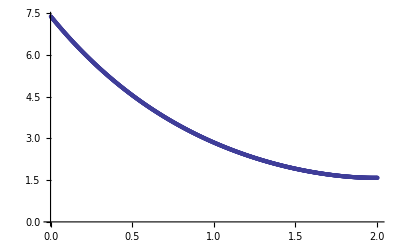

```mathematica
p8=ListPlot[tabT8]
```

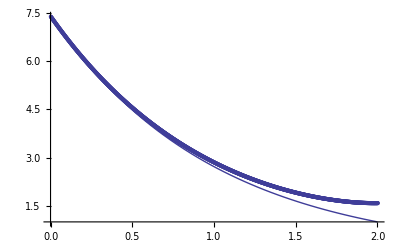

```mathematica
Show[pd4,p8]
```